Leonid Shifrin

Mathematica programming: an advanced introduction                             <   >    Ξ

Edited by Hao Feng

## Section | Rules, patters and functions

### Introduction

In this chapter we will introduce the notion of functions in Mathematica, and also consider numerous examples of functions. Since the Mathematica programming language is to a large extent a functional programming language, functions are the central objects here. Also, since lists are used as universal building blocks for data structures, and any complex data structure can be built with lists and modified “on the fly”, the emphasis is shifted more towards functions, as compared say to OO  programming languages.

Another important aspect of functions and functional programming in Mathematica is that this “layer” of programming is built upon a (in my view, more fundamental in Mathematica) rule-based engine. This results in the notion of function which is wider than, and also significantly different from that in most other programming languages. Thus, one will not have a complete grasp of functions in Mathematica without the understanding of rules and rule-based programming techniques. We will discuss them here as well.

### Rules and patterns

To better understand functions in Mathematica, we need a good understanding of patterns and rule substitution. These two topics are just two facets of a single one, since it is the form of the pattern which determines when (on which class of objects) the associated rule will apply.

#### Rule, RuleDelayed, Replace and ReplaceAll commands

Basic rules and the Rule head (function)

It is very easy to organize a rewrite rule in Mathematica. For example, the following rule will replace a to b

```mathematica
Clear[a,b,ourrule];
ourrule=a->b
```

a→b

The literal equivalent to the arrow (which represents the rule) is the Rule command. If we look at the FullForm of <ourrule> variable, we see that Rule is used:

```mathematica
FullForm[ourrule]
```

Rule[a,b]

How to make the rule apply: ReplaceAll function

By itself, any rule that we define does not do anything useful. The command Rule by itself is just a named container of the left and right hand sides of the rule. It becomes useful when combined with another command, which actually performs the rule substitution in an expression. This command has a format ReplaceAll[expr, rules], and a shorthand notation: <expr/.rules>. There can be more than one rule being applied, in which case they should normally be placed into a simple (not nested) list - we will see such examples later . If the rules are placed in a nested list, Mathematica interprets them differently - see Mathematica Help for details, and also below.

This is, for instance, how our rule will work on some test expression:

```mathematica
Clear[f,a,b];
f[a]/.ourrule
```

f[b]

or, which is the same,

```mathematica
f[a]/.a->b
```

f[b]

If we have a more complicated expression, where <a> happens places (when we use /., or ReplaceAll command):

```mathematica
Clear[f,g,h];
f[a,g[a,h[a]]]/.a->b
```

f[b,g[b,h[b]]]

The order in which ReplaceAll tries rules on parts of expressions

Although this is not immediately obvious, often the rule application starts from the larger expression, and if it matches as a whole, then the subexpressions are not checked for further matches. This is so when the pattern (see discussion on patterns below) looks like h[x_] or similar. For example, in this case:

```mathematica
Clear[a,q];
{{{a}}}/.{x_}:>q[x]
```

q[{{a}}]

we will need to apply the rule several times to replace all the list braces with <q> - s:

```mathematica
{{{a}}}/.{x_}:>q[x]/.{x_}:>q[x]
```

q[q[{a}]]

```mathematica
{{{a}}}/.{x_}:>q[x]/.{x_}:>q[x]/.{x_}:>q[x]
```

q[q[q[a]]]

But not in this case - here the pattern is just a symbol List:

```mathematica
{{{a}}}/.List->q
```

q[q[q[a]]]

This behavior is rather logical, but in cases when a different order of rule substitution is desired, techniques are available to change it. We will discuss them later (see section 5.2.4.2).

Associativity of rules

As the previous example may have suggested, the application of rules is left-associative, meaning that in the expression <expr /. rule1 /. rule2> is legitimate, and first the rule (or rules if this is a list of rules, see below) <rule1> will be applied to <expr>, and then the rule (s) <rule2> will be applied to the result.

Locality of rules

It is very important that the rules like the one above are local. This means that when the rule rewrites an object to which it applies into something else, it changes the copy of it, while the initial object remains unchanged. In particular, in the above example, an expression f[a] taken separately, did not change:

```mathematica
f[a]
```

f[a]

This is the main difference between the rule and the function which performs a similar transformation - in the latter case a similar rule is defined globally (which means that it will be automatically tried by the kernel on any expression entered interactively or being otherwise evaluated). Essentially, this is the only fundamental difference between functions and lists of rules in Mathematica. For example, we can easily simulate the squaring function by a local rule:

```mathematica
Clear[f];
{f[x],f[y],f[elephant],f[3]}/.f[z_]:>z^2
```

{x^2,y^2,elephant^2,9}

Delayed rules - the RuleDelayed function

I used this example to introduce two new ideas. First, we now have patterns on the left hand side of the rule - they are used to widen the class of objects to which the rule will apply. Second, we have used a new kind of rule (there are only two, and one we already considered before) - the one which uses the:> (colon - greater) sign instead of -> one. The literal equivalent of this is RuleDelayed[lhs,rhs] command:

```mathematica
RuleDelayed[a,b]
```

a:>b

As we can guess by the name, this corresponds to a delayed rule substitution - that is, the r.h.s. of the rule is evaluated only after the rule substitution takes place. Later we will consider cases where Rule or RuleDelayed are more appropriate, in more detail, but in general the situation here is similar with the one with Set and SetDelayed assignment operators. This similarity is not accidental, but once again reflects the fact the assignment operators in Mathematica are just operators which create global rules.

The difference between Rule and RuleDelayed

To illustrate a difference between Rule and RuleDelayed on one particular example, consider a model problem: given a list of elements, substitute every occurrence of the symbol <a> by a random number. Here is our sample list

```mathematica
Clear[sample,a,b,c,d,e,f,g,h];
sample={d,e,a,c,a,b,f,a,a,e,g,a}
```

{d,e,a,c,a,b,f,a,a,e,g,a}

Now, here is the rule-based solution using Rule:

```mathematica
sample/.a->Random[]
```

{d,e,0.245322,c,0.245322,b,f,0.245322,0.245322,e,g,0.245322}

And here is the same using RuleDelayed:

```mathematica
sample/.a:>Random[]
```

{d,e,0.917876,c,0.958419,b,f,0.142385,0.163451,e,g,0.326276}

We see that the numbers are the same in the first case and different in the second. This is because, in the first case, the r.h.s. of the rule has been evaluated before it was applied, once and for all. In the second case, the r.h.s. of the rule was re-evaluated every time the rule was applied. As a variation on the theme, suppose we want to substitute each <a> in the list by a list {a,num}, where <num> will be counting the
occurrences of <a> in the list. Here is our attempt with Rule:

```mathematica
n=1;
sample/.a->{a,n++}
```

{d,e,{a,1},c,{a,1},b,f,{a,1},{a,1},e,g,{a,1}}

Obviously this did not work as intended. And now with RuleDelayed:

```mathematica
n=1;
sample/.a:>{a,n++}
```

{d,e,{a,1},c,{a,2},b,f,{a,3},{a,4},e,g,{a,5}}

```mathematica
Clear[sample,n];
```

#### Rule substitution is not commutative

Lists of rules

When we have more than just one rule to be tried on an expression, we place the rules in a list. For example:

```mathematica
{a,b,c,d}/.{a->1,b->2,d->4}
```

{1,2,c,4}

For all the rules to be tried on an expression, the list of rules has to be a flat list, that is, all the list elements should have a head Rule or RuleDelayed. Supplying a nested list of rules to Replace or ReplaceAll is not an error, but is interpreted as if we want to try all the sublists of rules separately on several copies of our original expression:

```mathematica
{a,b,c,d}/.{{a->1,b->2},{c->3,d->4}}
```

{{1,2,c,d},{a,b,3,4}}

As a side note, there is nothing special about lists of rules with respect to lists of other Mathematica objects:

```mathematica
FullForm[{a->5,a->6}]
```

List[Rule[a,5],Rule[a,6]]

Non-commutativity

The result of the rule substitution depends in general on the order in which the rules are stored in the list, as the following example illustrates.

```mathematica
Clear[a,f];
f[a]/.{a->5,a->6}
f[a]/.{a->6,a->5}
```

f[5]

f[6]

The reason for this is that once some rule has been applied to a given part of an expression, ReplaceAll goes to the next part of an expression and tries the rules on that next part. But even if we run ReplaceAll several times (there is a special command ReplaceRepeated related to this, which we will discuss shortly), the results will still be generally different for different orderings of rules in a list. This is because once a rule applies to a (part of) expression, this part is generally rewritten so that (some of) the rules in our list of rules which applied before will no longer apply, and vice versa.

In any case, our final conclusion is that the rule application is not commutative, and the order of rules in the rule list does matter in general. For an extreme example of this, we will soon consider a rule-based factorial function, where different rule ordering will result in infinite iteration.

#### An interplay between rules and evaluation process

When working in Mathematica, it is important to remember that we never actually start from scratch, but always with a large built-in system of rules which connect together the built-in functions. This gives great flexibility in using these functions, since these system rules can be manipulated or overridden with the user-defined ones. On the other hand, one has to be more careful, because the rules (or function definitions and variable assignments, which are global rules) newly defined by the user, immediately start to interact with the built-in ones. The mentioned above non-commutativity of rules can make this interaction quite non-trivial. This often results in some unexpected or “erroneous” behavior, which many Mathematica users immediately proclaim as bugs, but which can be avoided just by getting a better understanding of how the system works.

When the rule applies, expression is evaluated

As one example, consider a gamma-function of the symbolic argument:

```mathematica
Clear[a];
Gamma[a]
```

Gamma[a]

Since the system does not know what <a> is, no one of the rules associated with the gamma-function applies, and the input is just returned back. Let us now use the following rewrite rule:

```mathematica
Gamma[a]/.a->5
```

24

We see that as soon as the numerical (integer) value has been substituted, one of the built-in rules applied, producing the result. At the same time, for a number p (for instance), there is no rule which forces Mathematica to compute the numerical value, and thus we have:

```mathematica
Gamma[a]/.a->π
```

Gamma[π]

If we want to compute a numerical value in this case, we can either do this:

```mathematica
Gamma[a]/.a->N[π]
```

2.28804

Or, which is equivalent (with some tiny differences unimportant now), this:

```mathematica
N[Gamma[a]/.a->π]
```

2.28804

(the N function computes a numerical value of its argument). What I want to stress is that the decision whether to keep say Gamma[5] as it is here or to substitute it by its numerical (well, integer) value is rather arbitrary in the sense that it is defined by certain (very sensible) Mathematica conventions but there is no first principle which tells which form of the answer is advantageous. In fact, in some cases I may wish to keep a Gamma[5] function in its unevaluated form. More generally, the whole advantage in using rule-based approach is that we don’t need a first principle to add rules for a new situation that we want to describe.

This means not that Mathematica is unpredictable, but that the programs we write should not depend on features that are defined purely by conventions. In particular, in Mathematica one should always assume that all expressions may evaluate to something else. Thus, if some expression has to be kept unevaluated for some time, the programmer has to take care of it. On the other hand, if some expression must be
evaluated completely (say, to a numerical value), once again the programmer has to ensure it.

Evaluation affects applicability of rules

Consider now a different example:

```mathematica
{f[π],Sin[π],π^2}
{f[π],Sin[π],π^2}/.π->a
```

{f[π],0,π^2}

{f[a],0,a^2}

Note that in the second input in the list, we will naively expect Sin[a] instead of 0 as an output, in the case when we apply the rule Pi -> a. The reason for this result being as it is can be understood easily, once we recall that the sign /. is just an abbreviation, and equivalently we can write the last input as

```mathematica
ReplaceAll[{f[π],Sin[π],π^2},π->a]
```

{f[a],0,a^2}

Now we recall the general evaluation strategy in Mathematica, where the subexpressions are normally evaluated before the expression itself. This means that once the evaluation process reached ReplaceAll command, our expression has been already transformed to the same form as the output of the first input (without rule substitution). Sin[Pi] evaluated to 0, and since 0 does not contain <Pi> any more and thus does not match the rule, no further substitution took place for this part of our expression. Once again, we can see the evaluation dynamics by using the Trace command:

```mathematica
Trace[{f[π],Sin[π],π^2}/.π->a]
```

{{{Sin[π],0},{f[π],0,π^2}},{π→a,π→a},{f[π],0,π^2}/.π→a,{f[a],0,a^2}}

These examples may give an impression that Mathematica is unstable with respect to bugs related to rule orderings. While it is true that many non-trivial bugs in the Mathematica programs are related to this issue, there are also ways to avoid them. As long as the rule or list of rules are always correct in the sense that either they represent exact identities (say, mathematical identities), or one can otherwise be sure that in no actual situation they, taken separately, will lead to an incorrect result, it should be fine.

Bugs happen when rules considered “correct” give incorrect results in certain unforeseen situations, but this is also true for programs written within more traditional programming paradigms. Perhaps, the real difference is that for more traditional programming techniques it is usually easier to restrict the program to
“stay” in those “corners” of the problem parameter space where correct performance can be predicted or sometimes proven. I personally view the complications arising due to rule orderings as a (possibly inevitable) price to pay for having a very general approach to evaluation available.

#### Rules and simple (unrestricted) patterns

Let us give some examples of how rules work with the simplest patterns.

A simplest pattern and general pattern-matching strategy

The simplest pattern of all, which we have already seen before, is just a single underscore <_>, and has a literal representation Blank[]:

```mathematica
Blank[]
```

_

This pattern represents any Mathematica expression. Let us take some sample Mathematica expression:

```mathematica
x^y*Sin[z]
```

Now we will use our simplest pattern to replace any element by, say, a symbol <a>:

```mathematica
Clear[a,x,y,z,g,h];
{x,Sin[x],x^2,x*y,x+y,g[y,x],h[x,y,z],Cos[y]}/._->a
```

a

This is not very exciting. What happened is that our entire expression (list) matched this pattern and then got replaced by <a> . Before we move forward, let me explain a bit how patterns work and why the substitution based on patterns is possible. The main ingredient for this is the uniform representation of Mathematica expressions by symbolic trees. Basically, when we try to match some (however complex) pattern with some expression, we are matching two trees. The tree that represents the pattern is also a legal Mathematica expression (patterns are as good Mathematica expressions as anything else), but with some branches or leaves replaced by special symbols like  Blank[] (the underscore). For example:

```mathematica
FullForm[(_^_)*Sin[_]]
```

Times[Power[Blank[],Blank[]],Sin[Blank[]]]

This pattern tree (or, just pattern) will match some expression <expr> if they are identical modulo some parts of <expr> which can be “fit” in the placeholders such as Blank[], present in this pattern. In particular, the pattern above will match any expression which is a product of something to a power of something else, and a Sine of something.

Does the pattern match? The MatchQ function

There is a very useful command that allows one to check whether or not there is a match between a given expression and a given pattern: MatchQ. It takes as arguments an expression and a pattern and returns True when pattern matches and False otherwise. For example:

```mathematica
MatchQ[x^y*Sin[z],(_^_)*Sin[_]]
```

True

```mathematica
MatchQ[Exp[-x^2]^2*Sin[Cos[x-y]^2],(_^_)*Sin[_]]
```

True

```mathematica
MatchQ[x*Sin[z],(_^_)*Sin[_]]
```

False

It is important to understand that the pattern-matching (for simple, or unrestricted, patterns) is based completely on syntax, and not semantics, of the expressions being matched.

Pattern tags(names) and expression destructuring

Now, while there is some value in just establishing the fact that some expression matches certain pattern, it becomes much more useful when we get access to the parts of this expression which match certain parts of the pattern, so that we can further process these parts. This is called expression destructuring, and is a very powerful pattern-related capability. For instance, in the above example we may wish to know which expressions were the base, the power and the argument of Sine. But to be able to do such destructuring, we need to somehow label the parts of the pattern. This is possible through the mechanism of pattern tags (or names): we attach some symbol to the pattern part, and then this symbol stores the corresponding part of the actual expression matched, ready for further processing. This is how, for example, we can insert tags in our pattern:

```mathematica
(base_^pwr_)*Sin[sinarg_]
```

The pattern tags can not be composite expressions - only true symbols (with the head Symbol).

The presence of pattern tags does not change the matching in any way, it just gives us additional information. We will not obtain this information through MatchQ, however, since MatchQ just establishes the fact of the match. We will need a real rule application for that, since the rule will tell us what to do with these matched (sub) expressions. For example, here we will simply collect them in a list:

```mathematica
{x^y*Sin[z],Exp[-x^2]^2*Sin[Cos[x-y]^2]}/.(base_^pwr_)*Sin[sinarg_]->{base,pwr,sinarg}
```

{{x,y,z},{ⅇ,-2 x^2,Cos[x-y]^2}}

What we just did is exactly a special case of destructuring. The parts that we tagged are now available for whatever operations we would like to perform.

So, to summarize: whenever a pattern contains a part which is a special symbol like Blank[] (there are a few more like it, we will cover them shortly), possibly with a pattern tag attached, this means that the actual expression matched can contain in this place a rather arbitrary subexpression (how arbitrary, depends on the particular special symbol used). However, the parts which do not contain these symbols (multiplication, Power and Sin in our example above), have to be present in exactly the same way in both pattern and the expression, for them to match.

One more important point about pattern tags is that the two identical pattern tags (symbols) in different parts of a pattern can not stand for different corresponding subexpressions in the expression we try to match. For example:

```mathematica
MatchQ[a^a,b_^b_]
```

True

```mathematica
MatchQ[a^c,b_^b_]
```

False

Example: any function of a single fixed argument

The following pattern will work on every function, but of the argument which has to literally be <x>:

```mathematica
Clear[f,x];
f_[x]
```

f_[x]

It can be used for instance when we need to substitute the literal <x> by some value (say, 10) at every place where it appears as a single argument of some function. Consider now some list of expressions which we will use throughout this section to illustrate the construction of various patterns:

```mathematica
Clear[x,y,z,g,h,a];
{x,Sin[x],x^2,x*y,x+y,g[y,x],h[x,y,z],Cos[y]}
```

{x,Sin[x],x^2,x y,x+y,g[y,x],h[x,y,z],Cos[y]}

We now use our pattern:

```mathematica
{x,Sin[x],x^2,x*y,x+y,g[y,x],h[x,y,z],Cos[y]}/.{f_[x]->f[10]}
```

{x,Sin[10],x^2,x y,x+y,g[y,x],h[x,y,z],Cos[y]}

The replacement happened only in the second element of the list. To understand this, we have to recall the tree-like nature of Mathematica expressions and also that the rules application is based on expression syntax rather than semantics. Let us look at the FullForm of these expressions:

```mathematica
FullForm[{x,Sin[x],x^2,x*y,x+y,g[y,x],h[x,y,z],Cos[y]}]
```

List[x,Sin[x],Power[x,2],Times[x,y],Plus[x,y],g[y,x],h[x,y,z],Cos[y]]

We see that only the second list element contains <x> as a single argument, the next four have 2 arguments (and thus the pattern does not match), the next one has 3 arguments, and the last one has a single argument, but <y> instead of <x> .

Any function of 2 arguments, but with the first fixed

Let us now develop other rules which will work selectively on different groups of these elements. First, let us build a rule which will work on elements with 2 arguments - this is easy:

```mathematica
{x,Sin[x],x^2,x*y,x+y,g[y,x],h[x,y,z],Cos[y]}/.{f_[x,z_]->f[10,z]}
```

{x,Sin[x],100,10 y,10+y,g[y,x],h[x,y,z],Cos[y]}

We see that a new pattern is f_[x, z_], which means any function of two arguments, with an arbitrary second argument, but the first argument fixed to literal <x> . Notice that no substitution was performed for g[y,x], since here <x> is the second argument, while in the pattern it is the first one. In general, for simple patterns, the way to determine whether or not a given pattern will match a given expression is to
consider the FullForm of both the pattern and the expression, and see whether the pattern expression has blanks in all places where it is different from the expression it has to match. The FullForm of the above pattern is

```mathematica
FullForm[f_[x,z]]
```

Pattern[f,Blank[]][x,z]

To get a better idea of how the above pattern matched the expressions in our list, we may construct a different rule, which will show us which parts were matched:

```mathematica
{x,Sin[x],x^2,x*y,x+y,g[y,x],h[x,y,z],Cos[y]}/.{f_[x,z_]->{{"f now",f},{"z now",z}}}
```

{x,Sin[x],{{f now,Power},{z now,2}},{{f now,Times},{z now,y}},{{f now,Plus},{z now,y}},g[y,x],h[x,y,z],Cos[y]}

Returning to our previous rule for functions of 2 arguments, let us first fix the problem with the g[y, x] term so that it also matches. Our solution will be to add another rule, thus making a list of replacement rules:

```mathematica
{x,Sin[x],x^2,x*y,x+y,g[y,x],h[x,y,z],Cos[y]}/.{f_[x,z_]->f[10,z],f_[z_,x]->f[z,10]}
```

{x,Sin[x],100,10 y,10+y,g[y,10],h[x,y,z],Cos[y]}

Combining 1, 2 and 3-argument cases together

Now, let us change our rules such that in the Sin[x] the replacement will also take place - that is, now we want <x> to be replaced in functions of either one or two arguments. For this, we combine our very first rule with the last two:

```mathematica
{x,Sin[x],x^2,x*y,x+y,g[y,x],h[x,y,z],Cos[y]}/.{f_[x]:>f[10],f_[x,y_]:>f[10,y],f_[z_,x]->f[z,10]}
```

{x,Sin[10],100,10 y,10+y,g[y,10],h[x,y,z],Cos[y]}

Finally, we would like to add a rule to include a function of 3 variables:

```mathematica
{x,Sin[x],x^2,x*y,x+y,g[y,x],h[x,y,z],Cos[y]}/.{f_[x]->f[10],f_[x,y_]->f[10,y],f_[z_,x]->f[z,10],f_[x,y_,z_]->f[10,y,z]}
```

{x,Sin[10],100,10 y,10+y,g[y,10],h[10,y,z],Cos[y]}

New pattern - building block - BlankSequence - and a caution

Let me now introduce another pattern-building block similar to Blank[], which simplifies the construction of many patterns. The literal command for this new pattern object is BlankSequence[]. Its literal equivalent is a double underscore sign <__>:

```mathematica
BlankSequence[]
```

__

This pattern element is used to represent a sequence of one or more elements in an expression. For example:

```mathematica
{g[x,y,z],g[p,q],h[x,y]}/.g[t__]->{t}
```

{{x,y,z},{p,q},h[x,y]}

However, since this pattern-building block allows one to create patterns which match a much wider class of expressions, sometimes we get not what we would like to. Here, for instance, we want to add a literal <a> as an extra argument to all the functions in the list:

```mathematica
{g[x,y,z],h[x,y]}/.f_[t__]->f[t,a]
```

{g[x,y,z],h[x,y],a}

Instead, <a> was added to the list itself. Why this happened is easy to see from the FullForm of our list:

```mathematica
FullForm[{g[x,y,z],h[x,y]}]
```

List[g[x,y,z],h[x,y]]

We see that the head List matches <f_> (which means any head), and t__ is matched by the interior of the list, since it is indeed a sequence of 2 elements-functions <g> and <h> . Thus, <a> has been added as a last argument to our list of functions, instead of being added to each function in the list. We see that our rule applied 1 level higher than we wanted - to the entire expression rather than parts. This is a common situation when ReplaceAll is used. In this case, the rules are first tried on the larger expressions, and if they match, the rules are applied to them, while subexpressions are not tried any more. There are several ways to change this behavior. One way is to create restricted patterns to make them more selective. Another way is to use the Replace command, which performs rule substitution in a different order.

First look at conditional (restricted) patterns

If we choose the first way, we have to modify our pattern such that the head List will not match. The thing we would like to do is to impose a condition that <f> in the pattern <f> is not the same as List. This is how it is done (more details on restricted patterns later):

```mathematica
{g[x,y,z],h[x,y]}/.f_[t__]/;f=!=List->f[t,a]
```

{g[x,y,z,a],h[x,y,a]}

Now we see that it works as intended.

Using Replace instead of ReplaceAll

If we choose to use the Replace command, here is a way to do the same:

```mathematica
Replace[{g[x,y,z],h[x,y]},f_[t__]->f[t,a],1]
```

{g[x,y,z,a],h[x,y,a]}

The difference between Replace and ReplaceAll is that the former allows us to specify, in which level of expression the rules have to be applied. This gives a more detailed control over the application of rules.

Here, for instance, we required that the rules be applied only at level 1, which means the level of list subexpressions - functions <g> and <h> .

Another difference is that even when we indicate that the rules have to be applied to the whole expression, which we can do by using Replace[expr, rules, Infinity], the order in which the rules will be applied is different from that of ReplaceAll: now the rules will be applied in the depth - first manner, from the smallest (inner) subexpressions to larger (outer) ones. This behavior is often preferred, and then one has to use Replace. We will use this observation in later chapters.

Rule within a rule, and a better catchall solution for our example

Considering our initial problem, it is rather inconvenient to have so many rules for describing essentially some particular cases of a general situation: whenever literal <x> is an argument of some function, change it to <10> in that function. Let us see if we can write a more concise and general solution for this problem. The one that I suggest requires BlankSequence.

Illustrating expression deconstruction

To illustrate how it works here, we will now create a rule which will “deconstruct” our expressions according to this pattern:

```mathematica
{x,Sin[x],x^2,x*y,x+y,g[y,x],h[x,y,z],Cos[y]}/.f_[t__]/;f=!=List->{{"function",f},{"args",{t}}}
```

{x,{{function,Sin},{args,{x}}},{{function,Power},{args,{x,2}}},{{function,Times},{args,{x,y}}},{{function,Plus},{args,{x,y}}},{{function,g},{args,{y,x}}},{{function,h},{args,{x,y,z}}},{{function,Cos},{args,{y}}}}

The reason that I used a restricted pattern with a condition f =!= List is that otherwise the whole list will match, since its elements match the pattern __:

```mathematica
{x,Sin[x],x^2,x*y,x+y,g[y,x],h[x,y,z],Cos[y]}/.f_[t__]->{{"function",f},{"args",{t}}}
```

{{function,List},{args,{x,Sin[x],x^2,x y,x+y,g[y,x],h[x,y,z],Cos[y]}}}

Restricted patterns we will cover later, for now just think of it as a pattern with a certain condition attached. At the same time, this example by itself shows that one has to be careful when defining patterns since the can match in more cases than we expect.

The solution to our problem

Returning to our initial problem, here is a solution:

```mathematica
{x,Sin[x],x^2,x*y,x+y,g[y,x],h[x,y,z],Cos[y]}/.f_[t__]/;f=!=List:>(f[t]/.x->10)
```

{x,Sin[10],100,10 y,10+y,g[y,10],h[10,y,z],Cos[y]}

Explanation

Use parentheses to impose the correct precedence

This solution is remarkable in several aspects. First of all, we have used a rule within a rule, and the inner rule we used in parentheses. The meaning of this is: once we found anything that matches the pattern of the “first” (or “outer”) rule, make a replacement in this expression according to the “second”, or “inner” rule. The first (“outer”) rule acts here essentially as a filter for a second (“inner”) one. Should we omit the parentheses, and we would not get the desired result:

```mathematica
{x,Sin[x],x^2,x*y,x+y,g[y,x],h[x,y,z],Cos[y]}/.f_[t__]/;f=!=List:>f[t]/.x->10
```

{10,Sin[10],100,10 y,10+y,g[y,10],h[10,y,z],Cos[y]}

The reason this happened is that the rule application is left-associative. Thus, the first rule applied first, and was essentially idle, because it says by itself just f_[t__] /; f =!= List:> f[t], that is, replace an expression of this form by itself:

```mathematica
step1={x,Sin[x],x^2,x*y,x+y,g[y,x],h[x,y,z],Cos[y]}/.f_[t__]/;f=!=List:>f[t]
```

{x,Sin[x],x^2,x y,x+y,g[y,x],h[x,y,z],Cos[y]}

The second rule then applied to <step1>, and it says: replace <x> by <10> whenever <x> occurs. Thus, for example, the first element of the list, which is just <x> and is not an argument of any function, also got replaced.

```mathematica
step1/.x->10
```

{10,Sin[10],100,10 y,10+y,g[y,10],h[10,y,z],Cos[y]}

However, if we use the parentheses, we ensure that the second rule is actually applied to the results “filtered” by the first rule.

Use RuleDelayed to supply correct arguments to the inner rule

The second subtlety here is that we used RuleDelayed instead of Rule for the first (outer) rule. It is easy to see that if we don’ t, we will not get a desired result:

```mathematica
{x,Sin[x],x^2,x*y,x+y,g[y,x],h[x,y,z],Cos[y]}/.f_[t__]/;f=!=List->(f[t]/.x->10)
```

{x,Sin[x],x^2,x y,x+y,g[y,x],h[x,y,z],Cos[y]}

The reason is that in the case of Rule, the r.h.s. of the rule is evaluated before the rule is substituted. Recalling the general strategy of Mathematica evaluation, the inner rule will be evaluated before the outer one (this is what parentheses ensure). But by that time, the literal <t> in the outer rule has yet no relation to the matched parts of the list whatsoever, and just remains the literal <t> . Thus, the rule <f[t] /. x ->
10> is completely idle and evaluates to f[t]. This results then in just the first rule f_[t__] /; f =!= List -> f[t], which again is idle.

Confirmation: use Trace command

This description can be confirmed with the Trace command:

```mathematica
{x,Sin[x],x^2,x*y,x+y,g[y,x],h[x,y,z],Cos[y]}/.f_[t__]/;f=!=List->(f[t]/.x->10)//Trace
```

{{{{x→10,x→10},f[t]/.x→10,f[t]},f_[t__]/;f=!=List→f[t],f_[t__]/;f=!=List→f[t]},{x,Sin[x],x^2,x y,x+y,g[y,x],h[x,y,z],Cos[y]}/.f_[t__]/;f=!=List→f[t],{List=!=List,False},{Sin=!=List,True},{Power=!=List,True},{Times=!=List,True},{Plus=!=List,True},{g=!=List,True},{h=!=List,True},{Cos=!=List,True},{x,Sin[x],x^2,x y,x+y,g[y,x],h[x,y,z],Cos[y]}}

If we use RuleDelayed however, the r.h.s of the outer rule (which includes the inner rule) will not be evaluated until some match has been found for the outer rule. This will allow the inner rule to operate on expressions matched by the outer rule.

Rule vs. RuleDelayed - when which one is appropriate

When RuleDelayed is better

In general, it is usually safer to use RuleDelayed in cases when the r.h.s. of the rule is not constant. For instance, all our replacements just discussed would have been totally spoiled had the parts of the pattern definition tags (such as f in f_, t in t__, etc) have any global values. This is, for instance, one of the rules we used above, but with some pattern tags having some global values before the application of rule:

```mathematica
f="Global function";
t="global value";
{x,Sin[x],x^2,x*y,x+y,g[y,x],h[x,y,z],Cos[y]}/.f_[t__]/;f=!=List->{{"function",f},{"args",{t}}}
```

{x,{{function,Global function},{args,{global value}}},{{function,Global function},{args,{global value}}},{{function,Global function},{args,{global value}}},{{function,Global function},{args,{global value}}},{{function,Global function},{args,{global value}}},{{function,Global function},{args,{global value}}},{{function,Global function},{args,{global value}}}}

Once again, this is because the r.h.s. of the rule has been evaluated before any match could have taken place. To be safe, use RuleDelayed:

```mathematica
f="Global function";
t="global value";
{x,Sin[x],x^2,x*y,x+y,g[y,x],h[x,y,z],Cos[y]}/.f_[t__]/;f=!=List:>{{"function",f},{"args",{t}}}
```

{x,{{function,Sin},{args,{x}}},{{function,Power},{args,{x,2}}},{{function,Times},{args,{x,y}}},{{function,Plus},{args,{x,y}}},{{function,g},{args,{y,x}}},{{function,h},{args,{x,y,z}}},{{function,Cos},{args,{y}}}}

```mathematica
Clear[f,t];
```

When Rule is better

There are of course cases when Rule has to be used instead - this is when the r.h.s. of the rule is a constant. For example, say we want to substitute every even number in a list by the value of the integral of the gaussian over the half-line. This is how long it takes with Rule (for this size of the list)

```mathematica
Range[50]/._?EvenQ->Integrate[Exp[-x^2],{x,0,Infinity}]//Short//Timing
```

{0.151423,{1,(√π)/2,3,(√π)/2,5,«41»,47,(√π)/2,49,(√π)/2}}

And now with RuleDelayed:

```mathematica
Range[50]/._?EvenQ:>Integrate[Exp[-x^2],{x,0,Infinity}]//Short//Timing
```

{1.23377,{1,(√π)/2,3,(√π)/2,5,«41»,47,(√π)/2,49,(√π)/2}}

What happens here is that in one case, the integral is computed exactly once, while in the other it is recomputed over and over again. Once again, the situation here is very similar to the one with immediate and delayed assignments Set and SetDelayed.

Patterns testing heads of expressions

Let us again return to our original list of expressions. We can also construct more stringent rules which will operate only on certain functions, for example:

```mathematica
{x,Sin[x],x^2,x*y,x+y,g[y,x],h[x,y,z],Cos[y]}/.f_Sin:>(f/.x->10)
```

{x,Sin[10],x^2,x y,x+y,g[y,x],h[x,y,z],Cos[y]}

```mathematica
{x,Sin[x],x^2,x*y,x+y,g[y,x],h[x,y,z],Cos[y]}/.f_Plus:>(f/.x->10)
```

{x,Sin[x],x^2,x y,10+y,g[y,x],h[x,y,z],Cos[y]}

```mathematica
{x,Sin[x],x^2,x*y,x+y,g[y,x],h[x,y,z],Cos[y]}/.f_Power:>(f/.x->10)
```

{x,Sin[x],100,x y,x+y,g[y,x],h[x,y,z],Cos[y]}

We have introduced another useful part of the pattern - the part which checks the Head. Although strictly speaking such patterns should be already considered restricted patterns and this topic we did not cover yet, this construction is purely syntactic and thus still appropriate for our present discussion. The idea is that the pattern x_head will match any single expression with the Head <head> .

On one pitfall of pattern-building

n the first case, by writing the pattern as above, we did not save much:

```mathematica
{x,Sin[x],x^2,x*y,x+y,g[y,x],h[x,y,z],Cos[y]}/.Plus[t__]:>(Plus[t]/.x->10)
```

{10,Sin[10],100,10 y,10+y,g[y,10],h[10,y,z],Cos[y]}

What happened? This kind of behavior creates nightmares for those starting to fool around with rules and patterns. This is generally beyond the scope of the present discussion, but what happened here is that pattern itself evaluated before it had any chance to match in its original form:

```mathematica
Plus[t__]
```

t__

The real pattern that was matched then was not Plus[t__] but just t__, with the above result (RuleDelayed does not evaluate the r.h.s. of the rule, but it of course does evaluate the l.h.s). The solution in such cases is to use the HoldPattern command:

```mathematica
{x,Sin[x],x^2,x*y,x+y,g[y,x],h[x,y,z],Cos[y]}/.HoldPattern[Plus[t__]]:>(Plus[t]/.x->10)
```

{x,Sin[x],x^2,x y,10+y,g[y,x],h[x,y,z],Cos[y]}

Now it works as intended. The same problem is with the Power function, which also evaluates to its argument given a single argument:

```mathematica
{x,Sin[x],x^2,x*y,x+y,g[y,x],h[x,y,z],Cos[y]}/.Power[t__]:>(Power[t]/.x->10)
```

{10,Sin[10],100,10 y,10+y,g[y,10],h[10,y,z],Cos[y]}

The correct way:

```mathematica
{x,Sin[x],x^2,x*y,x+y,g[y,x],h[x,y,z],Cos[y]}/.HoldPattern[Power[t__]]:>(Power[t]/.x->10)
```

{x,Sin[x],100,x y,x+y,g[y,x],h[x,y,z],Cos[y]}

The uses of HoldPattern and related things will be covered systematically later. Returning to our current topic, we see that the forms x_head and head[x__] are similar but not entirely equivalent.

Matching expressions with any number of elements - BlankNullSequence

The other source of inequivalence between these two forms can be seen on the following example:

```mathematica
{f[x],g[x],f[x,y],Sin[x+y],f[],f[x,y,z]}/.{f[t__]:>a*f[t]}
```

{a f[x],g[x],a f[x,y],Sin[x+y],f[],a f[x,y,z]}

Here, we multiplied by <a> all expressions with head <f> . However, the one with no arguments was missed. This does not happen for the <x_f> variant below - here all occurrences of <f> are incorporated, with or without arguments.

```mathematica
{f[x],g[x],f[x,y],Sin[x+y],f[],f[x,y,z]}/.x_f:>a*x
```

{a f[x],g[x],a f[x,y],Sin[x+y],a f[],a f[x,y,z]}

Notice by the way that the <x> in the pattern <x_f> has nothing to do with the global <x> (present for example in the expressions in the list), but rather has to be treated as a local variable whose scope is limited to the rule. Other pattern tags are usually local for RuleDelayed but global for Rule, as we already discussed.

To make a structural pattern f[t__] “catch up” with the <x_f> one, we need to introduce another (last in this category) pattern-building block: <BlankNullSequence>, which has a triple underscore as abbreviation:

```mathematica
BlankNullSequence[]
```

___

Its purpose is to match a sequence of zero or more expressions. Check now:

```mathematica
{f[x],g[x],f[x,y],Sin[x+y],f[],f[x,y,z]}/.f[t___]:>a*f[t]
```

{a f[x],g[x],a f[x,y],Sin[x+y],a f[],a f[x,y,z]}

Now the results of the rule substitutions for this input are the same.

A bit more useful example

To conclude this section, let us consider a bit more useful example of rule application: we will consider some polynomial of a single variable <x>, break it into a list of terms, and then replace all even powers of <x> by some object, say a literal <a> . Consider for example:

```mathematica
Clear[testexpr,x,a];
testexpr=Expand[(1+x)^10]
```

1+10 x+45 x^2+120 x^3+210 x^4+252 x^5+210 x^6+120 x^7+45 x^8+10 x^9+x^10

It is very easy to get a list of individual terms - let us look at the FullForm of this expression:

```mathematica
FullForm[testexpr]
```

Plus[1,Times[10,x],Times[45,Power[x,2]],Times[120,Power[x,3]],Times[210,Power[x,4]],Times[252,Power[x,5]],Times[210,Power[x,6]],Times[120,Power[x,7]],Times[45,Power[x,8]],Times[10,Power[x,9]],Power[x,10]]

All that is needed in this particular case (but keep in mind that this is not a general solution, since it exploits the absence of any sums inside the terms) is to Replace the head Plus by head List:

```mathematica
testexpr/.Plus->List
```

{1,10 x,45 x^2,120 x^3,210 x^4,252 x^5,210 x^6,120 x^7,45 x^8,10 x^9,x^10}

Now we replace all even powers of <x> by <a>. Here we will go a little ahead of time and use a restricted pattern x^_?EvenQ. For now, let me just say that the pattern x^_ would mean any power of x (except perhaps just x, as it is represented differently), and x^_?EvenQ means any even power.

```mathematica
testexpr/.Plus->List/.x^(_?EvenQ)->a
```

{1,10 x,45 a,120 x^3,210 a,252 x^5,210 a,120 x^7,45 a,10 x^9,a}

We can also, for instance, apply some function <f> to these even powers:

```mathematica
Clear[f,x,y];
testexpr/.x^(y_?EvenQ):>f[x^y]
```

1+10 x+120 x^3+252 x^5+120 x^7+10 x^9+45 f[x^2]+210 f[x^4]+210 f[x^6]+45 f[x^8]+f[x^10]

The zero-th power (which is, the x-independent term) was missed. To account for it is not completely trivial. Here is the solution for this particular case - it contains too many details not covered yet so I will postpone the explanation.

```mathematica
Clear[f,x,y,a,b,newexpr];
newexpr=Replace[testexpr,{(a:_:1)*x^(y_?EvenQ):>a*f[x^y],a_/;FreeQ[a,x]:>f[a]},1]
```

10 x+120 x^3+252 x^5+120 x^7+10 x^9+f[1]+45 f[x^2]+210 f[x^4]+210 f[x^6]+45 f[x^8]+f[x^10]

The function <f> can of course be anything. For instance, we may consider a shift by a constant <b>:

```mathematica
newexpr/.{f[z_^k_]:>(z-b)^k,f[1]->1}
```

1+10 x+120 x^3+252 x^5+120 x^7+10 x^9+45 (-b+x)^2+210 (-b+x)^4+210 (-b+x)^6+45 (-b+x)^8+(-b+x)^10

```mathematica
Clear[testexpr,newexpr];
```

#### Applying rules repeatedly - the ReplaceRepeated function

Since any given rule or a list of rules are normally tried on any element of expression just once, they don’ t “keep track” of changes in an expression caused by their own actions. One may create more interesting constructs by repeatedly applying a rule or list of rules to an expression until it stops changing. By doing so, one in fact can imitate locally (and in a very oversimplified manner) the global evaluation process that
Mathematica goes through in evaluating expressions. There exists a special built-in function performing such repeated rule application - ReplaceRepeated. Its symbolic equivalent is //. (slash-slash-dot). Let us give some examples:

Example: sorting a list of numbers

Let us generate some list of random integer numbers:

```mathematica
Clear[testlist];
testlist=Table[RandomInteger[{1,20}],{15}]
```

{11,15,5,13,2,20,19,11,9,16,1,15,11,2,6}

This is the rule we need:

```mathematica
sortrule={x___,y_,z_,t___}/;y>z:>{x,z,y,t}
```

{x___,y_,z_,t___}/;y>z:>{x,z,y,t}

What it does is clear from its form: it exchanges adjacent elements if the one to the right is smaller. Let us apply it:

```mathematica
testlist/.sortrule
```

{11,5,15,13,2,20,19,11,9,16,1,15,11,2,6}

```mathematica
testlist/.sortrule/.sortrule
```

{5,11,15,13,2,20,19,11,9,16,1,15,11,2,6}

It is clear that this is a case for ReplaceRepeated:

```mathematica
testlist//.sortrule
```

{1,2,2,5,6,9,11,11,11,13,15,15,16,19,20}

We have just obtained a rule-based realization of the exchange sort.

Example: deleting duplicate elements

Let us again generate a list:

```mathematica
Clear[testlist];
testlist=Table[RandomInteger[{1,5}],{15}]
```

{5,5,2,2,3,1,5,4,2,5,2,1,2,4,3}

Suppose that we have to delete duplicate elements. This is the rule we need:

```mathematica
delrule={x___,y_,z___,y_,t___}:>{x,y,z,t}
```

{x___,y_,z___,y_,t___}:>{x,y,z,t}

Let us run it a few times:

```mathematica
testlist/.delrule
```

{5,2,2,3,1,5,4,2,5,2,1,2,4,3}

```mathematica
testlist//.delrule
```

{5,2,3,1,4}

Example - a rule-based factorial

Here we will have the following rules:

```mathematica
Clear[fact];
frules={fact[1]->1,fact[n_Integer]:>n*fact[n-1]};
```

Let us check:

```mathematica
fact[5]/.frules
```

5 fact[4]

```mathematica
fact[5]//.frules
```

120

Note that the rules are local. In particular, the expression fact[5] by itself does not have any value neither before, not after the application of rules:

```mathematica
fact[5]
```

fact[5]

Note also that had we placed the rules in a different order, and we would have entered an infinite loop, since the first rule would always apply and thus the second (fact[1]->1) would have no chance to apply. You can try this if you wish, but be sure to save your session and be ready to rerun the kernel.

```mathematica
Clear[frules];
```

Efficiency issues

There are many other non-trivial examples of this technique. However, often it turns out to be not the most efficient one, since it is quite easy to build inefficient rules and patterns. For instance, our first example with list sorting has a terrible performance and is completely impractical for any realistic sizes of a list, since the pattern-matcher needs roughly linear (in the list size) time to find a first match for exchange, and
then it only does a single exchange and starts all over! The number of exchanges needed is of the order of the square of the list size, and thus we conclude that our realization has roughly cubic complexity.

Let us do some performance measurements:

```mathematica
Clear[testlist];
testlist=Table[RandomInteger[{1,500}],{25}];
```

This is the rule we need:

```mathematica
testlist//.sortrule;//Timing
```

{0.000782,Null}

```mathematica
testlist=Table[RandomInteger[{1,500}],{50}];
testlist//.sortrule;//Timing
```

{0.007269,Null}

```mathematica
testlist=Table[RandomInteger[{1,500}],{100}];
testlist//.sortrule;//Timing
```

{0.066007,Null}

These timing results confirm our expectations. While this shows that our rule-based realization is completely inefficient since it adds another power of the list size to the standard complexity of the exchange sort algorithm, it is a good news that we can understand why this happens. Because it turns out that in many cases, the structures on which patterns are tried plus patterns themselves can be organized in such a
way that the pattern is usually matched very soon after the beginning. In fact, as was demonstrated for instance by David Wagner in his book [7] in the context of the mergesort algorithm, this technique allows to make the rule-based solution the most efficient of all.

So, to put it simple: organize your data such as to ensure that the pattern matcher wastes as little time on a-priory doomed matching attempts as possible, and you will get an efficient rule-based solution.

#### Conditional (restricted) patterns

All simple patterns are completely syntax-based. In many cases, we would like to make a decision - whether or not for the pattern to match - not just on the basis of its syntax but also checking certain conditions that the matched (sub) expressions must satisfy. This is when restricted or conditional patterns come handy.

Conditional patterns are just normal patterns, but with some condition attached to them. There are three main forms of conditional patterns - patterns of the form <x_
f> which check the head of expression (we have already encountered those), patterns of the form x_?Predicate and patterns of the form x/;condition. We will now consider each type in more detail.

Patterns which check the head of an expression

Since I already described these, let us just consider a few more examples.

Example 1

Here is a list:

```mathematica
Clear[testlist,a,x];
testlist={Pi,1.5,3/2,10,y^2,ABC,Sin[x],15,Cos[Exp[Tan[2]]]}
```

{π,1.5,3/2,10,y^2,ABC,Sin[x],15,Cos[ⅇ^Tan[2]]}

We will now replace all integer numbers here by some object <a> (this can be anything):

```mathematica
testlist/._Integer:>a
```

{π,1.5,3/2,a,y^a,ABC,Sin[x],a,Cos[ⅇ^Tan[a]]}

Or, we can apply some function to these objects, but then we will need a tag for the pattern:

```mathematica
testlist/.x_Integer:>f[x]
```

{π,1.5,3/2,f[10],y^f[2],ABC,Sin[x],f[15],Cos[ⅇ^Tan[f[2]]]}

Example 2

We want to create a rule which will reverse the string. There is a built-in StringReverse function, so our first attempt is:

```mathematica
{x,1,ABC,"never",Pi}/.s_:>StringReverse[s]
```

StringReverse::string: String expected at position 1 in StringReverse[x].

StringReverse::string: String expected at position 1 in StringReverse[1].

StringReverse::string: String expected at position 1 in StringReverse[ABC].

General::stop: Further output of StringReverse::string will be suppressed during this calculation.

{StringReverse[x],StringReverse[1],StringReverse[ABC],reven,StringReverse[π]}

We see that we have to restrict the pattern to work only on real strings. We recall that all strings are atoms and have a head String (see section 1.1.5). Thus, we write:

```mathematica
{x,1,ABC,"never",Pi}/.s_String:>StringReverse[s]
```

{x,1,ABC,reven,π}

Example 3

We now want to apply a Sine function to all expressions which are of the form <f[something]>, where f is a fixed symbol. For example, for this list of expressions:

```mathematica
Clear[testlist,f,g];
testlist={g[x],x^2,f[x],Cos[x*Tan[y]],f[x,y,z],f[z*Tan[x+y]],h[x,y,z],f[ArcSin[x-y]]}
```

{g[x],x^2,f[x],Cos[x Tan[y]],f[x,y,z],f[z Tan[x+y]],h[x,y,z],f[ArcSin[x-y]]}

This may be done in many ways, but the simplest is just this:

```mathematica
testlist/.x_f->Sin[x]
```

{g[x],x^2,Sin[f[x]],Cos[x Tan[y]],Sin[f[x,y,z]],Sin[f[z Tan[x+y]]],h[x,y,z],Sin[f[ArcSin[x-y]]]}

Example 4

The last example on this topic: say we have a function <f>, which has to be defined so that any of its powers is equal to itself: f[f[f[f[...f[x]]]]] = f[x]. This is the rule to do it:

```mathematica
f[x_f]:>x
```

This rule though has to be used with ReplaceRepeated ( //. ) rather than with ReplaceAll:

```mathematica
testlist=NestList[f,x,5]
```

{x,f[x],f[f[x]],f[f[f[x]]],f[f[f[f[x]]]],f[f[f[f[f[x]]]]]}

```mathematica
testlist/.f[x_f]:>x
```

{x,f[x],f[x],f[f[x]],f[f[f[x]]],f[f[f[f[x]]]]}

```mathematica
testlist//.f[x_f]:>x
```

{x,f[x],f[x],f[x],f[x],f[x]}

Such properties are characteristic to say projectors, and by defining rules like this, we may eliminate a lot of unnecessary work, in the case when these symbolic transformations are carried out before any specific representation of a projector (say, a matrix or a kernel of an integral operator) is used.

The checks of this type (head checks) are most frequently used to implement type-checks in function definitions, since they allow us to trivially narrow down the sets of objects on which this or that function has to be defined (if these sets can be identified with a certain head). For example, a pattern <x_List> will match only lists, <x_String> - only strings, etc. Moreover, one can define a new data type by considering a “container” of the form <newdata[data definitions]> . Then, it is trivial to arrange that the functions defined on this data type will only work on the proper object - one just has to use patterns like <x_newdata>. And since this check is entirely syntactic, there is no performance overhead induced by this procedure.

Patterns which check some condition - commands Condition and PatternTest

This is a more general type of patterns. If the simple pattern were <x_>, then the conditional pattern may look like <x_?ftest> or <x_/;ftest[x]>. In both cases, <ftest> stands for a name of a predicate function which checks certain condition and returns True or False. In the first case, the question mark is a short hand notation for the built-in command PatternTest:

```mathematica
PatternTest[x_,ftest]
```

x_?ftest

In the second case, the combination </;> (slash - semicolon) is a short-hand notation for the built-in function Condition:

```mathematica
Condition[x_,ftest[x]]
```

x_/;ftest[x]

We will see that the PatternTest is less general than Condition. In particular, when the pattern contains more than one pattern tag, PatternTest usually can not be used, but Condition can, and we can impose conditions which depend on several pattern tags.

One important point about conditional pattern-matching is that the “presumption of guiltiness” is in effect here: if the condition (implemented either through Condition or PatternTest) evaluates to neither True nor False, the pattern does not match (as if we were using TrueQ). This requires extra care in pattern construction, especially in cases such as when the pattern is used to match elements which have to be deleted from a list if pattern does not match. This property can also sometimes be used to one’s advantage. One such non-trivial application of this behavior is found in implementing function’s error messages when writing packages.

Now consider some examples.

Example 1

Here we will take a rather arbitrary list of numbers and raise all integer numbers in it to the cubic power.

```mathematica
Clear[testlist];
testlist=Table[RandomInteger[{-10,10}]/2,{15}]
```

{-3/2,-1,-1/2,2,-2,4,9/2,-9/2,-5,0,4,1,-3/2,-5/2,-1}

This is the solution:

```mathematica
testlist/.x_Integer?Positive:>x^3
```

{-3/2,-1,-1/2,8,-2,64,9/2,-9/2,-5,0,64,1,-3/2,-5/2,-1}

Or:

```mathematica
testlist/.x_Integer/;Positive[x]:>x^3
```

{-3/2,-1,-1/2,8,-2,64,9/2,-9/2,-5,0,64,1,-3/2,-5/2,-1}

Or:

```mathematica
testlist/.x_/;(IntegerQ[x]&&Positive[x]):>x^3
```

{-3/2,-1,-1/2,8,-2,64,9/2,-9/2,-5,0,64,1,-3/2,-5/2,-1}

```mathematica
Clear[testlist];
```

Example 2

Here we will choose from the list of integers only those numbers which are equal to 2 modulo 5, or, rather, eliminate all other numbers from the list. Here we will go a little ahead of time and define our own predicate function:

```mathematica
Clear[ourtest];
ourtest[x_Integer]:=Mod[x,5]=!=2;
```

Now we generate a list:

```mathematica
Clear[testlist,a,x];
testlist=Table[RandomInteger[{1,20}],{15}]
```

{3,14,20,15,20,3,7,12,6,10,16,13,16,5,7}

With the tools we have now, we can do it with ReplaceRepeated and the following pattern:

```mathematica
testlist//.{x___,y_Integer/;ourtest[y],z___}:>{x,z}
```

{7,12,7}

However, this is terribly inefficient, since to delete a single element, the whole run of the pattern-matcher through the list is required (in general, the match will happen somewhere in the middle of the list). There is a better rule-based solution:

```mathematica
testlist/.x_/;ourtest[x]:>Sequence[]
```

{7,12,7}

Or, which is the same, but even more concise

```mathematica
testlist/.x_?ourtest:>Sequence[]
```

{7,12,7}

What happens here is that every element in a list is tried in a single run of the pattern-matcher, and if it has to be eliminated, it is replaced by Sequence[]. The reason that we don’t see Sequence[] objects in our resulting list is that the Sequence[] means “emptiness”, or “absence of any elements”, and it usually disappears inside any other head.

We can package this into a function:

```mathematica
Clear[deleteIf];
deleteIf[lst_List,test_]:=lst/.x_?test:>Sequence[];
```

Check:

```mathematica
deleteIf[testlist,ourtest]
```

{7,12,7}

A few comments: first, the pattern tag <x> above is considered a local variable since RuleDelayed is used. Second, we have in fact written a higher-order function, that is, a function which takes another function as one of its arguments. Notice that in Mathematica this is completely effortless and does not require any particular syntax.

Efficiency analysis and a procedural version

The speed of the latter two realizations will be roughly the same(PatternTest may be slightly faster), but very different from the first version:

```mathematica
testlist=Table[RandomInteger[{1,20}],{2000}];
testlist//.{x___,y_Integer/;ourtest[y],z___}:>{x,z};//Timing
testlist/.x_/;ourtest[x]:>Sequence[];//Timing
testlist/.x_?ourtest:>Sequence[];//Timing
```

{0.804574,Null}

{0.001059,Null}

{0.00116,Null}

This is by the way the analogous procedural code needed to get the same result.

```mathematica
Module[{i,j,newlist},
For[i=j=1;newlist=testlist,i<=Length[testlist],i++,If[Not[ourtest[testlist[[i]]]],newlist[[j++]]=testlist[[i]]]];
newlist=Take[newlist,j-1];newlist];//Timing
```

{0.004249,Null}

Not only it is much clumsier and needs an introduction of auxiliary variables, but it is also a factor of 5 - 7 slower than our best rule-based solution. I give here this comparison to show that the rule-based programming is not necessarily slow, but may in fact be the fastest way to obtain a result.

So, the moral of this example is the following: in Mathematica, the rule-based approach has a potential to outperform procedural approach by a wide margin, and also to be much more concise and intuitive. But it also can be misused badly if inefficient patterns are used. The pattern is almost certainly inefficient if the
pattern-matcher is able to match and transform only one or few items in a large collection (list) of them, in a single run through this list. For efficient programs, the patterns like {x___,a_,y___,b_,z___) in conjunction with ReplaceRepeated should be avoided.

In some sense, a statement like “rule-based programming is slow in Mathematica” does not make any sense since all programming in Mathematica is rule-based to some extent.

Example 3

Suppose we now want to perform some actions (say, take a square root) only on those elements in a list of integers, which are the full squares. First thing that comes to mind is to try a pattern x_^2:

```mathematica
Clear[testlist];
testlist=Range[30]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}

```mathematica
testlist/.x_^2->Sqrt[x]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}

Nothing happened. The reason is that even if a number is a full square, its internal form is not a^2. Since the pattern-matching for simple patterns is based on syntax only, no matches occurred. This is what we have to use instead:

```mathematica
testlist/.x_/;IntegerQ[Sqrt[x]]->{Sqrt[x]}
```

{{1},2,3,{2},5,6,7,8,{3},10,11,12,13,14,15,{4},17,18,19,20,21,22,23,24,{5},26,27,28,29,30}

I placed the transformed numbers into extra list braces to make them visible.

Example 4

There is a built-in predicate PrimeQ in Mathematica, which checks if a number is a prime. We can use it to collect say all the primes in the first 1000 natural numbers:

```mathematica
Range[1000]/.x_Integer/;Not[PrimeQ[x]]:>Sequence[]//Short
```

{2,3,5,7,11,«158»,971,977,983,991,997}

This is not the absolutely fastest way to do it (which perhaps will be using the Select function if we are willing to sweep through every number and use PrimeQ), but not the worst either.

Example 5

One can impose more complicated conditions, and on more complicated patterns. Let us now create a list of lists of 2 random integers:

```mathematica
Clear[testlist];
testlist=Partition[Table[RandomInteger[{1,20}],{20}],2]
```

{{7,20},{19,13},{19,20},{9,1},{1,6},{6,1},{12,18},{14,12},{18,5},{11,12}}

Note that we used the Partition command. We could instead use Table with 2 iterators. Now, we would like to exchange the numbers in any small sublist where the first number is even and the second is odd. Here is the rule we need:

```mathematica
exchangerule={x_,y_}/;(EvenQ[x]&&OddQ[y]):>{y,x};
```

Check:

```mathematica
testlist
testlist/.exchangerule
```

{{7,20},{19,13},{19,20},{9,1},{1,6},{6,1},{12,18},{14,12},{18,5},{11,12}}

{{7,20},{19,13},{19,20},{9,1},{1,6},{1,6},{12,18},{14,12},{5,18},{11,12}}

```mathematica
Clear[testlist,delrule,exchangerule];
```

#### Alternative patterns

Often the same type of transformations have to be carried out with different expressions. This means, that for expressions of different types, we would normally need several rules which are essentially different only in their left hand side.

As an example, say we need to apply some rule to either integer or rational numbers, and let this transformation be to take a square root of these numbers. For the following test list of expressions:

```mathematica
{x,2,Pi,3/2,2/5,4,Sin[y],8,Cos[z]}
```

We could use conditional patterns to do this:

```mathematica
{x,2,Pi,3/2,2/5,4,Sin[y],8,Cos[z]}/.x_/;Head[x]===Integer||Head[x]===Rational:>Sqrt[x]
```

{x,√2,π,√(3/2),√(2/5),2,Sin[y],2 √2,Cos[z]}

However, this solution is not the most elegant and concise, and more importantly, not the most efficient. Mathematica provides a mechanism to group different patterns together and form so called alternative patterns. The built-in command which does this has a literal equivalent Alternatives and a short-hand notation |:

```mathematica
Alternatives[a,b]
```

a|b

With it, we can solve our problem like this:

```mathematica
{x,2,Pi,3/2,2/5,4,Sin[y],8,Cos[z]}/.x_Integer|x_Rational:>Sqrt[x]
```

{x,√2,π,√(3/2),√(2/5),2,Sin[y],2 √2,Cos[z]}

Alternative patterns are quite often used. Some especially sleek applications of them usually employ a mixture of rule-based and functional programming. We will see many examples of them in later chapters.

#### Giving names to entire patterns - the Pattern command

It is possible and often quite useful to give names to entire patterns. To do this, one should just use the built-in Pattern command, which has a short-hand notation <:> (colon). This is how the previous problem can be solved by using Pattern:

```mathematica
{x,2,Pi,3/2,2/5,4,Sin[y],8,Cos[z]}/.x:(_Integer|_Rational):>Sqrt[x]
```

{x,√2,π,√(3/2),√(2/5),2,Sin[y],2 √2,Cos[z]}

We will frequently use this form in later chapters.

#### Optional patterns

The default pattern is a construction which allows to modify a given pattern to match not just what it normally matches, but also certain expressions in which some parts of the pattern will be missing altogether, but then the pattern “knows” what to substitute for them. This is often useful for defining functions with some special cases (default values for some input parameters).

The default pattern is built with the Optional keyword, and with a colon as a short-hand notation. The way it is used is <pattern:defvalue>, where the <defvalue> is substituted if this particular piece of the pattern is absent in an expression, which otherwise matches the pattern.

Here, for example, we want to replace all sequences of arguments in <f> by their sum, and for a single argument, add 1.

```mathematica
f[{a},{a,b},{a,b,c}]
```

We can do this by two separate rules:

```mathematica
f[{a},{a,b},{a,b,c}]/.{{x_}:>{x+1},{x__}:>{Plus[x]}}
```

f[{1+a},{a+b},{a+b+c}]

However, first, we needed 2 rules, and second, we would get a bug if we did not think of the right order of the rules and interchange them, since the more general pattern also matches on a single argument:

```mathematica
f[{a},{a,b},{a,b,c}]/.{{x_}:>{Plus[x]},{x_}:>{x+1}}
```

f[{a},{a,b},{a,b,c}]

Here is the solution with an optional pattern:

```mathematica
f[{a},{a,b},{a,b,c}]/.{x__,y_:1}:>{x+y}
```

f[{1+a},{a+b},{a+b+c}]

#### Repeated patterns

These patterns are useful in cases when we have to match a sequence of expressions each of which is matched by a given pattern, but we don’t know how many terms there will be in a sequence.

Here we make a repeated pattern which matches any sequence of rational or integer numbers, mixed in any way

```mathematica
f[3/5,4,5,2/3]/.f[x:(_Integer|_Rational)..]:>{x}
```

{3/5,4,5,2/3}

Here we convert to numbers all lists which represent binary digits - that is, all lists which contain any number of ones and zeros mixed arbitrarily.

```mathematica
{{1,0,0},{0,1,0},{1,1,1},{2,0,1},{1,0},{1,0,3}}/.x:{(1|0)..}:>FromDigits[x,2]
```

{4,2,7,{2,0,1},2,{1,0,3}}

### Built-in functions that use patterns

Let us look at some highly useful built-in functions which take patterns as some of their arguments. One such function - MatchQ - we already discussed.

#### Cases

This function is used for expression destructuring. More precisely, it is used to search for subexpressions inside an expression, which match certain pattern. Cases[expr, pattern] returns all elements of <expr> on the level 1, which match the pattern <pattern>. As an optional third argument Cases takes a level specification, which can be an integer (positive or negative, including Infinity), an integer in list braces, or a pair of integers in a list. In the first case, Cases performs search on all levels up to and including the indicated number (from the top or from the bottom of the expression tree, depending on its sign), in the second case it only searches on the indicated level only, and in the third case it searches in the range of levels given by the two numbers in the list. As an optional fourth argument, it accepts an integer indicating how many
results have to be found until Cases stops. If it is not given, Cases will produce all the results on given level(s) of expression.

Now some examples:

Example: choosing integers from the list

The simplest example: let us choose all integer numbers from a simple (1-dimensional) list:

```mathematica
Clear[testlist];
testlist={3/2,Pi,3,1.4142135,10,99.99,15,25};

Cases[testlist,_Integer]
```

{3,10,15,25}

Notice that here we don’t even need to attach a tag to the pattern, since we don’t need to perform any transformations on the results.

Example: filtering data

Let us consider a bit more practical example: suppose we have a set of data and need to remove all the data points with values smaller than a given cutoff <eps>

```mathematica
eps=0.3;
data=Table[Random[],{10}]
```

{0.241359,0.0481015,0.377131,0.230725,0.533584,0.974535,0.895114,0.495759,0.148117,0.243035}

This is how one does this with Cases:

```mathematica
Cases[data,x_/;x>eps]
```

{0.377131,0.533584,0.974535,0.895114,0.495759}

Extended functionality

One more capability that Cases has is to immediately perform some transformation on the result found. The syntax is Cases[expr, rule, levespec, n], with the last two arguments optional as before, and we see that where we had a pattern now is a rule, with a pattern being its l.h.s. For example, now we want to supply each found number with either True or False depending on whether or not a number is divisible by 5:

```mathematica
Cases[testlist,x_Integer:>{x,Mod[x,5]==0}]
```

{{3,False},{10,True},{15,True},{25,True}}

So, notice that Cases generates a list as a result of its execution. This kind of list generation we may call a dynamic list generation rather than the “static” one we have described in the previous chapter.

```mathematica
Clear[testlist];
```

Example: selecting positive numbers in a list

Let us now generate a list of positive and negative random integers:

```mathematica
testlist=Table[RandomInteger[{-10,10}],{15}]
```

{7,-8,-2,8,-9,7,-8,7,-3,4,4,3,10,2,1}

Let us select only positive ones - the pattern we need is _?Positive

```mathematica
Cases[testlist,_?Positive]
```

{7,8,7,7,4,4,3,10,2,1}

Now only those that are larger than 5:

```mathematica
Cases[testlist,x_/;x>5]
```

{7,8,7,7,10}

Or those which are divisible by 3:

```mathematica
Cases[testlist,x_/;Mod[x,3]==0]
```

{-9,-3,3}

In the last 2 cases we have used the conditional patterns.

Example: nested list

Let us now consider a more complex 2-level list:

```mathematica
Clear[testlist];
testlist=Table[i+j,{i,4},{j,3}]
```

{{2,3,4},{3,4,5},{4,5,6},{5,6,7}}

Now say we would like to find all even numbers. Let us try:

```mathematica
Cases[testlist,x_?EvenQ]
```

{}

It did not work ... This is because by default, Cases only looks at the first level of an expression, where there are no numbers, just sublists.

```mathematica
FullForm[testlist]
```

List[List[2,3,4],List[3,4,5],List[4,5,6],List[5,6,7]]

This is how we should search:

```mathematica
Cases[testlist,x_?EvenQ,2]
```

{2,4,4,4,6,6}

The argument <2> here instructs Cases to search on all levels up to level 2 inclusive, on the first and second levels in this case. Should we wish to search only on a level 2, we would have to place it in a curly braces (list):

```mathematica
Cases[testlist,x_?EvenQ,{2}]
```

{2,4,4,4,6,6}

In this case it did not matter, but say now we want to find not numbers but sublists. We could do it like this:

```mathematica
Cases[testlist,_List]
```

{{2,3,4},{3,4,5},{4,5,6},{5,6,7}}

This looks just like the initial list, but really it is a list of found sublists, which in this case indeed coincides with the initial list. This is easy to check by transforming the results:

```mathematica
Clear[found];
Cases[testlist,x_List:>found[x]]
```

{found[{2,3,4}],found[{3,4,5}],found[{4,5,6}],found[{5,6,7}]}

We can impose some conditions on the sublists - for example, to find only those which contain number 4:

```mathematica
Cases[testlist,x_List/;Cases[x,4]=!={}]
```

{{2,3,4},{3,4,5},{4,5,6}}

This illustrates a possibility to use nested Cases like this (however, there are more efficient solutions for the present case, such as using the MemberQ function - see below).

If we now restrict ourselves to search only on the level 2,

```mathematica
Cases[testlist,_List,{2}]
```

{}

then we find nothing, since there are no (sub)lists on level 2, just numbers.

Example: an elegant solution of the problem of odd sublists from chapter 3

As an example of combined use of Cases and conditional patterns, we can revisit a problem of extracting from a list all sublists which contain odd number of odd elements. Before we considered procedural, structural and functional implementations (see section 3.6.8.4). Our present solution will be completely
pattern-based.

Here is our list:

```mathematica
Clear[testlist];
testlist=Range/@Range[6]
```

{{1},{1,2},{1,2,3},{1,2,3,4},{1,2,3,4,5},{1,2,3,4,5,6}}

And here is the solution:

```mathematica
Cases[testlist,x_List/;OddQ[Count[x,_?OddQ]]]
```

{{1},{1,2},{1,2,3,4,5},{1,2,3,4,5,6}}

In my opinion, this is the more elegant way to solve this problem. Also, it is very transparent what is being done: in each list we count the number of odd elements with a command Count[x,_?OddQ] (the Count command we will cover shortly), then we check whether or not the resulting number is odd. I remind that /; symbol is a short-hand for Condition operator.

As a modification, we may do the same but for each found sublist return it together with the number of even elements in it:

```mathematica
Cases[testlist,x_List/;OddQ[Count[x,_?OddQ]]:>{Count[x,_?EvenQ],x}]
```

{{0,{1}},{1,{1,2}},{2,{1,2,3,4,5}},{3,{1,2,3,4,5,6}}}

Example: first n prime numbers in a list

Say we want to get a first given number of primes in a list of numbers. This is our list:

```mathematica
testlist=Table[RandomInteger[{1,100}],{30}]
```

{55,41,65,62,85,67,68,55,75,42,39,85,60,6,24,16,58,28,61,17,60,43,18,5,21,88,14,73,70,79}

This will pick the first 3 primes:

```mathematica
Cases[testlist,_?PrimeQ,1,3]
```

{41,67,61}

Notice that here we still had to provide the third argument (level specification), even though it is normally unnecessary for simple lists (it is 1 by default). This is because otherwise the argument <3> would be interpreted as a level specification, and as a result, we would get all primes (why?)

```mathematica
Cases[testlist,_?PrimeQ,3]
```

{41,67,61,17,43,5,73,79}

Why not use loops?

One may think that in all the examples given above using loops will give the same effect. But this is not so at least for 3 reasons:

1. Cases is optimized in terms of generation of lists of results - this list is generated internally. As we have seen in section 3.4.5.3, generating a list in a loop is quite inefficient.

2. Cases works on patterns, and selects elements based on pattern-matching rather than a simple comparison. Of course, in the case when we simply look for a fixed object (not containing a pattern), pattern-matching reduced to the sameness comparison.

3. Cases works on general Mathematica expressions (trees), and we can specify on which levels of the trees the search has to be performed. This would require nested loops in the procedural approach.

Example: collecting terms in a polynomial of 2 variables

We could have given many more examples. What is important to remember is that Cases is a universal and versatile command, which works on general Mathematica expressions (trees), and on lists in particular. To illustrate the generality of Cases, let us now use it to select from the polynomial (1+x)^10*(1+y)^10 all terms with an even power of <y> and odd power of <x>:

```mathematica
Clear[a,x,y];
Cases[Expand[(1+x)^10*(1+y)^10],a_*x^_?OddQ*y^_?EvenQ,Infinity]
```

{5400 x^3 y^2,11340 x^5 y^2,5400 x^7 y^2,450 x^9 y^2,25200 x^3 y^4,52920 x^5 y^4,25200 x^7 y^4,2100 x^9 y^4,25200 x^3 y^6,52920 x^5 y^6,25200 x^7 y^6,2100 x^9 y^6,5400 x^3 y^8,11340 x^5 y^8,5400 x^7 y^8,450 x^9 y^8,120 x^3 y^10,252 x^5 y^10,120 x^7 y^10,10 x^9 y^10}

The last argument set to Infinity means that all levels of an expression should be searched.

#### DeleteCases

As is it clear from the name of this function, it deletes from a list all the elements which match a given pattern. Its syntax is similar to that of Cases. The main and important difference is that Cases returns a list of found subexpressions, while DeleteCases returns the (copy of) original list with these subexpressions removed.

Example: deleting odd numbers from a list

Here we will delete all odd numbers from a list.

```mathematica
testlist=Range[15];
DeleteCases[testlist,_?OddQ]
```

{2,4,6,8,10,12,14}

We have just removed all odd numbers from the list. But this does not mean that <testlist> itself changed in any way:

```mathematica
testlist
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15}

In this respect, DeleteCases works the same as the majority of Mathematica built-in commands, that is - without side-effects: the copy of the input variable is created and modified. Should we wish to change the content of <testlist>, we have to write:

```mathematica
testlist=DeleteCases[testlist,_?OddQ]
```

{2,4,6,8,10,12,14}

Let us perform a small timing measurement: measure the time it will take DeleteCases to remove from the list of first 100000 natural numbers those whose remainder of division by 5 is smaller than 2:

```mathematica
Timing[Short[DeleteCases[Range[100000],x_/;Mod[x,5]<=2]]]
```

{0.052059,{3,4,8,«39994»,99994,99998,99999}}

Here is a straightforward procedural realization:

```mathematica
Module[{i,j,result,starting},
For[i=j=1;starting=result=Range[100000],i<=100000,i++,If[Mod[starting[[i]],5]<=2,result[[j++]]=starting[[i]]]];
Take[result,j-1]]//Short//Timing
```

{0.127682,{1,2,5,«59994»,99996,99997,100000}}

It requires extra auxiliary variables that I had to localize with Module (will cover that later), is 5 times longer and about as many times slower. This confirms once again the main rule of working with lists in Mathematica - avoid breaking them into pieces.

Example: non-zero integer subsequences

Consider a following problem: we are given a list of integers, some of which can be zero. The task is to extract from the list all subsequences of consecutive non-zero elements.

For example, this will be our test data set:

```mathematica
testdata=Table[RandomInteger[{0,3}],{20}]
```

{1,1,0,2,3,3,1,1,1,1,1,3,3,3,2,2,3,3,0,2}

The first step in solving this problem will be to use Split (see section 3.10.3) to split the elements into sublists whenever zero is encountered:

```mathematica
step1=Split[testdata,#1!=0&]
```

{{1,1,0},{2,3,3,1,1,1,1,1,3,3,3,2,2,3,3,0},{2}}

We have however captured some zeros into our sublists, so we have to delete them (note the level specification):

```mathematica
step2=DeleteCases[step1,0,{2}]
```

{{1,1},{2,3,3,1,1,1,1,1,3,3,3,2,2,3,3},{2}}

Finally, the previous operation in general produces some number of empty lists from sublists containing a single zero (there can not be sublists containing several zeros - why?). We have now to delete them as well:

```mathematica
step3=DeleteCases[step2,{}]
```

{{1,1},{2,3,3,1,1,1,1,1,3,3,3,2,2,3,3},{2}}

We now package all the steps into a function:

```mathematica
Clear[nonzeroSubsequences];
nonzeroSubsequences[x:{__Integer}]:=DeleteCases[DeleteCases[Split[x,#1!=0&],0,{2}],{}]
```

Note the use of a named pattern and BlankSequence, to better restrict the argument. Check:

```mathematica
nonzeroSubsequences[testdata]
```

{{1,1},{2,3,3,1,1,1,1,1,3,3,3,2,2,3,3},{2}}

Cases and DeleteCases: similarities and differences

In terms of syntax, most operations with DeleteCases are very similar to those with Cases. Note however that they are usually used in logically very different situations. Cases is used when we need to extract some parts (subexpressions) from an expression, and we don’t really care “what will happen” to the expression itself afterwards. DeleteCases, in contrast, is used to perform structural changes of the expression itself (I remind that by expression itself I mean a copy of the input, created internally by DeleteCases - as usual in Mathematica, it does not introduce side effects and the original input is not modified in any way), when we don’t care what will happen with those pieces that we delete. In this sense, Cases and DeleteCases are
exact opposites of each other.

```mathematica
Clear[testlist];
```

#### MemberQ

This function finds out whether an object (in general, pattern) is a part of some expression. In the case of pattern, it determines whether there are subexpressions matching this pattern. The format is

```mathematica
MemberQ[expr,pattern,levspec]
```

where the third optional argument <levspec> determines, as usual, the level (s) on which to perform the search. Examples:

Example: checking for presence of primes

```mathematica
MemberQ[{4,6,8,9,10},_?PrimeQ]
```

False

Since there were no primes here, the result is False.

Example: testing membership in a symbolic list

```mathematica
Clear[a,b,c,d,e];
MemberQ[{a,b,c,d,e},a]
```

True

Example: testing membership in nested lists

Consider now an example we already looked at, the one with nested lists:

```mathematica
testlist=Range/@Range[6]
```

{{1},{1,2},{1,2,3},{1,2,3,4},{1,2,3,4,5},{1,2,3,4,5,6}}

```mathematica
MemberQ[testlist,_Integer]
```

False

This happened because by default only the first level is considered. However,

```mathematica
MemberQ[testlist,_List]
```

True

since the elements of the first level are sublists. When we look at the second level:

```mathematica
{MemberQ[testlist,_Integer,{2}],MemberQ[testlist,_List,{2}]}
```

{True,False}

the result is the opposite, since the second level is populated by numbers. If we look on both levels though, then both checks will produce True:

```mathematica
{MemberQ[testlist,_Integer,2],MemberQ[testlist,_List,2]}
```

{True,True}

Example: Unsorted Intersection

As we know, there exists a built-in Intersection command which finds an intersection (common part) of two lists. However, it removes the duplicate elements and sorts the result, which is not always the desired behavior. We can use a combination of Cases and MemberQ to write our version which will not sort the result and will not delete identical entries. So, to put it simple: given the two lists, we have to keep in the first list only those elements that are present also in the second one.

Here are our lists:

```mathematica
list1=Table[RandomInteger[{1,30}],{20}]
list2=Table[RandomInteger[{1,30}],{20}]
```

{16,29,23,6,18,28,26,29,12,28,23,23,14,24,14,9,26,30,24,24}

{4,4,14,8,6,9,9,20,30,24,11,18,10,2,2,15,14,19,8,20}

And this is a solution:

```mathematica
Cases[list1,x_/;MemberQ[list2,x]]
```

{6,18,14,24,14,9,30,24,24}

Note that there exists and alternative version which does not involve MemberQ, but rather involves an alternative pattern:

```mathematica
Cases[list1,Apply[Alternatives,list2]]
```

{6,18,14,24,14,9,30,24,24}

The meaning of the Apply operation will be explained in chapter V, but basically here it is used to create a large alternative pattern from the list:

```mathematica
Apply[Alternatives,list2]
```

4|4|14|8|6|9|9|20|30|24|11|18|10|2|2|15|14|19|8|20

It turns out that the second solution is generally more efficient for large lists. Note however, that both of them have in general the complexity L1*L2, where L1 and L2 are the lengths of lists. This fact may be somewhat hidden because commands like Cases and MemberQ are optimized, and the above solutions are certainly faster than a nested loop. They work well as “scripting” solutions for small lists, but for large lists there are more efficient implementations. We will discuss this at length in chapter VI.

#### Position - a second look

We have already discussed this command in the previous chapter on lists. However, since at the time we did not cover patterns, our discussion there was rather limited. In fact, Position is a much more general operation since it works on arbitrary patterns, and returns all the positions in expression where the pattern matches. Let us consider a few examples.

Example: positions of numbers divisible by 3

```mathematica
Range[30]
Position[Range[30],x_/;Mod[x,3]==0]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}

{{3},{6},{9},{12},{15},{18},{21},{24},{27},{30}}

An example with symbolic expression

```mathematica
expr=Expand[(1+x)^10]
```

1+10 x+45 x^2+120 x^3+210 x^4+252 x^5+210 x^6+120 x^7+45 x^8+10 x^9+x^10

```mathematica
FullForm[expr]
```

Plus[1,Times[10,x],Times[45,Power[x,2]],Times[120,Power[x,3]],Times[210,Power[x,4]],Times[252,Power[x,5]],Times[210,Power[x,6]],Times[120,Power[x,7]],Times[45,Power[x,8]],Times[10,Power[x,9]],Power[x,10]]

```mathematica
Position[expr,x^_?OddQ]
```

{{4,2},{6,2},{8,2},{10,2}}

Returned are the positions where odd powers of the variable <x> (excluding x itself) reside in an expression <expr>. We may use Extract to check this:

```mathematica
Extract[expr,Position[expr,x^_?OddQ]]
```

{x^3,x^5,x^7,x^9}

Equivalently, we could use Cases:

```mathematica
Cases[expr,x^_?OddQ,Infinity]
```

{x^3,x^5,x^7,x^9}

With positions, however, we can do more. For instance, if we remove the last index from each position in the position list, we extract expressions which include these powers as their parts:

```mathematica
Extract[expr,Position[expr,x^_?OddQ]/.{y__Integer,z_Integer}:>{y}]
```

{120 x^3,252 x^5,120 x^7,10 x^9}

Be sure to understand what we just did. By the way, this code presents an example of an (alternative to the pure pattern-based ) mixed structural/pattern-based way to perform deconstruction of expressions.

The Position command will be also used in the more complicated example at the end of this section.

#### Count

The Count function Count[expr,pattern,levspec] counts occurrences of subexpressions in <expr> matching the pattern <pattern>, with a level specification given by an optional third argument <levspec>. Examples:

A simple example

This is a number of numbers divisible by 6, among the first 30 natural numbers

```mathematica
Count[Range[30],x_/;Mod[x,6]==0]
```

5

Example: number of times a given letter is present in a sentence

A number of letters “s” in some phrase

```mathematica
chars=Characters["she sells sea shells on the sea shore"]
```

{s,h,e, ,s,e,l,l,s, ,s,e,a, ,s,h,e,l,l,s, ,o,n, ,t,h,e, ,s,e,a, ,s,h,o,r,e}

```mathematica
Count[chars,"s"]
```

8

Here are the unique characters in this phrase together with their frequencies:

```mathematica
alphabet=Union[chars];
freqchars=Table[{alphabet[[i]],Count[chars,alphabet[[i]]]},{i,Length[alphabet]}]
```

{{ ,7},{a,2},{e,7},{h,4},{l,4},{n,1},{o,2},{r,1},{s,8},{t,1}}

We can sort this list in the order of increasing frequencies:

```mathematica
Sort[freqchars,#1[[2]]<#2[[2]]&]
```

{{t,1},{r,1},{n,1},{o,2},{a,2},{l,4},{h,4},{e,7},{ ,7},{s,8}}

Notice the use of the custom sorting functions, which compares second elements of the sublists (frequencies). The pure function used here will be covered soon.

Recall also that we used Count before, in a problem with odd sublist extraction (section 3.6.8.4).

#### FreeQ

This command is used to test whether a given expression is completely free of some symbol or subexpression - that is, does not contain it as a subexpression. The format is FreeQ[expr,pattern]. As its name suggests, FreeQ is a predicate returning True or False. It is quite useful in cases when new rules for some object have to be defined - a classic example being the user-defined derivative function (see Mathematica Help). One particular property of FreeQ is that it tests also heads of (sub)expressions, since it has an option Heads set to True by default (see the note on Heads options below).

As an example, imagine that we would like to define our own data type called Matrix, and a multiplication operation on it such that all the terms which do not contain <Matrix> head explicitly will be factored out, and commutative standard multiplication can be used on them, and inside our new multiplication command only the <Matrix> objects will remain. This is how we could do it:

```mathematica
Clear[ourTimes,Matrix];
ourTimes[a__,x__Matrix,b___]/;FreeQ[{a},Matrix]:=Times[a,ourTimes[x,b]];
ourTimes[a___,x__Matrix,b__,c___]/;FreeQ[{b},Matrix]:=Times[b,ourTimes[a,x,c]];
```

For instance:

```mathematica
ourTimes[a,Matrix[{1,2},{3,4}],b,c,Matrix[{5,6},{7,8}],d,Matrix[{9,10},{11,12}]]
```

a b c d ourTimes[Matrix[{1,2},{3,4}],Matrix[{5,6},{7,8}],Matrix[{9,10},{11,12}]]

#### A note on the Heads option

Many of the built-in Mathematica functions, and in particular all of the functions we just described, have an option Heads, which can be set as either Heads ->True or Heads ->False. For most functions (Position and FreeQ being exceptions), the default is Heads ->False. In this case, heads of expressions are excluded from searches and manipulations - they become “transparent” for these functions. However, the Heads->True option makes them “visible” and then they are treated as any other expression. I will not go into further detail here, but let me just say that there are cases where this is important. Some examples can be found in Mathematica Help and Mathematica Book.

#### A more complicated example - finding subsequences

An example without an explicit pattern

Consider a following problem: we would like to know, if a combination <123> is encountered somewhere within first 500 digits of π. To solve this problem, we will resort to the RealDigits command. For example, the first 20 digits of p are given by

```mathematica
RealDigits[N[π,20]][[1]]
```

{3,1,4,1,5,9,2,6,5,3,5,8,9,7,9,3,2,3,8,4}

The solution to our problem then looks like this:

```mathematica
MemberQ[{RealDigits[N[π,500]][[1]]},{x___,1,2,3,y___}]
```

False

How about the first thousand digits?

```mathematica
MemberQ[{RealDigits[N[π,1000]][[1]]},{x___,1,2,3,y___}]
```

False

First two thousands?

```mathematica
MemberQ[{RealDigits[N[π,2000]][[1]]},{x___,1,2,3,y___}]
```

True

The last answer is positive, but where exactly is this combination found? MemberQ does not answer this, and we need a bit more work:

```mathematica
Position[Partition[RealDigits[N[π,2000]][[1]],3,1],{1,2,3}]
```

{{1925}}

To understand how it works, consider the following mini-example, cutting the list of digits to the first 20:

```mathematica
RealDigits[N[π,20]][[1]]
Partition[RealDigits[N[π,20]][[1]],3,1]
```

{3,1,4,1,5,9,2,6,5,3,5,8,9,7,9,3,2,3,8,4}

{{3,1,4},{1,4,1},{4,1,5},{1,5,9},{5,9,2},{9,2,6},{2,6,5},{6,5,3},{5,3,5},{3,5,8},{5,8,9},{8,9,7},{9,7,9},{7,9,3},{9,3,2},{3,2,3},{2,3,8},{3,8,4}}

We get a list of digits “sliced” in sublists of 3 with a shift of 1. Then, the Position command searches it for an element which is {1, 2, 3}, and returns its position. Obviously, the same position also is the position of <1> in 1, 2, 3 of the original list, since the “slicing” was done with just a unit shift (otherwise this would not be so). We can check this directly with Take:

```mathematica
digits=RealDigits[N[π,2000]][[1]];
pos=First[First[Position[Partition[digits,3,1],{1,2,3}]]]
```

1925

Now we take the numbers starting at this position:

```mathematica
Take[digits,{pos,pos+2}]
```

{1,2,3}

Let me make a general comment. On this example, we just saw a typical way to write and test a function in Mathematica: either before the function is written, or if the function has errors, the list with which it works is cut to a few first elements, and everything is “worked out” on this smaller list. What makes this non-trivial is that the list may be complex and nested ( a tree) - this does not matter as long as the elements of the structure of the large real tree essential for the function operation are preserved in a small “test” tree.

Consider now 10000 digits:

```mathematica
Position[Partition[RealDigits[N[π,10000]][[1]],3,1],{1,2,3}]//Timing
```

{0.012595,{{1925},{2939},{2977},{3893},{6549},{7146},{8157},{8773},{8832},{9451},{9658}}}

These are all positions where <123> combination is encountered within a first 10000 digits of π.

An analogous example with patterns

As another example, let us find among the first 1000 digits of π all combinations of 3 digits which start with <1> and end with <9>, but the middle digit can be any. The code is as follows:

```mathematica
digits=RealDigits[N[π,1000]][[1]];
partdigits=Partition[digits,3,1];
pos=Position[partdigits,{1,_,9}]
Extract[partdigits,pos]
```

{{4},{41},{207},{439},{495},{500},{526},{548},{705},{713},{731},{923},{985},{998}}

{{1,5,9},{1,6,9},{1,0,9},{1,7,9},{1,1,9},{1,2,9},{1,3,9},{1,7,9},{1,9,9},{1,2,9},{1,5,9},{1,5,9},{1,1,9},{1,9,9}}

Or

```mathematica
Cases[partdigits,{1,_,9}]
```

{{1,5,9},{1,6,9},{1,0,9},{1,7,9},{1,1,9},{1,2,9},{1,3,9},{1,7,9},{1,9,9},{1,2,9},{1,5,9},{1,5,9},{1,1,9},{1,9,9}}

It is more interesting to get all digit combinations together with their positions. The first thing that comes to mind is to combine together a list of digits and a list of their positions and then Transpose:

```mathematica
indexedcombs=Transpose[{Extract[partdigits,pos],pos}]
```

{{{1,5,9},{4}},{{1,6,9},{41}},{{1,0,9},{207}},{{1,7,9},{439}},{{1,1,9},{495}},{{1,2,9},{500}},{{1,3,9},{526}},{{1,7,9},{548}},{{1,9,9},{705}},{{1,2,9},{713}},{{1,5,9},{731}},{{1,5,9},{923}},{{1,1,9},{985}},{{1,9,9},{998}}}

If one needs to remove the curly braces around the positions, this can be done with a simple rule:

```mathematica
indexedcombs/.{x_Integer}->x
```

{{{1,5,9},4},{{1,6,9},41},{{1,0,9},207},{{1,7,9},439},{{1,1,9},495},{{1,2,9},500},{{1,3,9},526},{{1,7,9},548},{{1,9,9},705},{{1,2,9},713},{{1,5,9},731},{{1,5,9},923},{{1,1,9},985},{{1,9,9},998}}

### Functions - starting examples and syntax

#### A definition and a simple example

By function we will mean a pair: any normal (non-atomic) Mathematica expression which contains patterns, and a rule in a global rule base, reflected by the DownValues command, which tells what should replace the first expression when it is encountered (we will ignore functions defined by SubValues, for the time being).

For example, this defines a function:

```mathematica
Clear[f,x];
f[x_]:=x^3;
```

Here f[x_] is a normal expression (we see a Head <f> and single square brackets - the characteristics of the normal expression), the pattern is <x_> (we can see that it is a pattern by the presence of the underscore, which is one of the symbols that distinguish patterns; <x_> stands for exactly one argument), and one can check the presence of the global rule in a rule base by checking the DownValues command on a symbol <f> (see Chapter 1, section 1.2.3):

```mathematica
DownValues[f]
```

We can now make sure that the function works as intended:

```mathematica
{f[a],f[Pi],f[Einstein]}
```

{a^3,π^3,Einstein^3}

We see that the function as defined above works on any single expression.

By a single expression I mean single argument - for example <f> will not work in this situation:

```mathematica
f[a,b]
```

f[a,b]

This is not an error, but Mathematica simply does not know what to do with such an expression, and thus returns it back, in accordance with its general evaluation strategy.

Notice by the way, that all the ingredients needed to define a function we have already encountered before - patterns, assignment operator, etc. No new syntax is needed for function definitions - indeed because they are just some type of global rules, similar to variables. The non-trivial part here is in the action of an assignment operator (SetDelayed or sometimes Set): it decides whether or not the l.h.s. of the emerging global rule is legitimate, and if so, what type of global rule the new rule will be. When the l.h.s. contains patterns and the resulting global rule is stored in DownValues, we say that we have defined a function.

Often one needs to perform type or more general argument checks. They are very easy to implement in Mathematica and we will discuss them in the section on conditional patterns.

#### More on function names and evaluation surprises

Consider a previous example:

```mathematica
Clear[f];
f[x_]:=x^3;
```

Note that the straightforward attempt to check the Head (name of the function in this case) will give not what we would naively expect:

```mathematica
Head[f[t]]
```

Power

It is very easy to understand what happened by using the tracing command Trace:

```mathematica
Trace[Head[f[t]]]
```

{{f[t],t^3},Head[t^3],Power}

We see that since the expression f[t] matches the pattern f[x_], the rule applied. Recall that the evaluation process by default starts from the leaves of the nested expression (from inside out - see section 2.5.6). Thus, when the Head command started to evaluate, its “content” has already changed from f[t] to t^3. The full internal form of t^3 is:

```mathematica
FullForm[t^3]
```

Power[t,3]

This explains the end result. Going ahead of time, let me mention that there is a way to force the evaluation process to start in the opposite direction, from “branches” to “leaves” (non-standard evaluation, section 2.5.6), which will lead to the expected result for a function name:

```mathematica
Head[Unevaluated[f[t]]]
```

f

We have already discussed this construction in the section on variables (section 2.2.1).

#### On the necessity of patterns

So, the name of the function is its Head - the symbol outside the square brackets in its definition, which contains a pattern. We may ask if it is possible to define a function without a pattern. The answer is that it is possible but the object so defined will not be a function in the normal sense and will have a behavior different from what we probably want. Here is an example:

```mathematica
Clear[f];
f[x]:=x^3;
```

This definition does not contain a pattern (no underscore or other pattern ingredients). Let us check it:

```mathematica
{f[x],f[y]}
```

{x^3,f[y]}

Since we did not have a pattern, the class of expressions on which the corresponding rule will match has been narrowed down to just literal f[x]. In particular, it will not work on any other parameters:

```mathematica
{f[1],f[2],f[Pi],f[x]}
```

{f[1],f[2],f[π],x^3}

Moreover, if we then define the global value for an <x> variable, it will not work on <x> either:

```mathematica
x=5;
f[x]
```

f[5]

(We should already be able to understand the last result: x evaluated to 5 before f had any chance to “look” at it).

The object f[x] here could be interpreted as an indexed variable (section 2.2.4) rather than a function, but even in this interpretation, it is a very error-prone practice to use symbols as indices in indexed variables. In any case, it has nothing to do with the behavior of the real function.

This behavior explains why we need patterns to define functions: patterns widen the class of expressions on which the rule will match. In particular, when we write

```mathematica
Clear[f,x];
f[x_]:=x^3;
```

the pattern <x_> means “any expression” and <x> here becomes a name attached to a placeholder where the actual input parameter will be placed. When we later call the function, normally the input parameters are evaluated first, and then the action of the function is to replace them with whatever the action of the r.h.s. of the corresponding rule should be.

#### More on the correct syntax of the function calls

Calling a function by name without the square brackets, or with parentheses used instead, will not give a desired result (and is a logical mistake in most cases):

```mathematica
{Sin,Sin(Pi)}
```

{Sin,π Sin}

In both cases, Sin was interpreted by Mathematica not as a function, but just as some symbolic object. In the latter case, parentheses were interpreted as a multiplication, which is easy to see with the help of FullForm:

```mathematica
FullForm[{Sin,Sin(Pi)}]
```

List[Sin,Times[Pi,Sin]]

As we mentioned already, function calls are syntactically just a special case of Mathematica normal expressions, and thus have to obey the standard syntax rules. Thus, the single square brackets.

While just using a function name will not be a mistake in many languages (in C this will be a function pointer), in (strongly) typed languages this will lead to a type conflict and will probably cause a compiler warning or error message. Not so in Mathematica, which means that one has to be more careful. In version 6, the red highlighting will usually warn that the syntax may be wrong.

#### On function definitions and assignment operators

Use SetDelayed to define a function in most cases

What will happen, if we use the Set (=) command instead of SetDelayed (:=), when defining a function? This depends on the state of global variables present or defined in the system at the given moment. Here is an example:

```mathematica
Clear[f,x];
f[x_]=x^2;
```

```mathematica
{f[1],f[2],f[Pi],f[y]}
```

{1,4,π^2,y^2}

The function works fine, but this is so only because by the moment of the definition, the variable <x> did not have any global value (no global rule was associated with it), and thus the r.h.s. x^2 evaluated trivially (to itself) and was recorded in the rule for function <f> in this way. This is what happens when <x> has a value at the moment of assignment:

```mathematica
Clear[f,x];
x=5;
f[x_]=x^2;
```

```mathematica
{f[1],f[2],f[Pi],f[y]}
```

{25,25,25,25}

To understand it better, we can look at DownValues of <f>, which reflect the way the definitions (rules) for <f> are stored in the system:

```mathematica
DownValues[f]
```

{HoldPattern[f[x_]]:>25}

We see that now any input expression, regardless of its structure, will be replaced by 25. This behavior is in full agreement with the principles of operation of Set ( = ) assignment operator. It allows the r.h.s. of the definition to evaluate. This evaluation happens as usual, using the values for all global variables or expressions which exist in the system at the moment of the definition. Then Set uses the result of this evaluation as a r.h.s for the new global rule, associated with the l.h.s. of the assignment (See chapter 2 section 2.4.1). Since <x> had a global value 5, it was used in the calculation of the r.h.s, which then became the r.h.s. of the global rule associated with function <f> (definition of f).

So, the conclusion is that in the majority of cases functions must be defined with SetDelayed (:=) rather than Set (=). Since SetDelayed does not evaluate the r.h.s of an assignment, we are safe in this case.

When Set is more appropriate

There are instances when Set operator is more appropriate do define a function however. In particular, this happens when a function may be symbolically precomputed so that it is stored in a form which allows a more efficient computation. Consider for instance a function defined as an indefinite integral, like the following one:

```mathematica
Integrate[Sqrt[1+z^2],{z,0,x}]
```

1/2 (5 √26+ArcTanh[5/(√26)])

```mathematica
Clear[g];
g[x_]:=Integrate[Sqrt[1+z^2],{z,0,x}]
```

Let us compute it in a few points:

```mathematica
Table[g[i],{i,10}]//Timing
```

{1.47597,{1/2 (√2+ArcTanh[1/(√2)]),√5+1/2 ArcTanh[2/(√5)],1/2 (3 √10+ArcTanh[3/(√10)]),1/2 (4 √17+ArcTanh[4/(√17)]),1/2 (5 √26+ArcTanh[5/(√26)]),1/2 (6 √37+ArcTanh[6/(√37)]),1/2 (35 √2+ArcTanh[7/(5 √2)]),1/2 (8 √65+ArcTanh[8/(√65)]),1/2 (9 √82+ArcTanh[9/(√82)]),5 √101+1/2 ArcTanh[10/(√101)]}}

The point is, this integral can be computed in a closed form, and it absolutely makes sense to do it only once and then store the already computed definition. But with SetDelayed (as above), it will be recomputed every time afresh, according to a general rule of delayed evaluation. This is the case to use Set:

```mathematica
Clear[x,g1];
g1[x_]=Integrate[Sqrt[1+z^2],{z,0,x}];
```

The result is almost instantaneous this time ( I cheated a bit by not including the time it took to compute the integral, but for a large number of function calls it will be in most cases negligible):

```mathematica
Table[g1[i],{i,10}]//Short[#,2]&//Timing
```

{0.000261,{1/2 (√2+ArcTanh[1/(√2)]),«8»,1/2 (10 √101+ArcTanh[10/(«1»)])}}

However, notice that we had to be careful and Clear the variable <x> . To be completely on the safe side, one can use one of the scoping constructs (discussed at the end of this chapter) to localize the variable:

```mathematica
Clear[g2];
Module[{x},g2[x_]=Integrate[Sqrt[1+z^2],{z,0,x}]];
Table[g2[i],{i,10}]//Short[#,2]&//Timing
```

{0.00008,{1/2 (√2+ArcTanh[1/(√2)]),«8»,1/2 (10 √101+ArcTanh[10/(«1»)])}}

#### Assigning values to function symbols (names)

Since function symbols are just normal symbols, they can be used as variables and in particular can be assigned values. When the function is called on some argument, these values are computed before any other computation takes place. Consider an example:

```mathematica
Clear[f];
f[x_]:=x^2;
f=Sin;
f[5]
```

Sin[5]

Notice that this does not mean that the previous rule for <f> disappeared - it is still in the rule base, as can be checked with DownValues:

```mathematica
DownValues[f]
```

{HoldPattern[f[x_]]:>x^2}

It is just that <f> now has also OwnValue <Sin>, which is computed in this case before any arguments are considered, and then the DownValue rule has no chance to apply:

```mathematica
OwnValues[f]
```

{HoldPattern[f]:>Sin}

We can see what happens, with the help of the Trace command:

```mathematica
Trace[f[5]]
```

{{f,Sin},Sin[5]}

To “restore” the function in this case, we obviously can not use Clear, since then also the DownValues of <f> will be cleared. In such a case, use Unset (section 2.2.6):

```mathematica
f=.;
f[5]
```

25

In general, the above behavior means that one has to be careful and make sure that the symbol which is going to be used as a function name, does not have an OwnValue (unless this is what is desired, which is a rare case) - otherwise the newly defined function will not work properly.

#### Advanced topic: parameter passing

How parameters are passed

Let us look a bit closer at the way the parameters (which are the pattern tags and stand with blanks or other patterns on the l.h.s, such as x_) are passed to functions. The three main questions to address are these: what is the mechanism of parameter passing, is it possible to modify the passed parameters within a function such that the actual expressions being passed are modified after the function returns (pass-by-reference), and what are the rules for name collisions with the local variables. Since we did not systematically discuss the Mathematica scoping constructs yet, we will postpone the third question until such a discussion (sections 4.8, 4.10), and deal with the first two.

So, how are the parameters passed to the function? It turns out that the rule is very simple: their values (evaluated or not, depending on the presence of Hold attributes attached to the function) are textually substituted into the r.h.s of the function (before or after evaluation of the function itself takes place, again depending on the evaluation being standard or not). This happens somewhat similarly to the C preprocessor substitutions. What is important is that they never become local variables (in the sense of C), with the consequences we will describe in a second. We could say that the arguments are always passed by value, but the notion of value depends on whether or nor the function evaluates arguments in a standard way
(presence or absence of Hold attributes).

The next question is whether or not the passed parameters can be modified inside a function. This depends on whether or not the passed object represents an L-value. The passed object will represent an L-value in 2 cases:

1. The evaluation order is standard, but what is passed evaluates (before being passed, according to the standard evaluation strategy that arguments are evaluated first) to a global symbol (which can be used as a variable in the sense described in section 2.2), with no assigned value.

2. What is passed is also a global symbol in the above sense, possibly with some global rule (definition) assigned to it, but the order of evaluation is non-standard and this symbol is passed unevaluated.

If the global symbol above is composite, and its head does not carry the Protected attribute, then the result of an assignment will be a DownValue or SubValue for the head.

In both of these cases it is possible to assign a value to a global symbol being passed to the function, from within the function, and thus modify it. Modification of the symbol in the first case has no direct analogs in languages such as C, just because it requires some symbol (which we pass) to hang around in a global name space but not have any value at all, which is only possible in a symbolic environment. In the second case, effectively the pass-by-reference semantics is simulated.

Finally, if what is passed does not represent an L-value, no assignments to it are possible. Again, this reflects the fact that what really happens is a textual substitution in a body of a function rather than say allocating variables on the stack. This textual substitution is similar to that performed by a scoping construct With (section 4.8.3).

Also, this means that there is no way of changing the value of the parameter locally (without global parameter modification) - either it represents an L-values and then is changed globally, or it does not and then no changes are at all possible. If one needs to change a passed parameter locally, one may introduce a local variable, initialize it with this parameter value, and then change a local variable instead (local variables
will be described later in this chapter).

It is time now to illustrate the rather obscure statements I just made.

Illustration: standard evaluation

We start with the following function which attempts to assign a value to the parameter passed to it:

```mathematica
Clear[f,x,a,b,c,d,h];
f[x_]:=x=5;
```

We start with a symbol which does not have a global value:

```mathematica
a
```

a

```mathematica
f[a];
```

```mathematica
a
```

5

We see that it was modified. This corresponds to the case 1 above. Now consider:

```mathematica
b=c;
f[b];
{b,c}
```

{5,5}

It may be not immediately obvious, but what happened really is that only <c> received the numerical value, but not <b>, which has the same definition as before:

```mathematica
?b
```

In particular, if we now Clear[c], b will no longer evaluate to a number:

```mathematica
Clear[c];
b
```

c

What happened at the moment of the function call is that first, <b> evaluated to <c>, and then <c> was passed and subsequently modified, because it did not have any rule associated with it (if it had, then the r.h.s of this rule would be passed to the function or be evaluated further). Let us now repeat the first experiment again:

```mathematica
Clear[a];
f[a]
```

5

And call again:

```mathematica
f[a]
```

Set::setraw: Cannot assign to raw object 5.

5

The point is that after the first call, the symbol <a> received a value <5>, to which it evaluated before being passed to the function. The function then attempted to assign 5 to 5, which does not work since the l.h.s. is not an L-value.

Consider now a different attempt:

```mathematica
Clear[a];
f[2a]
```

Set::write: Tag Times in 2 a is Protected.

5

Here, the object passed is <2 a>, which is not an L-value either despite the presence of symbolic quantity <a> . It is easy to understand if we use the FullForm:

```mathematica
FullForm[2a]
```

Times[2,a]

Therefore, what we really attempted to do was to define a rule for a built-in function Times, which is protected against this (if it weren’t protected, the input would represent an L-Value, and the result of the assignment would be a DownValue rule for the head of the input; more on Protected attribute in section 4.9.5).

If we return to the second experiment:

```mathematica
Clear[b,c];
b=c;
f[b];
```

now we try again:

```mathematica
f[b]
```

Set::setraw: Cannot assign to raw object 5.

5

We have the same story. The symbol <b> really acts as a middleman which simply hands <c> to the function. And the story with <c> is the same as what we had for <a> before.

Finally, let us consider the following input:

```mathematica
Clear[a];
f[h[a]];
```

Check:

```mathematica
h[5]
```

h[5]

```mathematica
DownValues[h]
```

{HoldPattern[h[a]]:>5}

Although we have created a DownValue for <h>, <h> did not really become a function in the normal sense, since the l.h.s of the rule does not contain a pattern. Rather, we made a definition for a composite symbol <h[a]>, much like in our discussion in section 4.4.3.

Illustration: non-standard evaluation

Now we will modify our function to have a Hold attribute, which will mean that it will receive whatever argument we pass, in unevaluated form:

```mathematica
ClearAll[ff];
SetAttributes[ff,HoldFirst];
ff[x_]:=x=5;
```

We try now:

```mathematica
Clear[a];
ff[a];
a
```

5

And the second time:

```mathematica
ff[a];
a
```

5

We can modify <a> and call again:

```mathematica
a=10;
ff[a];
a
```

5

So, the function really does modify the variable which has a global value. There is no mystery here: unevaluated simply means that the symbol <a>, rather than the r.h.s of the global rule associated with it, is passed to the body of the function, and thus modified. The symbol <a> here resembles the pointer to a variable in C.

How about our second experiment? We try:

```mathematica
Clear[b,c];
b=c;
ff[b];
{b,c}
```

{5,c}

We see that the result is completely different. Now <b> was assigned a value, and not <c> . But this had to be expected: unevaluated means in this case that the symbol <b>, rather than the r.h.s. of the rule associated with it (<c>), was textually substituted in the body of the function and thus modified. In particular, the previous definition <b = c> is lost now:

```mathematica
?b
```

And if we call ff[b] again, nothing will change. Finally, the calls with non-Lvalue objects will not work in this case too:

```mathematica
ff[Sin[c]]
```

Set::write: Tag Sin in Sin[c] is Protected.

5

Finally, let us return to our example with a composite object <h[a]> . It will turn out that in this case, the result of action of <ff> will be not so innocent, since it may alter a definition of a real function. Let us define a function:

```mathematica
Clear[h,a];
h[x_]:=x^3;
```

Now we perform our manipulations:

```mathematica
a=5;
ff[h[a]]
```

5

Let us look at the definitions of <h> now:

```mathematica
?h
```

We did not cover it yet, but a function in Mathematica can have multiple definitions. What happened in this case is that a new specific definition has been added on the particular argument of <h> (5) , as a result of action of <ff> . You may wonder how comes that <a> inside <h> evaluated to <5> when we know that the argument is passed unevaluated to <ff> . In brief, <a> evaluated inside <h> before <ff> had any chance to “look” at the argument, because the question of whether or not <a> should be evaluated is decided by attributes of <h>, not <ff>. Had <h> have one of the Hold attributes, and <a> would not evaluate.

Anyway, returning to the result, this is one good reason why it may become necessary to protect functions - while not many people will explicitly introduce erroneous rules for a function definition, they may sneak in as results of operations such as the one above. This is also one of the reasons why the programming style based on assignments, side effects and in-place modifications is not the preferred one in Mathematica programming - in a complex system such as Mathematica, with many more ways of doing things, this may result in all sorts of subtle bugs.

Summary

So, to summarize: parameter passing is always in effect done by value through textual substitution, but the two circumstances make a variety of different behavior possible: first, symbols may be present in the system without any value attached to them, and second, the function may evaluate the argument (s) in standard or non-standard way. Whether or not the passed objects can be modified depends on whether they represent L-values at the moment of textual substitution, and it is completely equivalent to “hard-code” them in the form they have at this moment into the r.h.s and ask the same question for the resulting code.

This material can be somewhat unclear because we did not yet discuss in enough detail matters such as non-standard evaluation, Hold attributes and local variables. I recommend to revisit it after those topics are understood. There is nothing overly complicated in the parameter passing in Mathematica really, and on the other hand this topic is very important to understand.

#### Function calls: prefix and postfix syntax

Apart from the standard way to apply a function to some expression, there exist two more short-hand forms for a function of a single argument: prefix and postfix notation. In the prefix notation, the special symbol <@> is used, while in the postfix notation, the double slash is used: <//> . For example:

```mathematica
Clear[f];
f[x_]:=x^2;
{f[7],f@7,7//f}
```

{49,49,49}

The prefix form is convenient to remove extra square brackets when there is a piece of code with deeply nested function calls, like here:

```mathematica
{f[f[f[f[2]]]],f@f@f@f@2}
```

{65536,65536}

The postfix notation is convenient when we want to apply some operation which is conceptually less important than the code it encloses, such as Timing measurements or rendering a matrix into a Matrix-Form. In this way, it does not interfere with the main code when we read it:

```mathematica
IdentityMatrix[3]//MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

Another reason to use the postfix notation is that the order in which the function calls are appearing corresponds to the order in which the transformations are applied to input, and this may make the code more readable in some cases.

One has to be careful with both prefix and postfix forms due to precedence however, as the following examples illustrate:

```mathematica
{f@x-y,f@x^y}
```

{x^2-y,(x^2)^y}

In these cases, the result is such because the precedence of the subtraction or even Power operator is lower than that of the function call in the prefix notation. We have to use parentheses:

```mathematica
{f@(x-y),f@(x^y)}
```

{(x-y)^2,x^(2 y)}

Another example

```mathematica
matr=IdentityMatrix[3]//MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
Det[matr]
```

Det[(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)]

The determinant has not been computed because the <matr> variable stores not just the matrix, but the matrix wrapped in a MatrixForm. This can be verified by looking at the FullForm:

```mathematica
FullForm[matr]
```

MatrixForm[List[List[1,0,0],List[0,1,0],List[0,0,1]]]

Once again, the parentheses must be used:

```mathematica
(matr=IdentityMatrix[3])//MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
Det[matr]
```

1

Because of these precedence - related complications which often result in bugs, I would not recommend using these forms if this does not bring obvious advantages such as much improved code readability etc. Moreover, they are mostly used in interactive sessions and less so in complete stand-alone programs.

#### Function name conventions

I don’ t have much more to say here. Most of the rules which apply for variable names (section 2.2.1) also hold here. One difference worth mentioning is that a definition such as this:

```mathematica
Clear[g];
g[1][x_]:=x^3
```

produces not the DownValue, but a SubValue for g:

```mathematica
{DownValues[g],SubValues[g]}
```

{{},{HoldPattern[g[1][x_]]:>x^3}}

Whether or not to call this object a function is a matter of taste. In my definition above (and also below) I restrict functions to DownValues, but mostly because I didn’t want to cover the SubValue case - it is not too often met in practice. On the other hand, I personally would consider the above defined <g> as good a function as any other.

Perhaps, one more comment - a stylistic one: as I already mentioned, it is a good practice to start the names of your symbols with a small letter, to avoid possible conflicts with the built-in symbols. But if the name contains only small letters, it is rather natural to interpret it as a name of a variable. One possibility to distinguish variables from functions is to use only lower-case letters for variables and a “camel notation” for functions - for example, the function to sum a list of numbers could be called <sumNumbers> . This is by no means standard, but I personally find it convenient, and in particular this is the style that I will use throughout the book.

### Examples of functions of a single argument

All built-in functions (or commands) in Mathematica are functions in the sense described above: all of them have a format fname[arg1,...,argn] (caveat: sometimes, the symbol <fname> here may be not a symbol, but a normal expression itself, like for instance for an expression Derivative[1][f][x], which represents a first derivative of the function <f> with respect to the variable <x>, the <fname> symbol will actually be Derivative[1][f]. But such cases are not very frequent, and also represent no problems - they result in definitions stored in SubValues rather than DownValues).

The rules associated with the built-in functions can not normally be read - they are “wired in” the kernel (some of the externally-defined rules can be read, but they are also “hidden” by default). However, the way built-in functions work can be significantly altered by the user, since it is possible to redefine them and associate new rules with them, which will take precedence over the system-defined rules. All these
techniques are not normally needed, fairly advanced and assume high level of competence with Mathematica. I mention these possibilities here just to illustrate the consistency of the whole approach. In principle, the built-in functions are not too different from the user-defined ones. They are just faster (being implemented in lower-level language like C), and already interconnected by a large base of global rules built
into the system.

Let us now give some examples of functions of a single argument.

#### Example: Integer part of a number

Such a function exists in Mathematica, but we may define our own:

```mathematica
Clear[f];
f[x_]:=IntegerPart[x];
{f[Pi],f[3/2],f[1]}
```

{3,1,1}

#### What we will not call a function definition

There is an alternative way of doing so:

```mathematica
Clear[g];
g=IntegerPart;
{g[Pi],g[3/2],g[1]}
```

{3,1,1}

The definitions such as a last one are not what we will call the definition of a function. Although the behavior of <f> and <g> look the same, there are subtle differences in how they are evaluated, which matter sometimes. For example, there are no DownValues associated with <g>:

```mathematica
DownValues[g]
```

{}

But rather, <g> has an OwnValue:

```mathematica
OwnValues[g]
```

{HoldPattern[g]:>IntegerPart}

Although is most cases you will get what you want also by the second method, my advice is to avoid it until you get a good understanding of the evaluation process and the differences in evaluation induced by the differences in these two methods.

As an example where in fact the second method is more appropriate than the straightforwardly implemented first one, consider a built-in Increment function which has a side effect of incrementing a value of the input variable by 1:

```mathematica
Clear[a];
a=5;
Increment[a];
a
```

6

We now define our version of an increment function:

```mathematica
Clear[ourInc];
ourInc[x_]:=Increment[x];
```

Everything seems fine before we try it:

```mathematica
ourInc[a]
```

Increment::rvalue: 6 is not a variable with a value, so its value cannot be changed.

6++

But if we define our function as

```mathematica
Clear[ourInc1];
ourInc1=Increment;
```

Then:

```mathematica
ourInc1[a];
```

```mathematica
a
```

7

It works fine. We will save the detailed discussion of these issues for later chapters. Despite this example, in most cases the first method is the one to use, and in any case, the second one should not be really thought of as a method for defining a function. The closest analog I can think of is to create one more pointer to an already defined function in C - but this is not really a function definition. Let me just add that the above functionality of the Increment function can be also achieved with the first method employed with some modification (the code was actually given in Chapter 2, section 2.5.5).

We may now give a more formal distinction between what we will or will not consider a function definition (this is conventional): we will say that the function with a name <f> is defined if the list of global rules returned by the DownValues[f] command is not empty.

This definition is somewhat restrictive since it excludes for instance functions defined by SubValues and UpValues, but if you have real reasons to be uncomfortable with it, you perhaps shouldn’t be reading this book (it takes a lot of experience to appreciate the cases missed by this definition).

#### Example: some trigonometric function

```mathematica
Clear[f];
f[x_]:=Sin[Cos[Exp[x]]];
```

```mathematica
{f[1],f[1.]}
```

{Sin[Cos[ⅇ]],-0.790567}

#### Example: a function to reverse a string of symbols

```mathematica
Clear[f];
f[x_String]:=StringReverse[x];
```

```mathematica
f["madam I am Adam"]
```

madA ma I madam

#### Example: A function of function

```mathematica
Clear[f,g];
f[g[x_]]:=x*g[x];
```

```mathematica
{f[Sin[x]],f[g[y]],f[g[elephant]]}
```

{f[Sin[x]],y g[y],elephant g[elephant]}

This example is rather interesting. Since we did not “attach” a pattern to <g>, the rule will match when inside <f> we have literally <g> . However the argument of <g> can be anything, thanks to the pattern “attached” to the parameter x: <x_> (in expression <x_>, it is probably more correct to say that the tag <x> is attached to the pattern <_>, since the presence and the form of the pattern plays a more fundamental role than the specific name of the input parameter). If we use a pattern (Blank[]) also with <g>, then also the function inside <f> can be arbitrary:

```mathematica
Clear[f,g,x];
f[g_[x_]]:=x*g[x];
```

```mathematica
{f[Sin[x]],f[g[y]],f[g[elephant]]}
```

{x Sin[x],y g[y],elephant g[elephant]}

The pattern g_[x_] used here will match any expression of the form a[b]. Consider a more complicated example:

```mathematica
Clear[h,y];
h[x_]:=1/x;
```

```mathematica
{f[h[y]],f[Unevaluated[h[y]]]}
```

{f[1/y],1}

The Unevaluated command will be described in later chapters, but generally it forces the expression to be evaluated in a non-standard way (branches before leaves) at the particular point where Unevaluated is inserted. So, in the first case the evaluation started with the more innermost function h[y], which evaluated to 1/y, and it is this expression that the function <f> “saw”. Since <f> does not have any rules associated with an expression 1/something, we got f[1/y] as a result. In the second case, the Unevaluated command forced the evaluation to start with <f>, and then the function <f> “saw” the expression h[y]. Since it has a corresponding rule, h[y] was replaced by y*h[y]. Then, h[y] was evaluated to 1/y, and then the final result was simplified to 1. All this evaluation dynamics that we just described can be seen by using the Trace command:

```mathematica
Trace[{f[h[y]],f[Unevaluated[h[y]]]}]
```

{{{h[y],1/y,1/y},f[1/y]},{f[h[y]],y h[y],{h[y],1/y,1/y},y/y,y/y,1},{f[1/y],1}}

#### Example: a function which exchanges another function and its argument

Consider another example: a function <f> will take another function <g> of argument <x>, g[x], return x[g]:

```mathematica
Clear[f,g,h,x];
f[g_[x_]]:=x[g];
```

```mathematica
{f[g[h]],f[f[g[h]]],f[x]}
```

{h[g],g[h],f[x]}

We see that applied twice, it returns back the original expression in the above case, and also that since there was no rule for <f> of an atomic argument, it returned just f[x]. However, the behavior may be different if there are rules for <g> and <h>:

```mathematica
Clear[f,g,h,x];
f[g_[x_]]:=x[g];
h[g]:="Changed";
```

```mathematica
{g[h],f[g[h]],f[f[g[h]]],f[x]}
```

{g[h],Changed,f[Changed],f[x]}

In this case, the <f> applied twice will not return the original expression, again because it has changed before <f> had any chance to “see” its original form.

#### Example: a recursive factorial function

Recursive functions are easy to implement in Mathematica. Here is for example the recursive factorial function:

```mathematica
Clear[fact];
fact[0]=1;
fact[n_Integer?Positive]:=n*fact[n-1];
```

Check:

```mathematica
{fact[0],fact[5],fact[-2]}
```

{1,120,fact[-2]}

This example illustrates several points. First, it is possible for a function to have more than one definition on different arguments . In this case we had a separate definition for the base of the recursion, which can be checked also by looking at DownValues of <fact>:

```mathematica
DownValues[fact]
```

{HoldPattern[fact[0]]:>1,HoldPattern[fact[n_Integer?Positive]]:>n fact[n-1]}

We see that two rules are present, not one.

Next, we see that by using a more complicated pattern (n_Integer?Positive in this case), we implemented a type-check, since the potentially dangerous input fact[-2] did not evaluate.

In the next sections, we will consider both aspects in more details: the patterns and rules associated with them, and functions with multiple definitions.

#### Infinite iteration and recursion traps

In fact, in the symbolic rule-based environment like Mathematica, it is very easy to fall into an infinite recursion, for example like this (I have temporarily reduced the value of the system variable which controls the maximal iteration length, to its lower limit, but I would not recommend to try this if you have any unsaved results in your Mathematica session).

```mathematica
Clear[f,g,h,x];
f[x_]:=g[x];
g[x_]:=f[x];
h[x_]:=h[x];
```

Now observe:

```mathematica
Block[{$IterationLimit=20},
f[x]]
```

$IterationLimit::itlim: Iteration limit of 20 exceeded.

TerminatedEvaluation[IterationLimit]

```mathematica
Block[{$IterationLimit=20},
h[x]]
```

$IterationLimit::itlim: Iteration limit of 20 exceeded.

TerminatedEvaluation[IterationLimit]

It is interesting that the above pathological function definitions result not in an infinite recursion (which would be the case in more traditional languages), but in infinite iteration. While I don’t have an authoritative answer for why this is so, my guess is that this is probably due to the tail recursion being optimized in Mathematica (for tail-recursive functions, the recursion stack is not maintained since the result (recursive call) is always the last thing computed in such functions).

The following example is much more dangerous, and I don’ t recommend to run it - just be aware of this kind of pitfalls.

```mathematica
Clear[f,x];
f[x_]:=f[f[x]];
```

```mathematica
Block[{$RecursionLimit=20,$IterationLimit=20},f[x]]
```

$RecursionLimit::reclim: Recursion depth of 20 exceeded.

TerminatedEvaluation[RecursionLimit]

Here I had to manually abort the execution. Notice that here both infinite recursion and iteration took place, and even by limiting the corresponding “safety” system variables did not help much. In some of the cases similar to this one, one may need to kill the kernel and thus may loose all the unsaved results in a given Mathematica session.

#### An esoteric example: a self-destructive printing function

The following example will be rather extreme, and I am giving it to show that many things which are not possible in the more traditional programming environments, are possible in Mathematica. This example is a variation of the technique due to Michael Trott.

```mathematica
Clear[f,x,y,z];
z=5;
f[x_]:=(Clear[f];Print[x]);
```

We check now:

```mathematica
Print[DownValues[f]];
f[z]
```

{HoldPattern[f[x_]]:>(Clear[f];Print[x])}

5

And again:

```mathematica
Print[DownValues[f]];
f[z]
```

{}

f[5]

What happened is that, once called, the function printed its argument, but also destroyed its own definition (deleted the rule associated with itself in the global rule base). When we called it second time, it did not have any rules associated with it any more, and thus returned “unevaluated”. This would not change had we used it in a loop without user interruption:

```mathematica
Clear[f,x,y,z];
f[x_]:=(Clear[f];Print[x]);
Do[f[i],{i,5}]
```

1

Only the first value was printed, since the function’s definition disappeared after that.

This behavior is possible only because the delayed assignment (SetDelayed) was used in a function definition. This technique (or trick) can be quite useful is some cases, and also can be generalized, but this is outside of the scope of our present discussion.

#### Mathematical functions and programming functions

The symbolic and rule-based nature of Mathematica removes the distinction between mathematical functions and functions in the sense of programming - the logically complete blocks of functionality. This may be quite confusing at the beginning, since we are used to the idea that these two types of functions are very different. As an illustration, we will now consider a function which will be a function in both senses
at the same time:

```mathematica
Clear[f];
f[x_]:=Sin[Print["This is a Sine function"];x]
```

Now some examples:

```mathematica
f[5]
```

This is a Sine function

Sin[5]

```mathematica
f[Pi]
```

This is a Sine function

0

```mathematica
D[f[x],x]
```

This is a Sine function

Cos[x]

```mathematica
Solve[f[x]==0,x]
```

This is a Sine function

{{x→ConditionalExpression[2 π C[1], C[1]∈ℤ]},{x→ConditionalExpression[π+2 π C[1], C[1]∈ℤ]}}

So, the distinction is really in our head. For Mathematica, it does not matter - both mathematical and programming functions at the end result just in some chains of rule applications.

### Functions of several variables

So far, we considered in detail only functions of single argument. We will now consider functions of several variables.

#### Starting examples and a definition

Since we can define functions to work on lists, one way to define a function of several arguments is to define a function on a list of arguments. For example, if we need a function which raises one number to the power given by another number, we can do it as follows:

```mathematica
Clear[f,x,y];
f[x_List]:=Power[x[[1]],x[[2]]];
```

```mathematica
{f[{2,3}],f[{5,2}],f[{10,3}],f[3,4]}
```

{8,25,1000,f[3,4]}

In the last case the function did not evaluate, since its argument was not a list. This definition is however unsatisfactory for many reasons. First of all, the list of arguments in such a definition is non-uniform, since the first element gives the base while the second gives the power. This is not a good programming style and often leads to bugs in more complicated cases (There is nothing wrong in mixing elements of different types in a single list, but there should be more compelling reasons to do so). The second problem is that we have to impose an additional constraint that the length of the list is exactly two, otherwise we will get either errors or unexpected results:

```mathematica
{f[{1}],f[{2,3,4}]}
```

Part::partw: Part 2 of {1} does not exist.

{1,8}

Let us redefine:

```mathematica
Clear[f];
f[x_List/;Length[x]==2]:=Power[x[[1]],x[[2]]];
```

```mathematica
{f[{1}],f[{3,4}],f[{2,3,4}]}
```

{f[{1}],81,f[{2,3,4}]}

As a somewhat better alternative, we may define a function as follows:

```mathematica
Clear[f];
f[{base_,power_}]:=Power[base,power];
```

```mathematica
{f[{1}],f[{3,4}],f[{2,3,4}]}
```

{f[{1}],81,f[{2,3,4}]}

This is not a bad way to do it, but then still there is no real necessity to combine arguments in a list.

Let us now make a definition: the basic way to define a function of two argument is given by a construction f[x_, y_]:= r.h.s.

For example:

```mathematica
Clear[f];
f[x_,y_]:=Power[x,y];
```

Le us see:

```mathematica
{f[1],f[2,3],f[5,2],f[1,2,3],f[a,b],f[1.5,2.0],f[E,Pi]}
```

{f[1],8,25,f[1,2,3],16807,2.25,ⅇ^π}

#### Putting constraints on the arguments

When defining functions, one can get much more from patterns by using constrained patterns (section 4.2.6). This allows to perform even rather complex argument checks as a part of the function definition on the left-hand side, rather than relegate the argument checks to the body of the function. This in turn leads to a much more readable and less error-prone code.

Constraints on separate arguments

We can impose some additional constraints on function arguments, using conditional patterns. For instance, we may require that our function works only on integers:

```mathematica
Clear[f];
f[x_Integer,y_Integer]:=Power[x,y];
```

```mathematica
{f[1],f[2,3],f[5,2],f[1,2,3],f[a,b],f[1.5,2.0],f[E,Pi]}
```

{f[1],8,25,f[1,2,3],16807,f[1.5,2.],f[ⅇ,π]}

We can make a weaker restriction and let our function work on any numbers:

```mathematica
Clear[f];
f[x_?NumberQ,y_?NumberQ]:=Power[x,y];
```

```mathematica
{f[1],f[2,3],f[5,2],f[1,2,3],f[a,b],f[1.5,2.0],f[E,Pi]}
```

{f[1],8,25,f[1,2,3],16807,2.25,f[ⅇ,π]}

We see that it did not evaluate on π, ϵ. This is because the predicate NumberQ gives True only on explicit numbers. If we use a weaker yet predicate NumericQ (which gives True on any quantity on which the application of N command produces a number), we get:

```mathematica
Clear[f];
f[x_?NumericQ,y_?NumericQ]:=Power[x,y];
```

```mathematica
{f[1],f[2,3],f[5,2],f[1,2,3],f[a,b],f[1.5,2.0],f[E,Pi]}
```

{f[1],8,25,f[1,2,3],16807,2.25,ⅇ^π}

Of course, the conditions imposed on the arguments can be different for each argument. We can, for example, limit the base to be in the interval from 1 to 3:

```mathematica
Clear[f];
f[x_/;(NumericQ[x]&&1<=x<=3),y_?NumericQ]:=Power[x,y];
```

```mathematica
{f[1],f[2,3],f[5,2],f[1,2,3],f[a,b],f[1.5,2.0],f[E,Pi]}
```

{f[1],8,f[5,2],f[1,2,3],f[7,5],2.25,ⅇ^π}

Now the function evaluated non-trivially on the second, next to last and last expressions in the list.

Constraints that mix the function arguments

One can also impose more general constraints which will depend on both arguments. But in this case, the constraint has to be placed outside of the function parameters sequence, otherwise the function may not perform correctly (because it may use global values instead of those passed to the function, for some parameters. For a more detailed discussion of these issues, see Mathematica Help or Mathematica Book).
Let us, for instance, define a function of 2 arguments, which will subtract the second from the first, but only if the first is equal to the square of the second:

```mathematica
Clear[g,a,b];
g[x_,y_]/;(x==y^2):=x-y;
```

```mathematica
{g[1,2],g[9,3],g[a,b],g[a^2,a]}
```

{g[1,2],6,g[a,b],-a+a^2}

If we want our function to work on numbers only, this can be done as before:

```mathematica
Clear[g,a,b];
g[x_?NumberQ,y_?NumberQ]/;(x==y^2):=x-y;
```

```mathematica
{g[1,2],g[9,3],g[a,b],g[a^2,a]}
```

{g[1,2],6,g[a,b],g[a^2,a]}

Using constraints to make functions safer

Here is another example: a function extracts a sublist of <n> elements from a list, but only if <n> is not larger than the length of the list:

```mathematica
Clear[grab];
grab[x_,n_]/;(n<=Length[x]):=Take[x,n];
```

```mathematica
{grab[{1,2,3,4,5},3],grab[{1,2,3,4,5},6]}
```

{{1,2,3},grab[{1,2,3,4,5},6]}

If, for comparison, we just use Take, we get an error message in the second case:

```mathematica
{Take[{1,2,3,4,5},3],Take[{1,2,3,4,5},6]}
```

Take::take: Cannot take positions 1 through 6 in {1,2,3,4,5}.

{{1,2,3},Take[{1,2,3,4,5},6]}

However, our function is not completely foolproof, since the following call results in an error:

```mathematica
grab[{1,2,3,4,5},2.5]
```

Take::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Take[{1,2,3,4,5},2.5].

Take[{1,2,3,4,5},2.5]

It will be better to restrict our variables as follows:

```mathematica
Clear[grab];
grab[x_List,n_Integer]/;(n<=Length[x]):=Take[x,n];
```

```mathematica
grab[{1,2,3,4,5},2]
grab[1,5]
grab[{1,2,3,4,5},2.5]
```

{1,2}

grab[1,5]

grab[{1,2,3,4,5},2.5]

Sometimes we may need some action to be performed in the case of incorrect input, for example some catchall error message to be issued or the error input analyzed for the error type. In this case, we may use a technique based on a possibility of Mathematica functions to have multiple definitions (to be discussed in the next session in detail). What we have to do is just to give our function another more general definition, like this:

```mathematica
Clear[grab];
grab[x_List,n_Integer]/;(n<=Length[x]):=Take[x,n];
grab[x__]:=Print["Mistake in the type(s) of arguments"];
```

```mathematica
grab[{1,2,3,4,5},2]
grab[1,5]
grab[{1,2,3,4,5},2.5]
```

{1,2}

Mistake in the type(s) of arguments

Mistake in the type(s) of arguments

In the last definition we used the pattern with a double underscore (BlankSequence), to account for a case of 2 or more arguments, which is what we need here.

Warning: a subtle kind of mistakes

The matter of this subsection is likely to be obvious for many people, but it is important enough to be mentioned. When we build our functions on top of the built-in ones, we count, perhaps unconsciously, on the error-checking and warning messages of the built - in functions as a safety net. However, there could be cases when the input which is erroneous for us will be interpreted fine by the built-in function we use, but will perhaps mean something completely different from what we need. Consider the previous example with the following input:

```mathematica
grab[{1,2,3,4,5},-3]
```

{3,4,5}

It is clear what happened: the built-in Take interpreted our input as to take the arguments from the end of the list. Did we really mean this functionality? May be, but may be not. To be absolutely safe, we had to use the <n_Integer?NonNegative> pattern. In particular, the following input already will result in an error message:

```mathematica
grab[{1,2,3,4,5},-10]
```

Take::take: Cannot take positions -10 through -1 in {1,2,3,4,5}.

Take[{1,2,3,4,5},-10]

Generally, this means that extensive tests have to be performed on the code we write, since the absence of error messages on some input does not necessarily mean the correct logic.

#### Examples of functions of several variables (arguments)

Here I will give some examples of functions that take several arguments. Since I did not want to give built-in functions as examples, and on the other hand we don’ t yet have the full functional machinery, some of the code may be unclear. You have two choices then: either have a quick look at the next chapter when this machinery is developed, or (recommended) just relax and consider it only an illustration of our
present discussion.

Example: words containing a given substring

Here is a function which takes some list of words and returns all the words containing a given substring.

```mathematica
Clear[findWordsWith];
findWordsWith[textwords_List,str_String]:=Pick[textwords,Map[StringMatchQ[#,"*"<>str<>"*"]&,textwords]];
```

This will be our list of words (taken from Mathematica book)

```mathematica
wlist={"Most","of","this","Part","assumes","no","specific", "prior", "knowledge",  "of",  "computer",  "science", 
"Nevertheless","some","of","it","ventures","into","some",  "fairly", "complicated",  "issues",  "zou",  "can", 
"probably","ignore","these","issues","unless","they","specifically", "affect", "programs", "you",  "are",  "writing"};
```

Some examples:

```mathematica
findWordsWith[wlist,"om"]
```

{computer,some,some,complicated}

```mathematica
findWordsWith[wlist,"ss"]
```

{assumes,Nevertheless,issues,issues,unless}

```mathematica
findWordsWith[wlist,"th"]
```

{this,Nevertheless,these,they}

In this example, we can make a function safer against bad inputs by checking that the incoming list is indeed a list of strings. This can be done rather easily with patterns:

```mathematica
Clear[findWordsWithSafer];
findWordsWithSafer[textwords__String,str_String]:=Pick[{textwords},Map[StringMatchQ[#,"*"<>str<>"*"]&,{textwords}]];
```

Since the check is purely syntactic, we should not expect a large performance overhead for this check. Notice that here we had to wrap <textwords> in a list inside the function since now it represents the sequence of strings - the interior of the list.

Example: transforming numbers to decimal from other bases

This function transforms a number given in an arbitrary base less than 10, into a decimal form.

```mathematica
Clear[convertToDecimal];
convertToDecimal[x_Integer,base_Integer/;base<10]:=Fold[(base*#1+#2)&,0,IntegerDigits[x]];
```

For example:

```mathematica
convertToDecimal[10001,2]
```

17

```mathematica
convertToDecimal[10001,3]
```

82

Let us map our function on entire list (Map is a functional programming construct described in chapter V):

```mathematica
binarylist={100,10,1,1011,11101};
convertToDecimal[#,2]&/@binarylist
```

{4,2,1,11,29}

Example: common digit subsequences of two numbers

Here we will be interested in finding common subsequences of digits of two integers. The function will take 3 arguments - numbers x and y, and the length of the common subsequence. It will return all common subsequences of this length, as a nested list.

```mathematica
Clear[commonSequences];
commonSequences[x_Integer,y_Integer,size_Integer]:=Intersection@@(Partition[IntegerDigits[#],size,1]&/@{x,y});
```

Some examples:

Here are the numbers:

```mathematica
nm1=12349086754356712345;
nm2=12378695435348712356;
```

Here are their common subsequences of length 3, 4, and 5:

```mathematica
commonSequences[nm1,nm2,3]
```

{{1,2,3},{3,5,6},{4,3,5},{5,4,3},{7,1,2}}

```mathematica
commonSequences[nm1,nm2,4]
```

{{5,4,3,5},{7,1,2,3}}

```mathematica
commonSequences[nm1,nm2,5]
```

{}

More serious example: random numbers 500 digits each.

```mathematica
(nm3=RandomInteger[{1,10^500}])//Short
(nm4=RandomInteger[{1,10^500}])//Short
```

6503378641942469«467»88551863823926597

3638599324842022«466»79583676293511879

Here are the common sequences:

```mathematica
commonSequences[nm3,nm4,4]
```

{{0,5,9,6},{1,1,3,1},{1,1,8,5},{1,4,7,1},{1,6,4,5},{1,8,5,1},{2,3,9,2},{2,8,0,3},{2,8,6,1},{5,0,5,4},{5,4,2,3},{5,7,3,9},{5,7,9,4},{6,0,5,9},{6,5,3,3},{7,2,9,0},{7,5,3,0},{7,7,3,6},{8,0,3,9},{9,4,0,0},{9,4,6,6},{9,6,8,1}}

```mathematica
commonSequences[nm3,nm4,5]
```

{{2,8,0,3,9}}

```mathematica
commonSequences[nm3,nm4,6]
```

{}

A longer example - numbers and intervals

This will be a more complicated example dealing with numbers and intervals. Please ignore the code in the body of the functions below, and concentrate on the patterns and type checks used in the definitions (l.h.s.) of these functions. If this example is still too hard, it can be skipped on the first reading.

Here are 20 random numbers in the range [1, 20]:

```mathematica
numbers=Table[RandomInteger[{1,20}],{20}]
```

{12,3,13,3,4,6,7,19,15,5,5,2,13,5,13,3,11,16,8,15}

Let us generate random (possibly overlapping) intervals:

```mathematica
nints=6;
ints=Table[
{x=RandomInteger[{1,19}],x+RandomInteger[{1,10}]},{nints}]
```

{{16,18},{12,16},{11,14},{17,24},{15,24},{16,25}}

The following function takes a list of numbers and a list of intervals, and returns intervals together with all the numbers which belong to them:

```mathematica
Clear[numsInIntervals];
numsInIntervals[nums_List,ints_List]:=MapAt[Sort,#,2]&/@Reap[Function[{x},Sow[x,Select[ints,#[[1]]<=x<=#[[2]]&]]]/@nums,_,List][[2]];
```

Let us check:

```mathematica
tst=numsInIntervals[numbers,ints]
```

{{{12,16},{12,13,13,13,15,15,16}},{{11,14},{11,12,13,13,13}},{{17,24},{19}},{{15,24},{15,15,16,19}},{{16,25},{16,19}},{{16,18},{16}}}

The following function returns for a given number all the intervals which contain this number:

```mathematica
Clear[intervalsForNums1];
intervalsForNums1[nums_List,ints_List]:=Module[{x,y},Union/@#&/@(Transpose/@Outer[If[#2[[1]]<=#1<=#2[[2]],{#1,#2},{#1,{}}]&,Union[nums],ints,1])/.{{x___,{},y___}:>{x,y},{x_Integer}:>x}]
```

Let us check:

```mathematica
intervalsForNums1[numbers,ints]
```

{{2,{}},{3,{}},{4,{}},{5,{}},{6,{}},{7,{}},{8,{}},{11,{{11,14}}},{12,{{11,14},{12,16}}},{13,{{11,14},{12,16}}},{15,{{12,16},{15,24}}},{16,{{12,16},{15,24},{16,18},{16,25}}},{19,{{15,24},{16,25},{17,24}}}}

Here is an alternative realization:

```mathematica
intervalsForNums2[nums_List,ints_List]:=Module[{y},y=Reap[Sow[#,Select[nums,Function[{x},#[[1]]<=x<=#[[2]]]]]&/@ints,_,List][[2]];
y=Join[y,{#,{}}&/@Complement[nums,Transpose[y][[1]]]];
Sort[y]];
```

Check again:

```mathematica
intervalsForNums2[numbers,ints]
```

{{2,{}},{3,{}},{4,{}},{5,{}},{6,{}},{7,{}},{8,{}},{11,{{11,14}}},{12,{{12,16},{11,14}}},{13,{{12,16},{12,16},{12,16},{11,14},{11,14},{11,14}}},{15,{{12,16},{12,16},{15,24},{15,24}}},{16,{{16,18},{12,16},{15,24},{16,25}}},{19,{{17,24},{15,24},{16,25}}}}

Both these functions can also serve as examples of code modularization (uses of Module construct) and functional programming. So far we give them just as examples of how typical user-defined functions of several arguments look like.

Type checking and function bulletproofing

For the last function, we can add conditions to check if the input is right. This will lead to a (small) performance overhead, though.

```mathematica
Clear[intervalsForNumsWithCheck];
intervalsForNumsWithCheck[nums_List,ints_List]/;And[And@@(NumericQ/@nums),Union[Length/@ints]==={2},And@@(NumericQ/@Flatten[ints])]:=Module[{x,y},Union/@#&/@(Transpose/@Outer[If[#2[[1]]<=#1<=#2[[2]],{#1,#2},{#1,{}}]&,Union[nums],ints,1])/.{{x___,{},y___}:>{x,y},{x_Integer}:>x}]
```

An additional condition checks that the list <nums> indeed contains only numeric quantities, that all sublists of the interval list <ints> have length 2 (that is, they indeed define intervals), and that all elements in the interval sublists are also numerical quantities. These conditions are implemented rather compactly using functional programming constructs. Note that we did not introduce any auxiliary functions which check these conditions - these functions actually “live” inside the condition check itself. Of course in cases when several large functions share the same condition checks, it may become advantageous to put these checks in separate functions.

Now that we looked at the way how these type checks can be implemented using functional programming constructs, we can consider a different way to implement them - based on patterns only:

```mathematica
Clear[intervalsForNumsWithCheckPattern];
intervalsForNumsWithCheckPattern[nums:{__?NumericQ},ints:{{_?NumericQ,_?NumericQ}..}]:=Module[{x,y},Union/@#&/@(Transpose/@Outer[If[#2[[1]]<=#1<=#2[[2]],{#1,#2},{#1,{}}]&,Union[nums],ints,1])/.{{x___,{},y___}:>{x,y},{x_Integer}:>x}]
```

We see that the pattern-based check is even more concise and elegant (and perhaps also faster in this case). We used a variety of pattern building blocks here: names for entire patterns (section 4.2.8), double underscore (BlankSequence, section 4.2.4.7), conditional patterns, repeated patterns (section 4.2.10).

Let us now check that our functions will not attempt to work on a wrong input.

```mathematica
intervalsForNumsWithCheck[{1,2,3,4,5,6,7},{{2,6},{3,8}}]//Short
```

{{1,{}},«5»,{7,{{3,8}}}}

```mathematica
intervalsForNumsWithCheckPattern[{1,2,3,4,5,6,7},{{2,6},{3,8}}]//Short
```

{{1,{}},«5»,{7,{{3,8}}}}

Now wrong inputs:

First attempt:

```mathematica
Clear[a];
intervalsForNumsWithCheck[{1,2,3,a,5,6,7},{{2,6},{3,8}}]
```

intervalsForNumsWithCheck[{1,2,3,a,5,6,7},{{2,6},{3,8}}]

```mathematica
intervalsForNumsWithCheckPattern[{1,2,3,a,5,6,7},{{2,6},{3,8}}]
```

intervalsForNumsWithCheckPattern[{1,2,3,a,5,6,7},{{2,6},{3,8}}]

Without protection:

```mathematica
intervalsForNums1[{1,2,3,a,5,6,7},{{2,6},{3,8}}]
```

{{1,{}},{2,{{2,6}}},{3,{{2,6},{3,8}}},{5,{{2,6},{3,8}}},{6,{{2,6},{3,8}}},{7,{{3,8}}},{If[2≤a≤6,{a},{a,{2,6}}],If[3≤a≤8,{a},{a,{3,8}}]}}

Second attempt:

```mathematica
Clear[a];
intervalsForNumsWithCheck[{1,2,3,4,5,6,7},{{2,a},{3,8}}]
```

intervalsForNumsWithCheck[{1,2,3,4,5,6,7},{{2,a},{3,8}}]

```mathematica
intervalsForNumsWithCheckPattern[{1,2,3,4,5,6,7},{{2,a},{3,8}}]
```

intervalsForNumsWithCheckPattern[{1,2,3,4,5,6,7},{{2,a},{3,8}}]

Without protection:

```mathematica
intervalsForNums1[{1,2,3,4,5,6,7},{{2,a},{3,8}}]
```

Transpose::nmtx: The first two levels of {If[2≤a,{2,{2,a}},{2,{}}],{2,{}}} cannot be transposed.

Transpose::nmtx: The first two levels of {If[3≤a,{3,{2,a}},{3,{}}],{3,{3,8}}} cannot be transposed.

Transpose::nmtx: The first two levels of {If[4≤a,{4,{2,a}},{4,{}}],{4,{3,8}}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

{{1,{}},Transpose[{If[2≤a,{2,{2,a}},{2}],{2}}],Transpose[{If[3≤a,{3,{2,a}},{3}],{3,{3,8}}}],Transpose[{If[4≤a,{4,{2,a}},{4}],{4,{3,8}}}],Transpose[{If[5≤a,{5,{2,a}},{5}],{5,{3,8}}}],Transpose[{If[6≤a,{6,{2,a}},{6}],{6,{3,8}}}],Transpose[{If[7≤a,{7,{2,a}},{7}],{7,{3,8}}}]}

Third attempt:

```mathematica
intervalsForNumsWithCheck[{1,2,3,4,5,6,7},{{2,6},{3,8},{1}}]
```

intervalsForNumsWithCheck[{1,2,3,4,5,6,7},{{2,6},{3,8},{1}}]

```mathematica
intervalsForNumsWithCheckPattern[{1,2,3,4,5,6,7},{{2,6},{3,8},{1}}]
```

intervalsForNumsWithCheckPattern[{1,2,3,4,5,6,7},{{2,6},{3,8},{1}}]

Without protection:

```mathematica
intervalsForNums1[{1,2,3,4,5,6,7},{{2,6},{3,8},{1}}]
```

Part::partw: Part 2 of {1} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{1,{}},{1,{}},If[1≤{1}⟦2⟧,{1,{1}},{1,{}}]} cannot be transposed.

Transpose::nmtx: The first two levels of {{2,{2,6}},{2,{}},If[2≤{1}⟦2⟧,{2,{1}},{2,{}}]} cannot be transposed.

Transpose::nmtx: The first two levels of {{3,{2,6}},{3,{3,8}},If[3≤{1}⟦2⟧,{3,{1}},{3,{}}]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partd: Part specification 1⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{Transpose[{If[1≤1⟦2⟧,{1,1},{1}],{1}}],Transpose[{If[2≤1⟦2⟧,{2,1},{2}],{2},{2,{2,6}}}],Transpose[{If[3≤1⟦2⟧,{3,1},{3}],{3,{2,6}},{3,{3,8}}}],Transpose[{If[4≤1⟦2⟧,{4,1},{4}],{4,{2,6}},{4,{3,8}}}],Transpose[{If[5≤1⟦2⟧,{5,1},{5}],{5,{2,6}},{5,{3,8}}}],Transpose[{If[6≤1⟦2⟧,{6,1},{6}],{6,{2,6}},{6,{3,8}}}],Transpose[{If[7≤1⟦2⟧,{7,1},{7}],{7},{7,{3,8}}}]}

It is usually a good idea to protect your function from the wrong input. Of course, chances are that the wrong input uncaught by your code will trigger error messages of some built-in functions you are using, but if you want to build on the functionality you are presently developing, it is best to make your own functions acting as much like built-ins as possible. Once the quick-and-dirty solution is found and tested, it is a good practice to add input checks (just make sure that they are not redundant).

#### Functions with variable number of arguments

Sometimes one may need to define a function whose number of arguments is not fixed, either because it can change from one call to the other, or because there is no need to refer to the individual arguments, or both. To do this, one may use BlankSequence (__) or BlankNullSequence (___), depending on whether or not the zero arguments case has to be included. Several built-in functions are in fact defined on an arbitrary number of arguments, examples being Plus, Times, Equal, Alternatives, SameQ and a few others.

As an example, we will define our own version of Plus function:

```mathematica
Clear[ourPlus];
ourPlus[x__]:=Plus[x];
{ourPlus[1],ourPlus[1,2],ourPlus[1,2,3]}
```

{1,3,6}

The built-in Plus is however defined also for zero arguments (through convention):

```mathematica
Plus[]
```

0

Since we used BlankSequence, the zero argument case is not included in our function definition:

```mathematica
ourPlus[]
```

ourPlus[]

If we want it to behave just as the built - in Plus in all cases, we have to use BlankNullSequence:

```mathematica
Clear[ourPlus];
ourPlus[x___]:=Plus[x];
```

Check now:

```mathematica
ourPlus[]
```

0

Let us now define a function which will multiply its first argument by the sum of all others:

```mathematica
Clear[firstMultiply];
firstMultiply[x_,y___]:=x*Plus[y];
```

We have included the case when there is a single argument. Check:

```mathematica
{firstMultiply[1],firstMultiply[1,2],firstMultiply[1,2,3]}
```

{0,2,5}

There is no ambiguity in this case as to which arguments will be matched with <x_> pattern and which with <y___>, since <x_> states that there should be exactly one - the first one, and all the rest are matched by <y___> .

The other way to define the same function would be not to split arguments on the level of the definition but to do that later, in the body of the function:

```mathematica
Clear[firstMultiplyAlt];
firstMultiplyAlt[x__]:=First[{x}]*Apply[Plus,Rest[{x}]];
```

This is exactly equivalent to the previous realization. The role of Apply here is to hand to Plus the interior of the list Rest[{x}], rather than the list itself.:

```mathematica
{firstMultiplyAlt[1],firstMultiplyAlt[1,2],firstMultiplyAlt[1,2,3]}
```

{0,2,5}

One has however to avoid ambiguous patterns like the following one:

```mathematica
Clear[f];
f[x__,y__]:=Plus[x]*Plus[y];
```

```mathematica
{f[1,2],f[1,2,3],f[1,2,3,4]}
```

{2,5,9}

This example is in fact useful to examine the way how the pattern-matcher works: it is obvious that it starts from the left, and once it finds out that <1> matches <x__>, then all the rest of the arguments match <y__> . However, one should not rely on a particular behavior of the pattern-matcher, and neither should one use ambiguous patterns like the one above.

The more general pattern we use in a function definition, the more dangerous it is in the sense that it may match incorrectly in situations completely unforeseen by the developer. We already discussed this issue when we considered patterns and rules separately (section 4.2.4.7), but this is as true for function definitions as it was for local rules and patterns (since function definitions are just global rules). The less you use these patterns the safer your functions will be - use them only when necessary.

### Functions with multiple definitions

We have seen such functions many time in our examples already, but here we will treat them more systematically. So, In Mathematica a function can have more than one definition. More precisely, there can be more than one rule associated with a function symbol, with different rules applying on different forms of arguments. In particular, one and the same function can be defined differently on different number and types of arguments. All this is possible because patterns are used for function definitions. To start with, consider an example:

#### Example: a discontinuous function

Consider a function which is 1 on integer numbers and -1 on those which are not integer (in the spirit of the Dirichlet function - the latter is very different of course, being defined differently on rational and irrational numbers):

```mathematica
Clear[f];
f[x_Integer]:=1;
f[x_]:=-1;
```

We check:

```mathematica
{f[1],f[1.5],f[2],f[2.5],f[4],f[Pi],f[E]}
```

{1,-1,1,-1,1,-1,-1}

Notice that in the second part of our definition in this case we don’ t necessarily need to use a pattern that is exact opposite of the first one, which would look like f[x_ /;Not[IntegerQ[x]]]. This is so because when the first pattern does not match, the second will match automatically, since it matches any single expression.

It is interesting that if we plot this function, the values on the integers (1) are not visible. One may think that this is because the probability that the sample point in the Plot procedure becomes exactly integer is very small (integers represent a set of measure 0). However, the truth is simpler: the numerical values for the sample points will never match the _Integer pattern just syntactically.

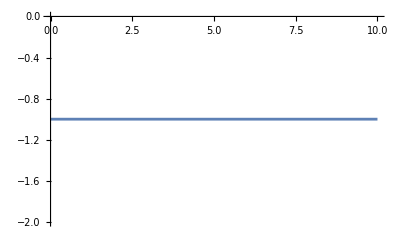

```mathematica
Plot[f[x],{x,0,10}]
```

#### Adding more definitions

Let us now add another definition to our function, so that it will give 2 on every even number:

```mathematica
f[x_Integer?EvenQ]:=2;
```

Check now:

```mathematica
{f[1],f[1.5],f[2],f[2.5],f[4],f[Pi],f[E]}
```

{1,-1,2,-1,2,-1,-1}

```mathematica
?f
```

#### Changing definitions selectively

The above pattern-based mechanism of function definitions allows them to be very flexible. In particular, it is quite possible to change or delete a given definition corresponding to the specific pattern, without introducing changes in other definitions associated with this function.

To change an already existing definition for some pattern, to a new one, one just needs to redefine a function on this particular pattern with a new right hand side. For example, we want our first definition for <f> from the previous example to return not 2, but 4 on even numbers. We simply redefine:

```mathematica
f[x_Integer?EvenQ]:=4;
```

Observe:

```mathematica
?f
```

It is not required that the pattern tags (names) in a new pattern are literally the same as those for the old one (but otherwise the patterns have to be the same if we want to replace old definition with the new one):

```mathematica
f[y_Integer?EvenQ]:=6;
```

Check now:

```mathematica
?f
```

As we see, the old definition still got replaced by a new one, since the pattern essentially did not change, and Mathematica can see that (this wasn’t the case in some early versions).

#### Warning: a common mistake

It is quite common during the development of some function to change the patterns for the function’ s arguments. However, if one does not remove the old definition, it will remain in the rule base and may lead to errors when testing the function. Always make sure that you clear old definitions when you change a definition (argument patterns) of the function you are developing. One way to automate this is to always start with a line Clear[f] before any definition for <f> is entered - this is the practice I usually adhere to.

#### Selective removal of the definitions

If we would like to remove the definition of the function <f> associated with some pattern <pattern>, there is a special built - in command tailor - made for this: Unset. Its short - hand notation is <= .> (equal dot). Thus, we have to use either f[pattern] =., or Unset[f[pattern]]. This will remove a given definition.

Let us for instance remove a first definition of the above function <f> . This is done as follows:

```mathematica
f[y_Integer?EvenQ]=.
```

We now check:

```mathematica
?f
```

As a side remark, it is interesting that the above possibilities of selective changes and/or removals of function definitions can be used in quite an unusual way: the function itself may (temporarily, for instance) change part of its own definitions during its execution. One reason why this may be useful is that sometimes it is a possible workaround to avoid an infinite recursion.

#### Case study: changing the weights of words

The problem

Consider some set of words, on pairs of which we will define a model “mutual attraction” function which will be equal to the number of common letters in the given pair of words. As a model set of words we will take the one we have used already:

```mathematica
wlist=ToLowerCase/@{"Most","of","this","Part","assumes","no","specific", "prior", "knowledge",  "of", "computer", "science", 
"Nevertheless",  "some",  "of",  "it", "ventures",  "into", 
"some","fairly","complicated","issues","zou","can","'probably","ignore","these","issues","unless","they","specifically","affect","programs","you","are","writing"};
```

The solution

Our function will be a function of two strings-words. It is very easy to write-split words to characters, and compute a length of the intersection of the character lists:

```mathematica
Clear[wordFunction];
wordFunction[x_String,y_String]:=Length[Intersection[Characters[x],Characters[y]]];
```

For example:

```mathematica
wordFunction["word","word"]
```

4

Testing the solution

Let us now make a list of our words together with the weights that these words have with respect to some fixed word, say “computer”:

```mathematica
wlist1=Table[{wlist[[i]],wordFunction["computer",wlist[[i]]]},{i,Length[wlist]}]
```

{{most,3},{of,1},{this,1},{part,3},{assumes,3},{no,1},{specific,3},{prior,3},{knowledge,2},{of,1},{computer,8},{science,2},{nevertheless,3},{some,3},{of,1},{it,1},{ventures,4},{into,2},{some,3},{fairly,1},{complicated,6},{issues,2},{zou,2},{can,1},{'probably,3},{ignore,3},{these,2},{issues,2},{unless,2},{they,2},{specifically,3},{affect,3},{programs,4},{you,2},{are,2},{writing,2}}

We can now sort the words according to the highest weight:

```mathematica
Sort[wlist1,#1[[2]]>#2[[2]]&]
```

{{computer,8},{complicated,6},{programs,4},{ventures,4},{affect,3},{specifically,3},{ignore,3},{'probably,3},{some,3},{some,3},{nevertheless,3},{prior,3},{specific,3},{assumes,3},{part,3},{most,3},{writing,2},{are,2},{you,2},{they,2},{unless,2},{issues,2},{these,2},{zou,2},{issues,2},{into,2},{science,2},{knowledge,2},{can,1},{fairly,1},{it,1},{of,1},{of,1},{no,1},{this,1},{of,1}}

Manipulating weights of individual words

Suppose now that we want to bring some words up in the list, that is, change the “strength function” of these words with the word “computer” by hand. Such new definitions can be implemented according to the above described scheme - we just have to add specific definitions of our weight function on specific words. Let these words be “programs”, “knowledge” and “science”. Let us give them weights:

```mathematica
wordFunction["computer","programs"]=20;
wordFunction["computer","science"]=15;
wordFunction["computer","knowledge"]=10;
```

Now let us have a look on the new definitions of <wordFunction>:

```mathematica
?wordFunction
```

Let us note two things: first, in these latter definitions we used Set rather than SetDelayed (it does not matter much for constant r.h.s.), and second, that these definitions are placed before the more general one even though they were added later - Mathematica figured out their level of generality and positioned them accordingly. This means that they will be applied before the more general one, and thus the general one does not “threaten” the more specific ones. Let us check now:

```mathematica
Sort[Table[{wlist[[i]],wordFunction["computer",wlist[[i]]]},{i,Length[wlist]}],#1[[2]]>#2[[2]]&]
```

{{programs,20},{science,15},{knowledge,10},{computer,8},{complicated,6},{ventures,4},{affect,3},{specifically,3},{ignore,3},{'probably,3},{some,3},{some,3},{nevertheless,3},{prior,3},{specific,3},{assumes,3},{part,3},{most,3},{writing,2},{are,2},{you,2},{they,2},{unless,2},{issues,2},{these,2},{zou,2},{issues,2},{into,2},{can,1},{fairly,1},{it,1},{of,1},{of,1},{no,1},{this,1},{of,1}}

Now let us remove these definitions:

```mathematica
wordFunction["computer","programs"]=.;
wordFunction["computer","science"]=.;
wordFunction["computer","knowledge"]=.;
```

We check now:

```mathematica
?wordFunction
```

Only the general one remains.

Automating the process (advanced)

It is interesting that the process of giving new definitions to some function can be automated by another function. In particular, let us define:

```mathematica
Clear[giveDefinitions];
giveDefinitions[f_,args_List,values_List]/;Length[args]==Length[values]:=(MapThread[Set,{Unevaluated[f[Sequence@@#]]&/@args,values}];);
```

This function is quite general (although one may write it more efficiently): it takes the name of another function, a list of arguments and a list of values, and creates the new definitions for the supplied function accordingly. At the same time, any other definitions of this function will not be affected. This is our example:

```mathematica
giveDefinitions[wordFunction,{{"computer","programs"},{"computer","science"},{"computer","knowledge"}},{20,15,10}]
```

We check now:

```mathematica
?wordFunction
```

The technique just illustrated allows some functions to manipulate the definitions of other functions, which allows us to control the program execution in a very flexible way.

Functions like <giveDefinitions>, which in effect manipulate other functions, are called higher-order functions. Their use is quite common in the functional programming style. We will cover a lot of built-in higher-order functions in the chapter V.

### Larger functions, local variables and the code modularization

In the majority of real situations, the code for a typical function is longer than one or two lines (in other words, not every problem can be solved by one-liners). Also, it is often convenient to introduce intermediate variables, both to avoid redundant computations and to improve the code readability. Such variables one has to localize, in order to avoid name conflicts with the global variables already defined in the system, and in general not to “pollute” the global name space. On the scale of a single function or program, there are 3 constructs in Mathematica which provide this functionality: Module, Block and With. These constructs are explained in detail in Mathematica Book and Mathematica Help, so I will say just a few words about them here. On the larger scale, this is supported through the system of packages - we will
consider them in part II.

#### Module

The goal of Module is to localize names of the variables, and avoid the name conflicts between the global names (and by global I mean everything exterior to the body of the Module), and the local names used in the code inside Module. What is important is that if this code calls some function which contains one of the global symbols with the name coinciding with the name of some of the local variables, the global value will be used. Put in another way, the variables are localized in space - only in the code inside Module, but not in functions which may be called from within this Module. The way Module does it is to create temporary variables with names which can not possibly collide with any other name (but see Mathematica Book for some subtleties). In fact, the workings of Module correspond most directly to standard variable scopes
in other languages such as C.

The format of Module is Module[{var1, var2, ...}, body], where var1, var2, ... are the variables we localize, and <body> is the body of the function. The value returned by Module is the value returned by the last operator in the <body> (unless an explicit Return[] statement is used within the body of Module. In this case, the argument of Return[arg] is returned). In particular, if one places the semicolon after this last operator, nothing (Null) is returned. As a variant, it is acceptable to initialize the local variables in the place of the declaration, with some global values: Module[{var1 = value1, var2, ...}, body]. However, one local variable (say, the one “just initialized” can not be used in the initialization of another local variable inside the declaration list. The following would be a mistake: Module[{var1 = value1, var2 = var1, ...}, body]. Moreover, this will not result in an error, but just the global value for the symbol <var1> would be used in this example for the <var2> initialization (this is even more dangerous since no error message is generated and thus we don’t see the problem). In this case, it would be better to do initialization in steps: Module[{var1=value1,var2,...}, var2=var1;body] , that is, include the initialization of part of the variables in the body of Module.

One can use Return[value] statement to return a value from anywhere within the Module. In this case, the rest of the code (if any) inside Module is slipped, and the result <value> is returned.

One difference between Module and the localizing constructs in some other programming languages is that Module allows to define not just local variables, but local functions (essentially, this is because in Mathematica there is no strong distinction between the two). This opens new interesting possibilities, in particular this is useful for implementing recursive functions. The same comment holds also for the Block construct.

A simple example: here is a function which computes the sum of the first <n> natural numbers:

```mathematica
Clear[numberSum];
numberSum[n_Integer]:=Module[{sum=0,i},For[i=1,i<=n,i++,sum=sum+i];sum]
```

```mathematica
numberSum[10]
```

55

```mathematica
{i,sum}
```

{5001,sum}

#### Block

Turning to the Block construct, it is used to localize the values of variables rather than names, or, to localize variables in time rather than in space. This means that in particular, if any function is called from within the Block (not being a part of the code inside this Block), and it refers globally to some of the variables with names matching those localized by Block, then the new (local) value for this variable will be used (this is in sharp contrast with Module). Block can be used to make the system temporarily
“forget” the rules (definitions) associated with a given set of symbols.

The syntax of Block is similar to the one of Module. However, their uses are really different. While I will not go into further detail here (we will revisit scoping constructs in the part II), the quick summary is that it is usually more appropriate to use Module for localizing variables, and Block to temporarily change certain values. In particular, using Block instead of Module may result in errors in some cases. In general, if you use Block to localize a value of some variable, you have to make sure that no unforeseen variables with accidentally the same name will be involved in entire computation happening inside this Block, including possible (nested) calls of external functions which use these variables as global ones.

Here is some simple example with Block:

```mathematica
Clear[a,i];
a:=i^2;
i=3;
a
Block[{i=5},a]
```

9

25

We see that the value of <a> changed inside block, even though <a> was defined with the global <i> outside the Block, and no explicit reference to <i> is present inside the Block.

It is worth mentioning that several built-in commands such as Do, Table, Sum and a few others, use Block internally to localize their iterator variables. This means that the same caution is needed also when one uses these commands as with the Block itself. We have already discussed this issue for Table (section 3.4.3) and Do (section 2.8.3).

#### With

The last scoping construct is With, and it is very different from both Block and Module. It is used to define local constants. With [{var1 = value1, ...}, body] is used to textually substitute the values <value1> etc in every place in the <body> where <var1>, etc occur. In some sense With is closer in spirit to the C preprocessor macros. In particular, it is not possible to modify the values given to the “variables”
<var1> etc during the declaration, anywhere else inside With, since the occurrences of <var1> etc are textually substituted with the values <val1> etc before any evaluation takes place. For example, the following code:

```mathematica
With[{i=2},i=3]
```

is just equivalent to a direct attempt of assigning the value 3 to 2:

```mathematica
With[{i=2},i=3]//Trace
```

Set::setraw: Cannot assign to raw object 2.

{With[{i=2},i=3],2=3,{Message[Set::setraw,2],{Set::setraw,Cannot assign to raw object `1`.},{MakeBoxes[Set::setraw: Cannot assign to raw object 2.,StandardForm],TemplateBox[{Set,setraw,"Cannot assign to raw object \!\(\*RowBox[{\"2\"}]\).",2,1125,78,26587777319895376970,Local},MessageTemplate]},Null},3}

The With construct is very useful in many circumstances, particularly when some symbols will have a constant value throughout the execution of some piece of code. Since these values can not be changed once initialized by With, it improves the code readability because it is easy to find the place where the symbols are defined, and then we know that they will not change. There are also more advanced applications of With, some of which we will discuss later (for example, one such application is to embed parameters into functions which are created at run-time).

The scoping constructs Block, Module and With can be nested arbitrarily deep one within another. Possible name conflicts are resolved typically in such a way that the more “internal” definitions have higher priority. Mathematica Book contains a lucid discussion of the subtleties associated with name conflicts in nested scoping constructs.

### Function attributes

Apart from the definitions, functions can be assigned certain properties which affect the way they are executed. These properties are called Attributes. There are many possible attributes which a function may have, and we will only briefly discuss very few of them here. It is important that all possible attributes are only those built in Mathematica, and one can not assign to a function a “home-made” attribute that Mathematica does not know.

#### Listable attribute and SetAttributes command

A simple example

This attribute is used when we want our function to be automatically threaded over any lists passed to it as arguments. For example, let us define a function which will square its argument and will also work on lists:

```mathematica
Clear[flst];
flst[x_]:=x^2;
SetAttributes[flst,Listable];
```

Notice how we set the attributes: we use the SetAttributes built-in function. Let us check:

```mathematica
testlist=Range[10]
testlist1=Range/@Range[5]
```

{1,2,3,4,5,6,7,8,9,10}

{{1},{1,2},{1,2,3},{1,2,3,4},{1,2,3,4,5}}

```mathematica
flst[testlist]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
flst[testlist1]
```

{{1},{1,4},{1,4,9},{1,4,9,16},{1,4,9,16,25}}

Careful with the Listable attribute

As we can see, listability leads to function working also on nested lists. In fact, this is not always the desired behavior. For example, here we have a function that takes an interval and computes its length:

```mathematica
Clear[intervalLength];
intervalLength[{start_,end_}]:=end-start;
```

We now want it to work on a list of intervals and add the Listable attribute:

```mathematica
SetAttributes[intervalLength,Listable];
```

Now we use it on a list of intervals:

```mathematica
intervalLength[{{1,4},{2,7},{5,10}}]
```

{{intervalLength[1],intervalLength[4]},{intervalLength[2],intervalLength[7]},{intervalLength[5],intervalLength[10]}}

We see that listability made our function go all the way to the elements which are not lists - but this is not we want. So, if you attach a listable attribute to a function, make sure that its normal arguments are not lists.

A way out in some cases

As another example of the similar kind, consider a following one: we are given some function , say <f>, and two lists , say {1, 2} and {3, 4, 5}, and wish the output be a list: {f[1, {3, 4, 5}], f[2, {3, 4, 5}]} - that is, to thread <f> over the first list but not the second. For the same reason as above, the straightforward attempt to assign a listable attribute to <f> will fail:

```mathematica
ClearAll[f];
SetAttributes[f,Listable];
f[{1,2},{3,4,5}]
```

Thread::tdlen: Objects of unequal length in f[{1,2},{3,4,5}] cannot be combined.

f[{1,2},{3,4,5}]

I can’ t help showing here a hack which solves this sort of problems and which is related to the use of Listable SubValues, although it is perhaps a bit too advanced at this point.The idea is that we will create a higher-order function which will take <f>, and both of our lists as parameters. Here is the code:

```mathematica
ClearAll[listThread];
listThread[f_,x_,y_]:=Module[{auxf},Attributes[auxf]={Listable};auxf[t_][z_]:=f[t,z];Through[auxf[x][y]]];
```

Check:

```mathematica
ClearAll[f];
listThread[f,{1,2},{3,4,5}]
```

{f[1,{3,4,5}],f[2,{3,4,5}]}

What happens here is that an auxiliary function is defined inside Module, but if you look carefully at its definition you will realize that it corresponds to global rules stored in SubValues rather than DownValues (section 2.2.5), because the function <auxf[x]>, considered as a function of <y>, has a composite (non-atomic) head. Setting the Listable attribute to <auxf> will then only affect the “first” argument <x>, but not <y> . Note also that neither <t> nor <z> needs to be localized since SetDelayed is used in the definition, and thus they are local to the auxiliary function scope automatically. The Through operator is needed here as well - it is covered at the end of chapter V.

This trick is trivial to generalize to the total <n> number of arguments, out of which you need your function to be Listable on <k>: just place these <k> first - in the place of our <t>, and the rest - in the place of <z>: auxf[arg1...argk][arg(k+1)...argn].

Be aware of Listable built-in functions

There are at least two good reasons to check for a Listable attribute of a built-in function you wish to use.

First, to avoid errors of the type described above, which result from the assumption that the function is not Listable when in fact it is. A classic example here would be an attempt to sum two nested lists of the same length, but where lengths of sublists in the two lists are different:

```mathematica
{{1,2},{3,4,5},{6}}+{{1},{2,3},{4,5,6}}
```

Thread::tdlen: Objects of unequal length in {1,2}+{1} cannot be combined.

Thread::tdlen: Objects of unequal length in {3,4,5}+{2,3} cannot be combined.

Thread::tdlen: Objects of unequal length in {6}+{4,5,6} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

{{1}+{1,2},{2,3}+{3,4,5},{6}+{4,5,6}}

This result is such (error messages) because summation operator Plus is Listable. For the record, Listable attributes, among others, can be removed or temporarily disabled to avoid problems like this, for both user-defined and built-in functions. We will see such an example in chapter V.

The second reason to be aware of Listable attributes for built-ins is to be able to write more efficient code. If some built-in function is Listable and one has to thread it over a list, it will almost certainly be faster to feed it an entire list rather than to thread (map) it by hand with commands such as Table or Map. This is so just because more operations will then be “pushed” into the kernel. For user-defined functions however there will be no significant difference in most cases, so this comment refers to built-ins.

As an example, consider computing some function numerically on a list of first 50000 natural numbers. Here is implementation using Table:

```mathematica
Table[N[Exp[Sin[i]^3]],{i,50000}]//Short[#,3]&//Timing
```

{0.00579,{1.81452,«49998»,0.368056}}

Here we use Listability of all the functions (Sin, Exp, Power) to compute the result on entire list. We win a factor of 7-10 (an order of magnitude) in performance.

```mathematica
Exp[Sin[N[Range[50000]]]^3]//Short[#,3]&//Timing
```

{0.000344,{1.81452,2.12087,«49997»,0.368056}}

#### Clearing Attributes - the ClearAll command

Now suppose we would like to give our function <flst> from the previous example another definition, and also no longer want it to have a Listable attribute (in fact, we want to remove all attributes attached to the symbol <flst>). First thing we may try is just to use Clear command, as we usually do:

```mathematica
Clear[flst];
flst[{1,2,3,4,5}]
```

{flst[1],flst[2],flst[3],flst[4],flst[5]}

We see that while the definition of <flst> has been cleared, the Listable attribute remains. To remove both the definitions and the attributes attached to a given symbol, use ClearAll instead of Clear:

```mathematica
ClearAll[flst];
flst[{1,2,3,4,5}]
```

flst[{1,2,3,4,5}]

Let me stress that ClearAll serves to clear all definitions (including attributes) for a given symbol (or symbols), and not to clear definitions of all global symbols in the system (it is a common mistake to mix these two things).

#### Orderless attribute

This attribute states that the result of evaluation of a given function should not depend on the order of its arguments, which is commutativity. The presence of this attribute does change the evaluation of the function, because then the argument list is sorted (by default Mathematica sorting function) before the actual evaluation process for this function starts. Many built-in functions such as Plus or Times (or, in general, commutative functions) have this attribute. As an example, we can arrange sorting of a list (with the default sorting criteria) by just defining a “container function” with such an attribute:

```mathematica
ClearAll[fsort];
SetAttributes[fsort,Orderless];
```

```mathematica
testlist=Table[RandomInteger[{1,15}],{20}]
```

{14,1,12,11,3,13,8,14,15,10,1,4,2,4,12,14,12,7,7,15}

```mathematica
Apply[fsort,testlist]
```

fsort[1,1,2,3,4,4,7,7,8,10,11,12,12,12,13,14,14,14,15,15]

The meaning of Apply will be clarified in the chapter V. Its role here is to “eat up” the List head so that the <fsort> receives a sequence of arguments rather than a list.

#### Flat attribute

This attribute is used to implement associativity. This means that for example expression like f[a,b,f[c,d,e,f[f[g,h]]],i,f[f[j]]] will be automatically simplified to f[a,b,c,d,e,f,g,h,i,j] if the symbol <f> has a Flat attribute. Previously we considered a rule-based way to mimic this functionality in a very special case when the function has a property that f[f[f[...f[x]]]]] = f[x]. With a Flat attribute this is trivial since the
system does all the work. For instance:

```mathematica
ClearAll[f,x];
testlist=NestList[f,x,5]
```

{x,f[x],f[f[x]],f[f[f[x]]],f[f[f[f[x]]]],f[f[f[f[f[x]]]]]}

Now we set the Flat attribute to the function <f>:

```mathematica
SetAttributes[f,Flat];
```

```mathematica
testlist
```

{x,f[x],f[x],f[x],f[x],f[x]}

And our first example:

```mathematica
Clear[a,b,c,d,e,g,h,i,j];
f[a,b,f[c,d,e,f[f[g,h]]],i,f[f[j]]]
```

f[a,b,c,d,e,g,h,i,j]

By the way, setting the attributes is largely independent from giving definitions to a function. The non-trivial dependencies arise in some cases, and generally one has to set up attributes before any definitions are given to the function. However, often there is no need to satisfy such strict requirements (but you have to know precisely what you are doing, of course). In particular, some attributes may be set when the function has already been defined for a while and perhaps used, attributes may also be set temporarily, or selectively removed. In fact, as an extreme case, a function may be programmed in such a way that it itself temporarily removes, changes or restores its own attributes (this is however a really exotic example).To remove a given attribute, one has to use ClearAttributes. The current list of attributes can be monitored with the Attributes built-in command:

```mathematica
Attributes[Plus]
```

{Flat,Listable,NumericFunction,OneIdentity,Orderless,Protected}

#### Protected attribute

This attribute is needed if we want to protect a given function or symbol against changes that the user or some user program may wish to apply to it. Most system functions have the Protected attribute. For example, when we try something like this assignment:

```mathematica
a+b=c
```

Set::write: Tag Plus in a+b is Protected.

c

The FullForm Plus[a, b] = c tells us that we are trying to make a new rule (definition) for the built-in Plus command, which is protected. Of course, our assignment fails.

It is possible to make a symbol Protected by using the built-in command Protect and to unprotect the symbol by using the built-in command Unprotect. This is often handy. Protecting your own symbols is a standard practice when writing packages (which are system extensions to some domain), while unprotecting is used usually with built-in commands when we need to add some new rule to the definition of this or that built-in command. As an example, we may Unprotect Plus command so that the above assignment will work:

```mathematica
Clear[a,b,c];
Unprotect[Plus];
Plus[a,b]=c;
Protect[Plus];
```

We can check now:

```mathematica
a+b
```

c

The reason we can redefine the behavior of system functions is that the user-defined rules have higher priority than the system ones. But what we just did was in this case not motivated by any serious need and thus represents an act of vandalism. Besides, even in cases when the workings of the built-in functions have to be modified, modifying their DownValues (adding rules as above) is really a last resort. There are
softer ways of getting what one needs, such as using UpValues for the symbol you define. I will have more to say about this later. For now, then, let us remove our definition:

```mathematica
Unprotect[Plus];
Clear[Plus];
Protect[Plus];
a+b
```

a+b

#### Attributes are properties of symbols

I would like to stress that while we may interpret many attributes to be properties of functions, they are really properties of symbols (function names for functions). Function definitions are rules associated also with symbols (function heads or names). There is no fundamental distinction between rules describing functions and just some symbolic rewritings, as we have already discussed a few times. The technical distinction is that say rules for symbols are kept as OwnValues and rules for functions in DownValues (and UpValues and SubValues which we did not cover yet), but the main point is the same: there are symbols and associated with them global rules and properties. Whether we interpret these symbols as function names or something else is up to us.

#### Attributes HoldFirst, HoldRest and HoldAll

The meaning of argument holding

These attributes are used when some of the function arguments have to be evaluated only after the rules associated with the function name have been applied. This means that these attributes change the evaluation order from standard evaluation (depth-first, subexpressions before expressions) to a non-standard one (expressions before subexpressions). One usually needs to change the evaluation order to do something non-trivial. In particular, as we have seen already on the example of the increment function <inc[x]> (sections 2.5.5, 4.5.2), Hold attributes can be used to mimic the pass-by-reference semantics. This allows functions to modify the variables which are passed to them. Other cases when one needs to hold some arguments unevaluated arise when only some of the arguments have to be evaluated at all, and which ones
have to be evaluated is decided by say a condition on the part of arguments that are evaluated (this is exactly the situation with conditional operators such as If).

The attribute HoldFirst instructs a function to hold (in unevaluated form) the first argument. HoldRest instructs to hold all but the first argument, and HoldAll instructs to hold all arguments. The fact that the argument is held unevaluated does not necessarily mean that it is never evaluated in a function (which may also happen if it is discarded before it is evaluated) - it simply means that it is evaluated after all the transformations of this argument by the function <f> ( according to the definition of <f>) are performed. As a simple example, consider a squaring function:

```mathematica
ClearAll[f];
f[x_]:=x^2;
```

Let us Trace its evaluation on some number:

```mathematica
Clear[a];
a=5;
f[a]//Trace
```

{{a,5},f[5],5^2,25}

We see that <a> was evaluated before <f> . Now let us attach the HoldFirst attribute to <f>:

```mathematica
SetAttributes[f,HoldFirst];
```

Now:

```mathematica
f[a]//Trace
```

{f[a],a^2,{a,5},5^2,25}

We see that now the evaluation order has changed: first the function <f> was evaluated, and then the value of <a> was substituted. In this simple example, the end result was the same regardless of the evaluation order, but in less trivial cases the evaluation order becomes important.

It is fairly easy to give an example of held arguments being discarded and thus not evaluated at all - take any operators on the False branch of some If operator.

Advanced topic: Hold attributes and pattern-matching

While the general topic of Hold attributes is a bit too advanced for us now (since it requires a much more thorough discussion of the evaluation process), let me mention one important point. This is, Hold attributes affect pattern-matching. Consider the following function.

```mathematica
ClearAll[f];
f[x_Sin]:=x^2;
f[x_]:="Not sine"
```

It is supposed to square any expression of the form Sin[anything], and issue a message for all other inputs. We can try it:

```mathematica
Clear[a,b];
{f[Sin[a]],f[a],f[Sin[Pi]]}
```

{Sin[a]^2,Not sine,Not sine}

In the last input, Sin[Pi] was evaluated first, leading to f[0], which led to a “Not sine” message. Let us now add the attribute:

```mathematica
SetAttributes[f,HoldFirst];
```

And test the same input again:

```mathematica
Clear[a,b];
{f[Sin[a]],f[a],f[Sin[Pi]]}
```

{Sin[a]^2,Not sine,0}

What happened with the last output is that the presence of Hold attribute made a function to evaluate “branches before leaves”, and then it had a chance to “see” Sin[Pi] before it evaluated to 0, and thus the first definition applied.

All right, this is all known stuff, we discussed the non-standard evaluation before. But now, let us do it a bit differently:

```mathematica
Clear[a,b];
a=Sin[b];
{a,f[a]}
```

{Sin[b],Not sine}

For us, it is obvious that <a> is Sin[b], so this behavior looks like a bug. It isn’t however: Hold attribute means that the argument is held unevaluated before the rules associated with the function apply. If we supply the direct Sin[something], then, while Sin[something] is not evaluated, the function can test the head of the argument (which is Sin) and thus the first definition (associated with Sin[something]) applies.
If however the value of the expression is stored in another variable, then by the time the pattern-matching takes place, there is no way for the function to test the head of an expression Sin[b] - all it has is a symbol <a> (again because <a> this time is held unevaluated) . This behavior may lead to rather subtle bugs in user-defined functions which use Hold attributes. One way out in this case would be to redefine the function as follows:

```mathematica
ClearAll[f];
f[x_]/;Head[Evaluate[x]]===Sin:=x^2;
f[x_]:="Not sine";
SetAttributes[f,HoldFirst];
```

Here, by using Evaluate, we override the Hold attribute in that particular place and instruct the argument inside Head command to be evaluated. Now:

```mathematica
Clear[a,b];
a=Sin[b];
{a,f[a]}
```

{Sin[b],Sin[b]^2}

The case with a Sin[Pi] is lost however:

```mathematica
f[Sin[Pi]]
```

Not sine

If we think of it, this is still a more logical behavior, since it is more logical (or should I say more robust) to test the head of fully evaluated expression than the one which will evaluate to something else. If one wants to catch both cases (something that was Sin[expr] or something that will become Sin[expr]), this is also possible:

```mathematica
ClearAll[f];
f[x_]/;Head[Evaluate[x]]===Sin:=x^2;
f[x_Sin]:=x^2;
f[x_]:="Not sine";
SetAttributes[f,HoldFirst];
```

```mathematica
{f[a],f[Sin[Pi]]}
```

{Sin[b]^2,0}

One may ask when in practice do such situations occur. More often than one may think, in fact. As a simple example, an expression may be assigned to a local variable in one function, which then passes this variable (with the “pass-by-reference” semantics) to another function which is supposed to both do a type-check and subsequently modify this variable. Such cases are relatively rare just because pass-by-reference semantics and in-place modifications are rarely used in “usual” Mathematica programming, but once you choose to program in this style (which occasionally is a good option), these sorts of problems will pop up much more often.

Hold attributes and built-in functions

Many built-in commands have Hold attributes. For instance, the Set command has a HoldFirst attribute, since otherwise its l.h.s. would evaluate before Set will have a chance to assign anything to it (in case when the variable in the l.h.s. has a global value). SetDelayed has attribute HoldAll, since it does not evaluate also the r.h.s. of an assignment. Constructs such as Module, Block and With also have the Hold-All attribute, since they have to hold the code they enclose unevaluated until the naming conflicts are resolved. We could go on with this list, but let us just say once again that these attributes are very important.

#### Attributes and the evaluation process

As we have discussed before, the evaluation process can be roughly represented by a repeated application of all available global rules to an expression and all of its parts, until the result no longer changes. We also mentioned that this is a very oversimplified picture. Now we can at least outline some other ingredients
which make the evaluation process more complex.

One of such ingredients is the existence of attributes. You can not assign attributes in the form of local rules - they are essentially global properties of symbols. The presence or absence of attributes for a given symbol affects the way the expression involving this symbol is evaluated.

Another ingredient is the interplay of standard and non-standard evaluation. This is partly related to attributes through Hold attributes, but there are other ways to switch between standard and non-standard evaluation, such as using commands like Evaluate, Unevaluated, Hold, HoldPattern, etc.

Yet another distinction is that there are many more types of global rules than there are local ones. While local rules are basically either immediate (Rule) or delayed (RuleDelayed), global rules are additionally categorized by being OwnValues, DownValues, SubValues, UpValues, NValues or FormatValues (the latter three we did not have a chance to discuss yet). The category to which the global rule belongs, determines the way and order in which it is applied.

So, while the evaluation process generally is the repeated rule application, we can now see a bit better more of the ingredients that make it different and perhaps somewhat more complex than just a repeated application of all global rules.

### Advanced topic: parameter passing and local variables

In this section we will have a brief discussion on the interplay of parameter-passing and localization of variables with scoping constructs Module, Block and With and Function, which we promised in the section on the parameter passing (4.4.7).

It turns out that the situation is very similar for all these constructs, so we will discuss the Module case only. The main question is what happens if the name of some of the formal parameters coincides with a name of one of the local variables. Let me say straight away that this is a really bad practice which should be avoided since it brings nothing except bugs into the programs. Let us consider a simple example:

```mathematica
Clear[fM,a];
a=5;
fM[x_]:=Module[{x=10},Print[x]];
```

Here we set up a function <fM> with conflicting names of the parameter and a local variable, and just a global variable <a> assigned some value. Now we try a couple of inputs:

```mathematica
fM[5]
```

Module::lvset: Local variable specification {5=10} contains 5=10, which is an assignment to 5; only assignments to symbols are allowed.

Module[{5=10},Print[5]]

We see what happened: the value for a formal parameter <x> (5 in this case) was textually substituted in all places where the literal <x> appears on the r.h.s., before any other evaluation (and name conflict resolution in Module in particular) took place. This is in full agreement with the general parameter-passing mechanism described earlier (section 4.4.7). But then, by the time Module actually started executing, we see what was inside - in particular, instead of the local variable initialization, we had in the variable declaration block a statement 5 = 10, which triggered an error message and resulted in Module returning unevaluated.

Conclusion: it is an error to make a name of a local variable coincide with the name of any of the function parameters.

We now try to call our function on a variable rather than a raw expression:

```mathematica
fM[a]
```

Module::lvset: Local variable specification {5=10} contains 5=10, which is an assignment to 5; only assignments to symbols are allowed.

Module[{5=10},Print[5]]

The results are identical, because <a> evaluated to <5> before the function was essentially called (recall the standard evaluation mechanism).

Next, let us see what happens when a function has a Hold attribute for the parameter in question. We modify our code accordingly:

```mathematica
Clear[FMHold];
Attributes[FMHold]={HoldAll};
FMHold[x_]:=Module[{x=10},Print[x,"  ",a,"  ",Unevaluated[a]]];
```

Here, we have included additional objects to be printed - in a second you’ ll see why. Now let us test:

```mathematica
FMHold[5]
```

Module::lvset: Local variable specification {5=10} contains 5=10, which is an assignment to 5; only assignments to symbols are allowed.

Module[{5=10},Print[5,  ,a,  ,Unevaluated[a]]]

The result here is essentially the same as before, because <5> is a raw object. Now let us see what happens if we call our function on a variable:

```mathematica
FMHold[a]
```

10  10  a$73757

This output is quite interesting. The last output gives us a name that was internally associated with <a> in our code inside Module. It tells us that in this case, the local variable was initialized, and has shadowed the global parameter being passed. It is instructive to see exactly how this happened:

Step 1: The symbol <a> in unevaluated form (due to a Hold attribute) is textually substituted everywhere where <x> stands inside the Module (r.h.s. of the function definition). At this point we have the code:

```mathematica
Module[{x=10},Print[x,"  ",a,"  ",Unevaluated[a]]]
```

Step 2: A local variable <a> with a special name is initialized, and all occurrences of the symbol <a> in the code of Module are then associated with this local variable - just as if we had entered the above code from the keyboard.

Step 3: It is only at this point that the function would try to evaluate the passed parameter (since it was held unevaluated so far), but by this time all occurrences of <a> already correspond to the initialized local variable, which thus completely shadows the passed parameter value.

Step 4: The code is executed in the above form, with the results we just saw. The conclusion is that if a given parameter is held by the function and if the passed object happened to be a global symbol with the head Symbol, then the parameter being passed is shadowed by a local variable.

This behavior looks more mild than the one before, but in fact it is worse. Because really, colliding names in this fashion is a bad mistake in both cases, but here it may go unnoticed, since it does not result in an explicit error.

If the passed held parameter is a composite expression, Module will at least generate an error message and return unevaluated, since it is illegal to name local variables in such way) .

```mathematica
FMHold[a[b]]
```

Module::lvset: Local variable specification {a[b]=10} contains a[b]=10, which is an assignment to a[b]; only assignments to symbols are allowed.

Module[{a[b]=10},Print[a[b],  ,a,  ,Unevaluated[a]]]

The final conclusions are these:

1. There is no mystery in what happens in parameter and local variable name collisions - all the outcomes can be easily explained by the core parameter-passing mechanism based on textual substitution.

2. It is always an error to collide the names like this, but there are cases when this error may go unnoticed, and the parameter value be shadowed by a local variable.

A good news is that in version 6 such name collisions are usually detected and highlighted in red by the front-end.

The final comment here: this situation is not too specific to Mathematica. In C, for instance, it is also an error to name a local variable after one of the function formal parameters, and will result in an undefined behavior (at least, here it is not undefined). It is a different matter that the passed parameters themselves may serve in C as local variables, unlike in Mathematica (see a discussion in 4.4.7).

### Pure functions

The notion of a pure function comes from the λ-calculus, and is widely used in functional programming languages, Mathematica in particular. From the practical viewpoint, the idea is that often we need some intermediate functions which we have to use just once, and we don’ t want to give them separate names. Pure functions allow to use them without assigning them names, storing them in the global rule base etc. Another application of them is that while they can be assigned to some symbols, they exist independently of their arguments and can be called just by name with the arguments being supplied separately, so that the “assembly” to the working function happens already at the place where the function is used. Finally, these functions may be dynamically changed and modified during the program’ s execution.

In Mathematica, the pure function can be defined in two (in principle, equivalent modulo some subtleties which we will discuss) ways: through the built-in function <Function> and through the so-called #-& notation (anonymous pure functions).

#### The #-& notation

We will first discuss the latter method. The idea behind it is to allow one to create functions which have no names and also no named arguments - completely anonymous pure functions. In this notation, the parameters of the function are denoted by sharp (#) plus the parameter index, like #1, #2, etc. If there is a single parameter, the index can be suppressed and we can just use #. The function ends with an ampersand <&>. It is recommended although not always required to put the entire function definition in parentheses (including the &), to avoid precedence-related bugs. This is because the ampersand & has a very low precedence and often a larger piece of code is interpreted as a part of the function definition, than meant by developer. This leads to bugs. One typical case where parenthesizing is absolutely necessary is when we provide a pure function as a sameness test in the SameTest option for the Union, Intersection or Complement commands.

Let us give some examples of pure functions.

Example: the squaring pure function

```mathematica
{(#^2&)[1],(#^2&)[2],(#^2&)[Pi],(#^2&)[10]}
```

{1,4,π^2,100}

The same can be done as follows:

```mathematica
ClearAll[f];
f=(#^2&);
```

```mathematica
{f[1],f[2],f[Pi],f[10]}
```

{1,4,π^2,100}

To understand, how a given pure function expressed in such a notation will work, one has to get used to it a little. In the beginning it often helps to substitute the real values of the arguments for parameters #.

Let us note that the internal representation of <f> is different from the one we had for functions which were defined with the help of patterns. In particular, there are no DownValues associated with f (which means, no rules associated with the form f[something]):

```mathematica
DownValues[f]
```

{}

Also, with this form of function definition, we can not associate several different definitions with the symbol f:

```mathematica
?f
```

We give a new definition:

```mathematica
f=#^4&;
?f
```

This was possible with patterns, because f[pattern1] and f[pattern2] are different symbols. In our present case however, the best way to think about it is to think that the variable <f> received some value, which turned out to be not a number or another variable, but a pure function. Such a “variable” interpretation is also consistent with the fact that the rule for <f> is stored in OwnValues rather than DownValues.

Example: function which takes the first element from the list

```mathematica
Clear[takeFirst];
takeFirst=#[[1]]&;
```

We check:

```mathematica
takeFirst[Range[10]]
```

1

Pure functions defined in the # - & notation usually work faster than the pattern-defined ones (there is no pattern-matching going on in this case), but they require more care. In particular, it is less easy to organize the argument checks for them (although also possible, of course). Let us, for example, apply our function to a number instead of a list:

```mathematica
takeFirst[1]
```

Part::partd: Part specification 1⟦1⟧ is longer than depth of object.

1⟦1⟧

To add the argument check, we would have to write something like this:

```mathematica
takeFirst=If[AtomQ[#],#,#[[1]]]&;
```

That is, to return the argument itself if it is an atom, and its first element if it is not:

```mathematica
{takeFirst[5],takeFirst[{3,4,5,6}]}
```

{5,3}

With the help of patterns, we could do the same as follows:

```mathematica
takeFirstP[x_/;Not[AtomQ[x]]]:=x[[1]];
```

```mathematica
{takeFirstP[5],takeFirstP[{3,4,5,6}]}
```

{takeFirstP[5],3}

Notice the difference in execution: when the pattern does not match, the function simply returns unevaluated. This allows to use the trick with the “soft” generation of error messages by adding a general catchall rule to catch all wrong arguments (see section 4.6.2.3 for an example). On the other hand, for pure functions, all cases have to be explicitly taken into account - in this sense they are more “rigid” entities.

Returning back to the previous example of the takeFirst function, we may indeed want it to remain unevaluated for atomic objects, rather than returning them. In this case, we really need a pattern-defined function.

Example: a function of two variables

This function returns an intersection of two sets:

```mathematica
Intersection[#1,#2]&
```

#1∩#2&

Let us use it:

```mathematica
Intersection[#1,#2]&[{1,2,3,4},{3,4,5,6}]
```

{3,4}

Example: building a matrix of rank 1 from two vectors

This function creates a matrix of rank 1 for the two given vectors:

```mathematica
Outer[Times,#1,#2]&
```

For example:

```mathematica
Clear[a,b,c,a1,b1,c1];
Outer[Times,#1,#2]&[{a,b,c},{a1,b1,c1}]
```

{{a a1,a b1,a c1},{a1 b,b b1,b c1},{a1 c,b1 c,c c1}}

Example: supplying a list with its length

This function supplies a list with its length:

```mathematica
{#,Length[#]}&
```

For example:

```mathematica
{#,Length[#]}&[{5,6,7,8,9,10}]
```

{{5,6,7,8,9,10},6}

In all these examples, the same results would be obtained if the real values of the arguments were substituted, as is easy to check.

If we supply a wrong number of arguments

If the pure function is given more arguments than it needs, extra arguments are ignored:

```mathematica
#[[1]]&[{1,2},{3,4}]
```

1

This property has both advantages and disadvantages. The advantage is that if some other (higher-order) built-in function takes a given pure function as an argument but supplies more arguments than needed, I don’ t need to modify my code (one such example is NestWhile when we need an access to more than just the most recent result - see chapter V).

The disadvantage is that one has to be extra careful. If the arguments were not supposed to be ignored, but the pure function is erroneous, such error is hard to catch. For comparison, for a pattern-defined function with the fixed number of arguments, for the wrong number of arguments the pattern simply won’t match
and the function will evaluate to itself (or, if one uses the trick with the catch-all pattern and error messages, the error message will be generated) - this situation is much better for debugging.

If, on the other hand, we supply less arguments than expected by the pure function, the error message will be generated:

```mathematica
(#1+#2)&[1]
```

Function::slotn: Slot number 2 in #1+#2& cannot be filled from (#1+#2&)[1].

1+#2

The Head and the FullForm of the pure function in #-& notation

The #-& form of a pure function is really just a convenient notation. The fundamental built-in function (head) used to create pure functions is always Function, as can be seen easily:

```mathematica
Head[#^2&]
```

Function

This is how this pure function looks internally:

```mathematica
FullForm[#^2&]
```

Function[Power[Slot[1],2]]

SlotSequence and functions with variable number of arguments

It is sometimes needed to define a function of many variables, where their number is either not fixed or when the variables are not needed to be referred to separately. In this case, one can use the SlotSequence, which has an abbreviation ##. As an example, we may define our own Plus function as a pure function in the following fashion:

```mathematica
Clear[ourPlus];
ourPlus=Plus[##]&;
```

We can check:

```mathematica
{ourPlus[1],ourPlus[1,2],ourPlus[1,2,3]}
```

{1,3,6}

It is less obvious, but one can also use SlotSequence even when one needs an access to individual variables. For example, we need a function which multiples its first argument by the sum of all the other ones, as a pure function. This does not seem possible to do since ## gives all arguments but does not directly allow to access the individual ones. This is not so however:

```mathematica
firstTimesSumRest=({##}[[1]]*Total[Drop[{##},1]]&);
```

```mathematica
{firstTimesSumRest[1],firstTimesSumRest[1,2],firstTimesSumRest[1,2,3],firstTimesSumRest[2,3,4,5]}
```

{0,2,5,24}

This shows how to access individual variables with SlotSequence - place ## in a list and then index the list. I deliberately ignored the variation of the SlotSequence which allows to supply first <n> arguments separately and the rest with SlotSequence, to illustrate the general way of accessing individual variables. With this variation, our function would be rewritten much more compactly as

```mathematica
firstTimesSumRest1=(#1*Plus[##2]&);
```

With the same results of course:

```mathematica
{firstTimesSumRest1[1],firstTimesSumRest1[1,2],firstTimesSumRest1[1,2,3],firstTimesSumRest1[2,3,4,5]}
```

{0,2,5,24}

This form of the function is certainly shorter, but less general since I will not be able to access say the third argument without the use of the trick with the list indexing shown above.

One important limitation of the #-& notation for the pure functions is that it is not possible to assign attributes to them in this notation (unless some undocumented features are used). The advantage however is that functions in this form are typically faster than in other forms (patter-defined or defined through the Function construct with named arguments).

A comment on function names

You may have noticed that I sometimes store the pure function definition in some variable. However, this is done purely for convenience in our examples, where I use these functions on several arguments, but don’ t want to use any of the functional programming constructs which automate function application. When we come to that point, you will see that we will never need names for pure functions.

Nesting pure functions in #-& notation

It often happens that inside one pure function there is another one, supplied to it as one of its arguments. The question is then whether or not we face any difficulties or ambiguities due to the same abbreviation for the function variables. As an example, consider a pure function which sorts its argument (list of lists is assumed), in an ascending order in the first elements of the sublists. This is how it will look like in the #-& notation:

```mathematica
Clear[sortFirstElem];
sortFirstElem=Sort[#1,First[#1]<=First[#2]&]&;
```

We see that the pure functions are nested one within another, and that there are two instances of #1 variable which have different meaning and, indeed, refer to different variables. Is it legal? The answer is yes, as long as one pure function is entirely contained in another one (more precisely, if there are no expressions such that for their evaluation, the variables of the nested functions have to be used together, simultaneously). Let us test it:

```mathematica
sortFirstElem[{{2,3},{1,4},{5,7},{3,8}}]
```

{{1,4},{2,3},{3,8},{5,7}}

Pure functions with zero arguments

This seems like a really weird construct, but it is in fact quite useful. Such functions are required basically when we want to supply some number or expression to a function as one of the arguments, while instead a function argument is expected. Then we need to “convert” our expression into an “idle” function, which will simply produce this expression regardless if its argument.

As a simple example, say we need to produce a list of ones, of the length 10: {1, 1, 1, 1, 1, 1, 1, 1, 1, 1}. This can be done by Table, of course, but alternatively by an Array command (which is somewhat faster). However, Array requires a function to be supplied, so the input like this:

```mathematica
Array[1,{10}]
```

{1[1],1[2],1[3],1[4],1[5],1[6],1[7],1[8],1[9],1[10]}

does not work, as we can see. The solution is to “convert” the number <1> into a pure function with zero arguments. This is extremely easy to do - just add an ampersand to the end:

```mathematica
Array[1&,{10}]
```

{1,1,1,1,1,1,1,1,1,1}

So, to summarize: adding an ampersand to the end of some expression (not involving anonymous variables - # symbols), converts this expression into a pure function with zero arguments, which is quite handy at times.

Currying (partial application) with pure functions in #-& notation

Currying means the following: given a function of <n> arguments and passing to it the smaller number of arguments <k> (k <n, and argument positions not necessarily consecutive), we insert these arguments into their “argument slots” and create a new function of the remaining variables at run-time. Sometimes this is also called partial application of the function. If, for instance, we have a function <f> of two variables <x> and <y> from the sets X,Y, producing some result <z> from the set Z, then f:X x Y -> Z, while what currying does is <curried f>: X-> (Y -> Z). Thus, while initial function maps a Cartesian product of X and Y onto Z, takes two arguments and maps them to a result (expression), curried function maps X onto a space of mappings (functions) Y->Z. The result of application of curried function is then always another function.

This technique is not very useful in procedural programming, since there it is the programmer himself who makes all the function calls. In the functional style however, we allow some functions to manipulate other functions, call them, etc. In this paradigm, it is quite often that one function expects another function as one of its arguments, and then frequently such a function does not exist and has to be created at run-time.

In some languages such as Ocaml, all functions are curried automatically. There is no built-in support for currying in Mathematica, but the compactness of the #-& notation makes it almost mindless to implement in each particular case. For example, say we have a function of two variables, to which we pass the first argument and then need to create a resulting function of a single (second) argument:

```mathematica
ClearAll[f];
f[x_,y_]:=Sin[x*y];
```

Say, the first argument is Pi. This is how we create such a function:

```mathematica
f[Pi,#]&
```

f[π,#1]&

For example:

```mathematica
f[Pi,#]&[1]
```

0

This technique trivially generalizes to more arguments. We will make real use of it in chapter V on functional programming.

#### Pure functions defined with Function

Now, let us describe another way of defining pure functions - through the Function construct. It has the format: Function[{vars}, body]. If there is a single variable, then the list braces are optional. Let us show how some of the previous examples would look in this notation:

The squaring function:

```mathematica
ClearAll[f];
f=Function[x,x^2];
```

```mathematica
{f[1],f[2],f[Pi],f[10]}
```

{1,4,π^2,100}

The function which take the first element:

```mathematica
Clear[takeFirst];
takeFirst=Function[x,If[AtomQ[x],x,First[x]]];
```

```mathematica
{takeFirst[a],takeFirst[{1,2,3}]}
```

{a,1}

Intersection of two sets (lists):

```mathematica
Clear[intSets];
intSets=Function[{x,y},Intersection[x,y]];
```

```mathematica
{intSets[{1,2,3},{2,3,4}],intSets[{1,2,3},{4,5,6}]}
```

{{2,3},{}}

Matrix of rank 1, built out of 2 vectors:

```mathematica
Clear[extMultiply,a,b,c,d,e,f];
extMultiply=Function[{x,y},Outer[Times,x,y]];
```

```mathematica
extMultiply[{a,b,c},{d,e,f}]
```

{{a d,a e,a f},{b d,b e,b f},{c d,c e,c f}}

#### Differences between pure functions defined with Function and with #-& notation

It is important to note that there is no fundamental difference between functions defined with the #-& notation and functions defined with the Function command, in the sense that both definitions produce pure functions. There are however several technical differences that need to be mentioned.

The first one is that the Function[{vars}, body] is a scoping construct, similar to Module, Block, With etc. This means in particular that the <vars> in the function body are localized to the body of the function, and have nothing to do with the global variables with same names, so we don’t need to worry about name conflicts when defining pure functions with Function. This also means that, should we wish to nest the Function constructs one inside another, the possible name conflicts will automatically be resolved by the system (but I would recommend to read the corresponding sections of Mathematica Book and Mathematica Help to see precisely how they are resolved). Also, with Function we may nest functions in more general way than with #-& notation, which is illustrated on the following example:

Example: currying

This is a function which takes an argument and produces another function. That function takes another argument and returns the sum of these two arguments

```mathematica
Clear[nestedF];
nestedF=Function[x,Function[y,x+y]]
```

Function[x,Function[y,x+y]]

For example, we may “forge” a function which adds 3 to its argument, like this:

```mathematica
add3=nestedF[3]
```

Function[y$,3+y$]

```mathematica
{add3[1],add3[5],add3[7]}
```

{4,8,10}

This is somewhat similar to a technique called currying in some languages. As this example illustrates, currying can be easily implemented in Mathematica through nested Function constructs, even though Mathematica does not support it directly.

We can of course use our function directly on the 2 arguments

```mathematica
nestedF[3][1]
```

4

This should not be considered a function of two arguments however, since the first number defines the function which then takes the second number as a single argument. In particular, the evaluation of this function will be different from the evaluation of the more standard function of two arguments that we described before.

Returning to our original question of comparison of the #-& style and the style with Function, it is not possible (to my knowledge) to implement the above functionality with the #-& style, since here we have nested pure functions with one not entirely contained in the other one (in the sense described above - we needed the variables of both internal and external function simultaneously to do the computation). Thus,
defining a pure function with Function is more general in this sense.

The other limitation of #-& approach, which we mentioned already, is that attributes can not be assigned to a pure function defined in this way (well, at least if one does not use undocumented features - see the section Attributes of Pure Functions in the Maeder’s book). This is not the case with Function: it takes an attribute or a list of attributes as an optional third argument, which is a powerful capability.

Example: an accumulator problem

To illustrate it, we will consider a model problem which Paul Graham used to argue in favor of functional languages (LISP).[13]: write a function, which takes an (integer) number <n>, and returns another function that takes any number and increments it by <n>. He emphasized 2 things: 1. returns a function, 2. this function not simply adds n to its argument, but increments it by n (that is, produces a side effects and changes a global value of the variable passed to it). Here is our solution:

```mathematica
Clear[incrementByN];
incrementByN[n_Integer]:=Function[x,x+=n,HoldFirst];
```

The conciseness of this solution arguably rivals the one in LISP. This was possible only because we could specify the HoldFirst attribute, which will actually allow the increment to be performed on the original variable rather than on what it would evaluate to. Let us now test it:

```mathematica
Clear[a,inc5];
a=10;
inc5=incrementByN[5];
inc5[a];
a
```

15

Example: the Listable SubValues hack revisited

In section 4.9.1.3, we considered a “hack” which solves the listability problem for a function in which not all list arguments have to be threaded upon. It involved introduction of an auxiliary function defined through SubValues. Here we consider an alternative (equivalent) implementation through the pure functions, which will be more compact.

I remind that the problem was for example to get the following evaluation: f[{1, 2}, {3, 4, 5}] -> {f[1, {3, 4, 5}], f[2, {3, 4, 5}]}. If we just give <f> Listable attribute, this won’ t work:

```mathematica
ClearAll[f];
SetAttributes[f,Listable];
f[{1,2},{3,4,5}]
```

Thread::tdlen: Objects of unequal length in f[{1,2},{3,4,5}] cannot be combined.

f[{1,2},{3,4,5}]

The code below does the trick.

```mathematica
Clear[halfListable];
halfListable[f_,x_,y_]:=Function[t,f[t,y],{Listable}][x]
```

Check:

```mathematica
ClearAll[f];
halfListable[f,{1,2},{3,4,5}]
```

{f[1,{3,4,5}],f[2,{3,4,5}]}

What happens is that the parameter <y> (on which the function does not have to be Listable), is textually substituted (recall parameter passing) into a pure function for which Listable attribute is given, at the moment of the construction of this pure function. Then, the constructed pure function is computed at argument <x> .

You can get even fancier and write a function which takes your given function name, but no arguments (x, y), and creates a pure function with <f> being embedded, and with the above behavior.

```mathematica
Clear[makeHalfListable];
makeHalfListable[f_]:=Function[{x,y},Function[t,f[t,y],{Listable}][x]]
```

The advantage of this solution is that no specific arguments are involved whatsoever: you create a brand new function from <f>, with the functionality you want, only once, and then can use it many times later.

```mathematica
newf=makeHalfListable[f];
```

```mathematica
newf[{1,2},{3,4,5}]
```

{f[1,{3,4,5}],f[2,{3,4,5}]}

```mathematica
newf[{1,2,3},{4,5}]
```

{f[1,{4,5}],f[2,{4,5}],f[3,{4,5}]}

The possible disadvantage is the overhead induced by extra <Function> However, this usually is a minor one.

To rehabilitate the #-& notation, the functions defined with it are usually faster than those defined with the Function construct (my guess is that this has to do with the scoping overhead - Function with named variables is a scoping construct). They are also more compact.

The functions defined in the #-& notation can be nested with those defined with Function. We will see several examples of such mixed constructs later.

To conclude our section on pure functions, let me emphasize once again that there is no natural mechanism for them to perform arguments checks, such as (restricted) patterns in the pattern-defined functions. Pure functions really play a different role and are used in different settings. One can get the most out of the pure functions when they are used within a functional programming style, very often as arguments of other (higher-order) functions. When we come to the next chapter which describes it, their usefulness will become much more apparent.

### Functions with defaults and options

It is often needed that part of the arguments are optional in the sense that some of the “argument slots” may be either used or not, and the function has to do meaningful things in both cases. In Mathematica, like in many other modern languages (Python comes to mind), there are two mechanisms to provide this functionality: default values (for positional arguments), and Options (this corresponds to “named arguments”).

What is perhaps unusual and specific to Mathematica is that neither of these mechanisms require some new special syntax in the sense that it has to be added externally into the system. Rather, both of them exploit some features already present in the system, such as optional patterns (see section 4.2.9) or non-commutativity of the rule substitutions (see section 4.2.2.).

#### Functions with defaults

Default arguments are those which we can leave out when calling a function, in which case there are some default values that the function will use for these arguments. The matching between missed arguments and values is based on the positions of the arguments in this case. In Mathematica, this mechanism is realized
through optional patterns (section 4.2.9). We will give just a few simple examples of such functions

Here we define a function which sums all its arguments, and has the last two arguments optional, with default values being 1 and 2:

```mathematica
ClearAll[f];
f[x_,y_:1,z_:2]:=x+y+z
```

Check:

```mathematica
{f[1],f[1,3],f[1,3,5]}
```

{4,6,9}

The default patterns may be interspersed with the patterns for fixed arguments. The rule how the arguments are filled in is more complicated in this case: the pattern-matcher first determines how many optional arguments can be filled (from left to right), and then fills all the arguments from left to right, fixed and optional at the same time (not like fixed first, optional next). This is the consequence of the general
way of how the pattern - matcher works, but one conclusion is that it is best to move all optional (default) arguments at the end of the argument list, to have a better idea of the order in which the arguments are filled. Here is an illustration:

```mathematica
Clear[a,b,c,d,z,t,g];
g[x_,y_:1,z_,t_:2]:={x,y,z,t}
```

Check:

```mathematica
{g[a],g[a,b],g[a,b,c],g[a,b,c,d]}
```

{g[a],{a,1,b,2},{a,b,c,2},{a,b,c,d}}

That’ s about all I will say for default arguments. The more complete treatment can be found elsewhere [6,7,9].

#### Functions with options

Options are a mechanism to implement named arguments in Mathematica. They are especially convenient for the “end” functions which interface with the user or programmer. A typical example of use of options is to manipulate the format of data output on the screen, or to indicate the name of the particular method or algorithm to be used in some numerical computation.

The options mechanism is an example of use of the non-commutativity of rules application. We will illustrate this in detail on one particular model example.

Example: selecting and printing prime numbers

The problem and the solution

Our task here will be to select and print prime numbers contained in a given list of numbers. The option will be responsible for the number of primes which have to be printed. But first, let us write a function which will display all the numbers found:

```mathematica
Clear[findPrimes];
findPrimes[x_List]:=Module[{res},res=Cases[x,_?PrimeQ];Print[res];res];
```

Note that this function not only returns a list of all the numbers found, but also prints this list.

```mathematica
findPrimes[Range[50]]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47}

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47}

We can block the output with the semicolon, but the printing will of course still happen:

```mathematica
findPrimes[Range[50]];
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47}

Now, we want to include an option to print no more than the first <n> numbers, and say the default option will be <n> = 10. This is how the code will look like:

```mathematica
Clear[findPrimes,DisplayN];
findPrimes[x_List,opts___?OptionQ]:=Module[{res,printnumber,printres},printnumber=DisplayN/.Flatten[{opts}]/.DisplayN->10;res=Cases[x,_?PrimeQ];printres=If[Length[res]<=printnumber,res,Take[res,printnumber]];Print[printres];res];
```

Let us first check that it works correctly, and then dissect the code to understand how it works. First, we will not explicitly use an option:

```mathematica
findPrimes[Range[50]]
```

{2,3,5,7,11,13,17,19,23,29}

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47}

We see that 10 numbers were printed. Note that the result of the function execution is still a list of all primes found - our option only affects the printing. Let us now explicitly define an option - say we want to output only the first 5 numbers:

```mathematica
findPrimes[Range[50],DisplayN->5]
```

{2,3,5,7,11}

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47}

Code dissection

Now, let us dissect the code. The main line which is at the heart of the options mechanism, is this one: printnumber = DisplayN /. Flatten[{opts}] /. DisplayN ->10; What happens here is the following:

1. The name of the option itself - <DisplayN> - does not and should not have any value. It is important to note here that all options are defined as some rule. In this case, the rule is: everywhere where the literal <DisplayN> is encountered, replace it by some number, say 10 (or 5 or whatever).

2. The variable <opts> in the pattern is a pattern tag with the BlankNullSequence (triple underscore), which means that the entire function pattern will work even if nothing will be entered for the second argument - <opts> . This is why we call it options, and our function worked in the first of the two cases above.

3. A built-in predicate OptionQ checks that <opts> is a rule or a list of rules, and not something else. In particular, the following input will not evaluate:

```mathematica
findPrimes[Range[50],5]
```

findPrimes[{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50},5]

4. The operation Flatten[{opts}] is needed because in more complicated cases options may represent nested lists of rules. But the rule replacement command ReplaceAll ( /. ) works the way we want it here only with simple (not nested) lists of rules. Thus, an additional list structure, if present, has to be destroyed. Flatten is used to do this.

5. Now we come to the essence: suppose that among the options passed to our function through the <opts> argument, is an option related to DisplayN literal. For example, in our case we used DisplayN->5. Therefore, Flatten[{opts}] gives {DisplayN->5}. Then, in the expression DisplayN /. Flatten[{opts}] the rule will apply, and as a result, this expression will be replaced by 5. Then, since the rules are applied from the left to the right (left-associatively), the last rule in the chain will look like 5/.DisplayN->10. But since the literal <DisplayN> is no longer present in our transformed object (5), the rule will not apply and then the whole expression DisplayN /. Flatten[{opts}]/.DisplayN->10 will be equal to 5, and this number will
be assigned to the variable <printnumber>, which really controls the number of printed primes.

If, however, there will be no option with the DisplayN literal, then the literal DisplayN will “reach” the last rule /.DisplayN->10 without change, so then this rule will apply and the variable <printnumber> will receive the value 10.

Option names

If you decide to set up some options for a function you are writing, it may be a good idea to Protect the associated option name. Because, as it is clear from the discussion above, the option mechanism will be immediately broken if the option name accidentally gets some value. In fact, the bugs associated with this are sometimes very hard to catch.

Passing options to other functions

If a function receives some options, and then calls another function which also uses options, then the calling one can pass the options it received (or some of them) to the called one - this transfer does not require any changes in the base mechanism of options. On the other hand, the possibility of options passing makes it possible to have a very flexible control over the program.

To illustrate option passing, let us reformulate our previous problem somewhat. We will now have two options: one tells whether or not to print the result - call it <printOption>, and another one will instruct how many primes to look for (previously we were collecting all) - call it <searchNumber>. Also, we will now package the search as a separate function, which we will call findPrimes, and the main (calling) function we will call showPrimes. The variable corresponding to the searchNumber option call <snumber>.

```mathematica
Clear[findPrimes,printOption, showPrimes];

findPrimes[x_List,opts___?OptionQ]:=Module[{snumber},snumber=searchNumber/.Flatten[{opts}]/.searchNumber->10;Cases[x,_?PrimeQ,1,snumber]];

showPrimes[x_List,opts___?OptionQ]:=Module[{res,printq},printq=printOption/.Flatten[{opts}]/.printOption->True;res=findPrimes[x,opts];If[printq,Print["This is the printed result:  ",res]];
res];
```

Check now:

```mathematica
showPrimes[Range[50]]
```

This is the printed result:  {2,3,5,7,11,13,17,19,23,29}

{2,3,5,7,11,13,17,19,23,29}

```mathematica
showPrimes[Range[50],searchNumber->5]
```

This is the printed result:  {2,3,5,7,11}

{2,3,5,7,11}

```mathematica
showPrimes[Range[50],searchNumber->5,printOption->False]
```

{2,3,5,7,11}

We see that our function became very flexible. The point is that using options, we can alter the execution of more than one function, and this happens automatically (when the program is written correctly). It is easy to see what happens when we pass options in a “cascading” way. Even if every option can only be True or False, we have the total number of possible scenarios equal to 2^(number of options). And because the options are passed to auxiliary functions, we relegate the corresponding decisions to be made inside those auxiliary functions rather than one big main function - dispatcher. Thus, we take this load off the main function, which leads to a better program design.

Filtering options

To cleanly implement this procedure however, we need to ensure that each function only receives the options that it understands (well, in principle nothing bad happens when the option is not understood by a given function - it is then just ignored, since it does not trigger any rule, but it is considered a better programming style not to send foreign options to functions. Besides, the built-in functions will issue error messages and return unevaluated if some unknown options are passed to them). There is another mechanism called filtering options, which is designed to do just that. This mechanism is beyond the scope of our discussion, but is is described in many places [2,6,7,9]. Let me just mention that in the version 6 there are several new functions such as FilterRules which are specially designed to simplify filtering options.

Advanced topic: globally defined defaults for options

As an alternative to explicitly indicating all default option values in the function itself (“hard-coding” them), options for a function can be defined globally, with the help of Options built-in function. For example, here we define an option Heads -> True, plus some other option, for some symbol (function) <f>:

```mathematica
ClearAll[f];
Options[f]={Heads->True,anotherOption->someValue}
```

{Heads→True,anotherOption→someValue}

The Options command can also be used to monitor which options are known to the system for a given function, and their default values. Basically, Options[function] is a container to keep function’ s options and their default settings:

```mathematica
Options[f]={Heads->True,anotherOption->someValue}
```

{Heads→True,anotherOption→someValue}

If one needs to modify the default value of some of the known (to the system) options of a given function, one can use SetOptions command. This way it is not necessary to retype all the options which do not change:

```mathematica
SetOptions[f,anotherOption->differentValue];
Options[f]
```

{Heads→True,anotherOption→differentValue}

This however will not work if the option is not known to the system:

```mathematica
SetOptions[f,thirdOption->itsValue]
```

SetOptions::optnf: thirdOption is not a known option for f.

SetOptions[f,thirdOption→itsValue]

The option has to be known to the system before SetOptions can be used with it.

For built-in functions, it is anyway a mistake to introduce unknown options, but for user-defined ones it makes perfect sense - at the end, we have to define the global defaults (if we decide to use them) at some point! When one decides to use the global defaults through Options (and this has advantages we will discuss in a moment), then normally one sets all the option defaults at once with a single statement Options[function] = {option1 -> default1, ..., optionk -> defaultk}. Adding new options at run-time is a bad idea in most cases, and also not possible if the function gets Protected.

So, why this mechanism is any better than the one where defaults are “hard-coded” into a body of the function? Primarily, for a better code readability and maintenance. Usually, globally defined defaults are used when writing packages, and then all the defaults for all options for package functions are usually defined in the beginning of the package and can be easily inspected and changed later on. Also, it is often convenient if the options of a given function (in their current state) have to be either inspected or passed to another function (possibly after having been filtered). It is hard to imagine how one could do it without this mechanism, given that the calling function which passes them may be not the one whose options are being passed.

The possible danger of this mechanism is that one may redefine the default values for function’ s options at some point in the program, and then this function used after that point will use the new defaults in all places where it is called. I would not recommend resetting function’ s options (especially for built-ins) globally if your program will be used by other people. It is always possible to just simply call the function of interest with needed option values passed to it explicitly, or, if it has to be called many times or you want to hide the implementation details, write a wrapper package where you can define your own function like this - this is safer.

This has also implications for writing packages: for all (especially built-in) functions used, always pass explicitly all the options they have with the values you need, even if these values are system defaults - the user of your package may have redefined the defaults before loading your package.

Returning to the semantics of options, the above mechanism converts the idiom <optionvar = OptionName /. Flatten[{opts} /. OptionName -> DefValue> to <optionvar = OptionName /. Flatten[{opts} /.Options[thisFunction]>. Because of this, if you still decide to change options globally, I would not recommend assignments such as Option[function] = {list of options} (as those described above), for the following reason: with this assignment (unlike when you use SetOptions), you have to be careful to list all the options with their current defaults, not just those that you are currently changing. But if you miss some, this may result in a “dangling” variable <optionvar> for the option(s) you miss: say you have a line of code
Module[{...,optionvar = ourOption /. Flatten[{opts} /.Options[thisFunction]}, body]. If you accidentally delete the rule for <ourOption> as a result of manipulations with Options[yourfunction], and pass no explicit value for this option through <opts> either, the <optionvar> variable will be initialized with a literal <ourOption>, rather than the value. Using SetOptions is much safer.

In fact, if the symbol of your function is protected (has a protected attribute), the system will automatically forbid assignments Options[function] = ...:

```mathematica
Clear[g];
Options[g]={firstOption->value1,secondOption->value2};
Protect[g];
```

We try now:

```mathematica
Options[g]
```

{firstOption→value1,secondOption→value2}

```mathematica
Options[g]={thirdOption->value3}
```

Set::write: Tag g in Options[g] is Protected.

{thirdOption→value3}

```mathematica
Options[g]
```

{firstOption→value1,secondOption→value2}

If you went so far as to define global option defaults for your function, it probably then makes sense to Protect it, so that option changes will only be possible through the SetOptions route. I remind however that the Attributes of protected functions can still be modified.

As we have noted before, Clear will not clear options associated with the symbol:

```mathematica
Clear[f];
Options[f]
```

{Heads→True,anotherOption→differentValue}

You have to use ClearAll to remove option defaults:

```mathematica
ClearAll[f];
Options[f]
```

{}

To clear definitions associates with a Protected symbol, you have first to Unprotect it.

To summarize: functions with options enhance the flexibility and versatility of functions you are writing (and built-ins as well, of course).

### Summary

In this rather long chapter we have looked at rules, patterns and functions. From the practical viewpoint, and given that the most effective programming style in Mathematica is a functional one, we are more interested in functions. However, in Mathematica function definitions really are rules, and thus we have to understand how to deal with rules and patterns, in order to handle functions.

We have considered various types of patterns and rules. For patterns, we considered various building blocks, as well as mechanisms to construct restricted, or conditional, patterns. We have also described many built-in functions that take patterns as their arguments, such as Cases, Position, MemberQ, etc.

Then we saw many examples of functions of a single or multiple arguments, defined through patterns. We also saw that a function may have simultaneously many definitions, corresponding to different patterns. This is a very powerful capability, which allows to make the code both safer and easier to read.

Apart from the pattern-defined functions, we have considered another very important class of functions - anonymous, or pure functions. We discussed how to define and use such functions.

Functions may have some properties which affect the way they are evaluated. These properties are called attributes. We considered several important attributes: Listable, Flat, Orderless, Protected, and HoldFirst, HoldRest and HoldAll attributes and illustrated their use and effect.

In many cases the code for a function is longer than just a single line, and also some intermediate variables are needed to store temporary values. We discussed the scoping constructs that exist in Mathematica for localizing such variables - Module, Block and With.

When it is desired to substitute default values for some of the arguments based on the argument positions, one can implement functions with default values through the use of optional patterns. Alternatively, if a function has many parameters which determine its behavior and which are typically set to some default values, named arguments are preferred. This other possibility to provide the alternative values for these arguments is realized in the mechanism of options. We introduced options and illustrated their use on a simple example.

Now that we have understood both lists and functions, it is time to combine the two topics to get something really powerful: functional programming. This is a topic of the next chapter.